## Load packages

```mathematica
$RenameFeynCalcObjects={"MetricTensor"->"FCMetricTensor","Factor1"->"FCFactor1","Factor2"->"FCFactor2","Factor3"->"FCFactor3"};
SetDirectory[NotebookDirectory[]]
<<FeynCalc`
<<LiteRed2`
```

/home/kpapad/Documents/GraduateStuff/MscThesis/Notebooks/ProbeLimitFull/1Loop

FeynCalc 10.0.0 (stable version). For help, use the online documentation, check out the wiki or visit the forum.

Please check our FAQ for answers to some common FeynCalc questions and have a look at the supplied examples.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

**************** LiteRed v2.024β ********************
Author: Roman N. Lee, Budker Institute of Nuclear Physics, Novosibirsk.
Release Date: ????-??-??
Timestamp: Mon 22 Apr 2024 14:04:05
Read from:/home/kpapad/.Mathematica/Applications/LiteRed2/LiteRed2024.m (CRC32:1463099024,{3930760867, 3144333369, 2439625558})

LiteRed stands for Loop integrals Reduction.
The package is designed for the search and application of the Integration-By-Part reduction rules. It also contains some other useful tools.

See ?LiteRed`* for a list of functions.

```mathematica
Needs["MultivariateApart`"]
```

MultivariateApart -- Multivariate partial fractions. By Matthias Heller (maheller@students.uni-mainz.de) and Andreas von Manteuffel (vmante@msu.edu). Version 2021-01-18. Please see ?MultivariateApart and ?MultivariateApart`* for help.

```mathematica
Quit[]
```

## Warm up: Generate the Scalar 1 Loop Integrand

```mathematica
F[a_,idx1_,idx2_]:=FV[l[a],idx1]PolarizationVector[l[a],idx2]-FV[l[a],idx2]PolarizationVector[l[a],idx1]
```

```mathematica
FPNum=(Contract[FV[v[1],Subscript[μ, 1]]F[1,Subscript[μ, 1],Subscript[μ, 2]]F[2,Subscript[μ, 2],Subscript[μ, 3]]FV[v[1],Subscript[μ, 3]]])^2//Expand;
FPNum//TraditionalForm
```

(ε̄(l(1))·ε̄(l(2)))^2 (OverBar[l(2)]·OverBar[v(1)])^2 (OverBar[l(1)]·OverBar[v(1)])^2+(OverBar[l(2)]·ε̄(l(1)))^2 (OverBar[l(1)]·OverBar[v(1)])^2 (ε̄(l(2))·OverBar[v(1)])^2-2 (OverBar[l(2)]·ε̄(l(1))) (ε̄(l(1))·ε̄(l(2))) (OverBar[l(2)]·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(1)]) (OverBar[l(1)]·OverBar[v(1)])^2-2 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(2)]·ε̄(l(1))) (OverBar[l(1)]·OverBar[v(1)]) (ε̄(l(1))·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(1)])^2-2 (OverBar[l(1)]·ε̄(l(2))) (ε̄(l(1))·ε̄(l(2))) (OverBar[l(1)]·OverBar[v(1)]) (ε̄(l(1))·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(1)])^2+(OverBar[l(1)]·ε̄(l(2)))^2 (OverBar[l(2)]·OverBar[v(1)])^2 (ε̄(l(1))·OverBar[v(1)])^2+(OverBar[l(1)]·OverBar[l(2)])^2 (ε̄(l(1))·OverBar[v(1)])^2 (ε̄(l(2))·OverBar[v(1)])^2-2 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(1)]·ε̄(l(2))) (OverBar[l(2)]·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(1)]) (ε̄(l(1))·OverBar[v(1)])^2+2 (OverBar[l(1)]·ε̄(l(2))) (OverBar[l(2)]·ε̄(l(1))) (OverBar[l(2)]·OverBar[v(1)]) (OverBar[l(1)]·OverBar[v(1)]) (ε̄(l(1))·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(1)])+2 (OverBar[l(1)]·OverBar[l(2)]) (ε̄(l(1))·ε̄(l(2))) (OverBar[l(2)]·OverBar[v(1)]) (OverBar[l(1)]·OverBar[v(1)]) (ε̄(l(1))·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(1)])

### Do the polarisation sum

```mathematica
Pair[Momentum[l[1]],Momentum[l[1]]]=0;
Pair[Momentum[l[2]],Momentum[l[2]]]=0;
Pair[Momentum[l[1]],Momentum[v[2]]]=0;
Pair[Momentum[l[2]],Momentum[v[2]]]=0;
Pair[Momentum[q],Momentum[v[1]]]=0;
Pair[Momentum[q],Momentum[v[2]]]=0;
Pair[Momentum[q],Momentum[l[1]]]=1/2 Pair[Momentum[q],Momentum[q]];
Pair[Momentum[q],Momentum[q]]=Power[q,2];
Pair[Momentum[v[1]],Momentum[v[2]]]=y1;
Pair[Momentum[v[1]],Momentum[v[1]]]=1;
Pair[Momentum[v[2]],Momentum[v[2]]]=1;
Pair[Momentum[Polarization[l[1],I]],Momentum[l[1]]]=0;
Pair[Momentum[Polarization[l[2],I]],Momentum[l[2]]]=0;
Pair[Momentum[Polarization[l[1],I]],Momentum[Polarization[l[1],I]]]=0;
Pair[Momentum[Polarization[l[2],I]],Momentum[Polarization[l[2],I]]]=0;
```

glue leg 1

```mathematica
Uncontract[FPNum,Polarization[l[1],I],Pair->All,CartesianPair->All];
FCCanonicalizeDummyIndices[%,LorentzIndexNames->{μ,ν}];
%/.Pair[LorentzIndex[xx_],Momentum[Polarization[l[1],ⅈ]]]->MT[xx,f[xx]]//Contract;
%/.f[xx_]->xx;
GluedL1=%*FourVector[v[2],Subscript[α, 1]]FourVector[v[2],Subscript[α, 2]]*(1/2*(MT[Subscript[α, 1],μ]MT[Subscript[α, 2],ν]+MT[Subscript[α, 1],ν]MT[Subscript[α, 2],μ]-2/(d-2)MT[Subscript[α, 1],Subscript[α, 2]]MT[μ,ν]))//Contract;
```

```mathematica
GluedL1//TraditionalForm
```

1/2 (2 ((OverBar[l(2)]·OverBar[v(2)])^2 (OverBar[l(1)]·OverBar[v(1)])^2 (ε̄(l(2))·OverBar[v(1)])^2+(OverBar[l(2)]·OverBar[v(1)])^2 (OverBar[l(1)]·OverBar[v(1)])^2 (ε̄(l(2))·OverBar[v(2)])^2-2 (OverBar[l(2)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(2)]) (ε̄(l(2))·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)])^2-2 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(2)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(1)])^2-2 (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·ε̄(l(2))) (OverBar[l(1)]·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(2)]) (OverBar[l(2)]·OverBar[v(1)])^2+(OverBar[v(1)]·OverBar[v(2)])^2 (OverBar[l(1)]·ε̄(l(2)))^2 (OverBar[l(2)]·OverBar[v(1)])^2+(OverBar[l(1)]·OverBar[l(2)])^2 (OverBar[v(1)]·OverBar[v(2)])^2 (ε̄(l(2))·OverBar[v(1)])^2-2 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(1)]·ε̄(l(2))) (OverBar[l(2)]·OverBar[v(1)]) (OverBar[v(1)]·OverBar[v(2)])^2 (ε̄(l(2))·OverBar[v(1)])+2 (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·ε̄(l(2))) (OverBar[l(2)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(1)])+2 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(2)]·OverBar[v(1)]) (OverBar[l(1)]·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(2)]))-(2 ((OverBar[l(1)]·ε̄(l(2)))^2 (OverBar[l(2)]·OverBar[v(1)])^2+(OverBar[l(1)]·OverBar[l(2)])^2 (ε̄(l(2))·OverBar[v(1)])^2-2 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(1)]·ε̄(l(2))) (OverBar[l(2)]·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(1)])))/(d-2))

Check gauge invariance of the second leg

```mathematica
GluedL1/.Momentum[Polarization[l[2],Complex[0,1]]]->Momentum[l[2]]
```

0

glue leg 2

```mathematica
Uncontract[GluedL1,Polarization[l[2],I],Pair->All,CartesianPair->All];
FCCanonicalizeDummyIndices[%,LorentzIndexNames->{μ,ν}];
%/.Pair[LorentzIndex[xx_],Momentum[Polarization[l[2],ⅈ]]]->MT[xx,f[xx]]//Contract;
%/.f[xx_]->xx;
GluedL2=%*FourVector[v[2],Subscript[α, 1]]FourVector[v[2],Subscript[α, 2]]*(1/2*(MT[Subscript[α, 1],μ]MT[Subscript[α, 2],ν]+MT[Subscript[α, 1],ν]MT[Subscript[α, 2],μ]-2/(d-2)MT[Subscript[α, 1],Subscript[α, 2]]MT[μ,ν]))//Contract;
```

```mathematica
LoopProbeAmp=GluedL2//.Pair[Momentum[l[2]],xx_]->Pair[Momentum[q-l[1]],xx]//ExpandScalarProduct;
```

```mathematica
toSp={Pair[Momentum[aa_],Momentum[bb_]]:>dot[aa,bb]};
```

```mathematica
LoopProbeAmp=LoopProbeAmp/.toSp/.dot[l[1],v[2]]->0//Expand
```

q^4/(4 (-2+d)^2)-(q^4 y1^2)/(2 (-2+d))+(q^4 y1^4)/4+(q^2 sp[l[1],v[1]]^2)/(-2+d)^2-q^2 y1^2 sp[l[1],v[1]]^2+sp[l[1],v[1]]^4-sp[l[1],v[1]]^4/(-2+d)

```mathematica
LoopProbeAmp=LoopProbeAmp*1/dot[l[1],v[1]]^2*1/q^2//Expand
```

1/(-2+d)^2-y1^2+q^2/(4 (-2+d)^2 sp[l[1],v[1]]^2)-(q^2 y1^2)/(2 (-2+d) sp[l[1],v[1]]^2)+(q^2 y1^4)/(4 sp[l[1],v[1]]^2)+sp[l[1],v[1]]^2/q^2-sp[l[1],v[1]]^2/((-2+d) q^2)

```mathematica
Collect[LoopProbeAmp,q]
```

1/(-2+d)^2-y1^2+q^2 (1/(4 (-2+d)^2 sp[l[1],v[1]]^2)-y1^2/(2 (-2+d) sp[l[1],v[1]]^2)+y1^4/(4 sp[l[1],v[1]]^2))+(sp[l[1],v[1]]^2-sp[l[1],v[1]]^2/(-2+d))/q^2

```mathematica
1/(4 (-2+d)^2 dot[l[1],v[1]]^2)-y1^2/(2 (-2+d) dot[l[1],v[1]]^2)+y1^4/(4 dot[l[1],v[1]]^2)//Together//Factor
```

((-1-2 y1^2+d y1^2)^2)/(4 (-2+d)^2 sp[l[1],v[1]]^2)

```mathematica
(dot[l[1],v[1]]^2-dot[l[1],v[1]]^2/(-2+d))/q^2//Simplify
```

((-3+d) sp[l[1],v[1]]^2)/((-2+d) q^2)

We can see that this maches the bibliography presented in [arxiv:2302.00498].

## Generate the Spinning 1 loop Integrand

### Constrains

```mathematica
Pair[Momentum[l[1]],Momentum[l[1]]]=0;
Pair[Momentum[l[2]],Momentum[l[2]]]=0;
Pair[Momentum[l[1]],Momentum[v[2]]]=0;
Pair[Momentum[l[2]],Momentum[v[2]]]=0;
Pair[Momentum[q],Momentum[v[1]]]=0;
Pair[Momentum[q],Momentum[v[2]]]=0;
Pair[Momentum[a],Momentum[v[1]]]=0;
Pair[Momentum[a],Momentum[v[2]]]=0;
Pair[Momentum[a],Momentum[a]]=y2;(*change this for the differential equation method*)
Pair[Momentum[b],Momentum[b]]=yb;
Pair[Momentum[q],Momentum[l[1]]]=1/2 Pair[Momentum[q],Momentum[q]];
Pair[Momentum[q],Momentum[q]]=y4;
Pair[Momentum[v[1]],Momentum[v[2]]]=y1;
Pair[Momentum[v[1]],Momentum[v[1]]]=1;
Pair[Momentum[v[2]],Momentum[v[2]]]=1;
Pair[Momentum[Polarization[l[1],I]],Momentum[l[1]]]=0;
Pair[Momentum[Polarization[l[2],I]],Momentum[l[2]]]=0;
Pair[Momentum[Polarization[l[1],I]],Momentum[Polarization[l[1],I]]]=0;
Pair[Momentum[Polarization[l[2],I]],Momentum[Polarization[l[2],I]]]=0;
```

### Define the relevant tree amplitudes

```mathematica
F[a_,idx1_,idx2_]:=FV[l[a],idx1]PolarizationVector[l[a],idx2]-FV[l[a],idx2]PolarizationVector[l[a],idx1]
FPNum=(Contract[FV[v[1],Subscript[μ, 1]]F[1,Subscript[μ, 1],Subscript[μ, 2]]F[2,Subscript[μ, 2],Subscript[μ, 3]]FV[v[1],Subscript[μ, 3]]])^2//Expand;
FPNum//TraditionalForm
```

(ε̄(l(1))·ε̄(l(2)))^2 (OverBar[l(2)]·OverBar[v(1)])^2 (OverBar[l(1)]·OverBar[v(1)])^2+(OverBar[l(2)]·ε̄(l(1)))^2 (OverBar[l(1)]·OverBar[v(1)])^2 (ε̄(l(2))·OverBar[v(1)])^2-2 (OverBar[l(2)]·ε̄(l(1))) (ε̄(l(1))·ε̄(l(2))) (OverBar[l(2)]·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(1)]) (OverBar[l(1)]·OverBar[v(1)])^2-2 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(2)]·ε̄(l(1))) (OverBar[l(1)]·OverBar[v(1)]) (ε̄(l(1))·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(1)])^2-2 (OverBar[l(1)]·ε̄(l(2))) (ε̄(l(1))·ε̄(l(2))) (OverBar[l(1)]·OverBar[v(1)]) (ε̄(l(1))·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(1)])^2+(OverBar[l(1)]·ε̄(l(2)))^2 (OverBar[l(2)]·OverBar[v(1)])^2 (ε̄(l(1))·OverBar[v(1)])^2+(OverBar[l(1)]·OverBar[l(2)])^2 (ε̄(l(1))·OverBar[v(1)])^2 (ε̄(l(2))·OverBar[v(1)])^2-2 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(1)]·ε̄(l(2))) (OverBar[l(2)]·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(1)]) (ε̄(l(1))·OverBar[v(1)])^2+2 (OverBar[l(1)]·ε̄(l(2))) (OverBar[l(2)]·ε̄(l(1))) (OverBar[l(2)]·OverBar[v(1)]) (OverBar[l(1)]·OverBar[v(1)]) (ε̄(l(1))·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(1)])+2 (OverBar[l(1)]·OverBar[l(2)]) (ε̄(l(1))·ε̄(l(2))) (OverBar[l(2)]·OverBar[v(1)]) (OverBar[l(1)]·OverBar[v(1)]) (ε̄(l(1))·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(1)])

define the spinning Compton tree

```mathematica
G[x_]:=Sinh[x]/x
S[id1_,id2_]:=LC[id1,id2][v[2],a]
w[leg_,idx_]:=Cosh[Pair[Momentum[l[leg]],Momentum[a]]]FourVector[v[2],idx]-I*G[Pair[Momentum[l[leg]],Momentum[a]]]Contract[FourVector[l[leg],ν]S[idx,ν]]
```

check gauge invariance

```mathematica
w[1,μ]FourVector[l[1],μ]//Contract//TraditionalForm
```

0

define the mass factor so that I don’t miss it in the end. Each 3 point contributes an  factor, so the overall power of the m2 is 4. The four point tree contributes a factor of . The delta function due to the velocity cut on contributes a factor of   and so, the overall mass factor if .

```mathematica
masFactor=m[2]^3*m[1]^2;
```

### Do the polarization sum

glue the l1 leg

```mathematica
Uncontract[FPNum,Polarization[l[1],I],Pair->All,CartesianPair->All];
FCCanonicalizeDummyIndices[%,LorentzIndexNames->{μ,ν}];
%/.Pair[LorentzIndex[xx_],Momentum[Polarization[l[1],ⅈ]]]->MT[xx,f[xx]]//Contract;
%/.f[xx_]->xx;
GluedL1=%*FourVector[v[2],Subscript[α, 1]]w[1,Subscript[α, 2]]*(1/2*(MT[Subscript[α, 1],μ]MT[Subscript[α, 2],ν]+MT[Subscript[α, 1],ν]MT[Subscript[α, 2],μ]-2/(d-2)MT[Subscript[α, 1],Subscript[α, 2]]MT[μ,ν]))//Contract;
```

```mathematica
GluedL1//TraditionalForm
```

cosh(ā·OverBar[l(1)]) (OverBar[l(1)]·ε̄(l(2)))^2 (OverBar[l(2)]·OverBar[v(1)])^2 y1^2+cosh(ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[l(2)])^2 (ε̄(l(2))·OverBar[v(1)])^2 y1^2-2 cosh(ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(1)]·ε̄(l(2))) (OverBar[l(2)]·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(1)]) y1^2-2 cosh(ā·OverBar[l(1)]) (OverBar[l(1)]·ε̄(l(2))) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(1)])^2 (ε̄(l(2))·OverBar[v(2)]) y1+2 cosh(ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(2)]) y1-(ⅈ (ϵ̄)^(ā OverBar[l(1)]OverBar[v(1)]OverBar[v(2)]) (OverBar[l(1)]·ε̄(l(2)))^2 (OverBar[l(2)]·OverBar[v(1)])^2 sinh(ā·OverBar[l(1)]) y1)/(ā·OverBar[l(1)])+(ⅈ (ϵ̄)^(ā OverBar[l(1)]ε̄(l(2))OverBar[v(2)]) (OverBar[l(1)]·ε̄(l(2))) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(1)])^2 sinh(ā·OverBar[l(1)]) y1)/(ā·OverBar[l(1)])-(ⅈ (ϵ̄)^(ā OverBar[l(1)]OverBar[v(1)]OverBar[v(2)]) (OverBar[l(1)]·OverBar[l(2)])^2 (ε̄(l(2))·OverBar[v(1)])^2 sinh(ā·OverBar[l(1)]) y1)/(ā·OverBar[l(1)])+(ⅈ (ϵ̄)^(ā OverBar[l(1)]OverBar[l(2)]OverBar[v(2)]) (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(1)]·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(1)])^2 sinh(ā·OverBar[l(1)]) y1)/(ā·OverBar[l(1)])+(2 ⅈ (ϵ̄)^(ā OverBar[l(1)]OverBar[v(1)]OverBar[v(2)]) (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(1)]·ε̄(l(2))) (OverBar[l(2)]·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(1)]) sinh(ā·OverBar[l(1)]) y1)/(ā·OverBar[l(1)])-(ⅈ (ϵ̄)^(ā OverBar[l(1)]ε̄(l(2))OverBar[v(2)]) (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(1)]) sinh(ā·OverBar[l(1)]) y1)/(ā·OverBar[l(1)])-(ⅈ (ϵ̄)^(ā OverBar[l(1)]OverBar[l(2)]OverBar[v(2)]) (OverBar[l(1)]·ε̄(l(2))) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(1)]) sinh(ā·OverBar[l(1)]) y1)/(ā·OverBar[l(1)])-(cosh(ā·OverBar[l(1)]) (OverBar[l(1)]·ε̄(l(2)))^2 (OverBar[l(2)]·OverBar[v(1)])^2)/(d-2)-(cosh(ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[l(2)])^2 (ε̄(l(2))·OverBar[v(1)])^2)/(d-2)+cosh(ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(1)])^2 (OverBar[l(2)]·OverBar[v(1)])^2 (ε̄(l(2))·OverBar[v(2)])^2+(2 cosh(ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(1)]·ε̄(l(2))) (OverBar[l(2)]·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(1)]))/(d-2)-(ⅈ (ϵ̄)^(ā OverBar[l(1)]ε̄(l(2))OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)])^2 (OverBar[l(2)]·OverBar[v(1)])^2 (ε̄(l(2))·OverBar[v(2)]) sinh(ā·OverBar[l(1)]))/(ā·OverBar[l(1)])+(ⅈ (ϵ̄)^(ā OverBar[l(1)]OverBar[v(1)]OverBar[v(2)]) (OverBar[l(1)]·ε̄(l(2))) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(1)])^2 (ε̄(l(2))·OverBar[v(2)]) sinh(ā·OverBar[l(1)]))/(ā·OverBar[l(1)])+(ⅈ (ϵ̄)^(ā OverBar[l(1)]OverBar[l(2)]OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)])^2 (OverBar[l(2)]·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(2)]) sinh(ā·OverBar[l(1)]))/(ā·OverBar[l(1)])-(ⅈ (ϵ̄)^(ā OverBar[l(1)]OverBar[v(1)]OverBar[v(2)]) (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(2)]) sinh(ā·OverBar[l(1)]))/(ā·OverBar[l(1)])

Check gauge invariance in leg 2

```mathematica
GluedL1/.Momentum[Polarization[l[2],Complex[0,1]]]->Momentum[l[2]]
```

0

```mathematica
Uncontract[GluedL1,Polarization[l[2],I],Pair->All,CartesianPair->All];
FCCanonicalizeDummyIndices[%,LorentzIndexNames->{μ,ν}];
%/.Pair[LorentzIndex[xx_],Momentum[Polarization[l[2],ⅈ]]]->MT[xx,f[xx]]//Contract;
%/.f[xx_]->xx;
GluedL2=%*FourVector[v[2],Subscript[α, 1]]*w[2,Subscript[α, 2]]*(1/2*(MT[Subscript[α, 1],μ]MT[Subscript[α, 2],ν]+MT[Subscript[α, 1],ν]MT[Subscript[α, 2],μ]-2/(d-2)MT[Subscript[α, 1],Subscript[α, 2]]MT[μ,ν]))//Contract;
```

```mathematica
Loop4PointNum=GluedL2//.Momentum[l[2]]->Momentum[q-l[1]]//ExpandScalarProduct;
%//TraditionalForm
```

1/4 y4^2 cosh(ā·q̄-ā·OverBar[l(1)]) cosh(ā·OverBar[l(1)]) y1^4+1/4 y4^2 sinh(ā·q̄-ā·OverBar[l(1)]) sinh(ā·OverBar[l(1)]) y1^4-(y2 y4^3 sinh(ā·q̄-ā·OverBar[l(1)]) sinh(ā·OverBar[l(1)]) y1^4)/(8 (ā·q̄-ā·OverBar[l(1)]) (ā·OverBar[l(1)]))+(ⅈ y4 cosh(ā·OverBar[l(1)]) (ϵ̄)^(ā OverBar[l(1)]q̄-OverBar[l(1)]OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) sinh(ā·q̄-ā·OverBar[l(1)]) y1^3)/(2 (ā·q̄-ā·OverBar[l(1)]))-(ⅈ y4^2 cosh(ā·OverBar[l(1)]) (ϵ̄)^(ā q̄-OverBar[l(1)]OverBar[v(1)]OverBar[v(2)]) sinh(ā·q̄-ā·OverBar[l(1)]) y1^3)/(4 (ā·q̄-ā·OverBar[l(1)]))+(ⅈ y4 cosh(ā·q̄-ā·OverBar[l(1)]) (ϵ̄)^(ā OverBar[l(1)]q̄-OverBar[l(1)]OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) sinh(ā·OverBar[l(1)]) y1^3)/(2 (ā·OverBar[l(1)]))-(ⅈ y4^2 cosh(ā·q̄-ā·OverBar[l(1)]) (ϵ̄)^(ā OverBar[l(1)]OverBar[v(1)]OverBar[v(2)]) sinh(ā·OverBar[l(1)]) y1^3)/(4 (ā·OverBar[l(1)]))-y4 cosh(ā·q̄-ā·OverBar[l(1)]) cosh(ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(1)])^2 y1^2-(y4^2 cosh(ā·q̄-ā·OverBar[l(1)]) cosh(ā·OverBar[l(1)]) y1^2)/(2 (d-2))-1/4 y4^2 sinh(ā·q̄-ā·OverBar[l(1)]) sinh(ā·OverBar[l(1)]) y1^2-1/2 y4 (OverBar[l(1)]·OverBar[v(1)])^2 sinh(ā·q̄-ā·OverBar[l(1)]) sinh(ā·OverBar[l(1)]) y1^2-(y4 (ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(1)])^2 sinh(ā·q̄-ā·OverBar[l(1)]) sinh(ā·OverBar[l(1)]) y1^2)/(2 (ā·q̄-ā·OverBar[l(1)]))-(y4 (ā·q̄-ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(1)])^2 sinh(ā·q̄-ā·OverBar[l(1)]) sinh(ā·OverBar[l(1)]) y1^2)/(2 (ā·OverBar[l(1)]))+(5 y2 y4^2 (OverBar[l(1)]·OverBar[v(1)])^2 sinh(ā·q̄-ā·OverBar[l(1)]) sinh(ā·OverBar[l(1)]) y1^2)/(8 (ā·q̄-ā·OverBar[l(1)]) (ā·OverBar[l(1)]))+(y2 y4^3 sinh(ā·q̄-ā·OverBar[l(1)]) sinh(ā·OverBar[l(1)]) y1^2)/(8 (ā·q̄-ā·OverBar[l(1)]) (ā·OverBar[l(1)]))-(ⅈ cosh(ā·OverBar[l(1)]) (ϵ̄)^(ā OverBar[l(1)]q̄-OverBar[l(1)]OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)])^3 sinh(ā·q̄-ā·OverBar[l(1)]) y1)/(ā·q̄-ā·OverBar[l(1)])+(ⅈ y4 cosh(ā·OverBar[l(1)]) (ϵ̄)^(ā q̄-OverBar[l(1)]OverBar[v(1)]OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)])^2 sinh(ā·q̄-ā·OverBar[l(1)]) y1)/(2 (ā·q̄-ā·OverBar[l(1)]))-(ⅈ y4 cosh(ā·OverBar[l(1)]) (ϵ̄)^(ā OverBar[l(1)]q̄-OverBar[l(1)]OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) sinh(ā·q̄-ā·OverBar[l(1)]) y1)/(2 (d-2) (ā·q̄-ā·OverBar[l(1)]))+(ⅈ y4^2 cosh(ā·OverBar[l(1)]) (ϵ̄)^(ā q̄-OverBar[l(1)]OverBar[v(1)]OverBar[v(2)]) sinh(ā·q̄-ā·OverBar[l(1)]) y1)/(4 (d-2) (ā·q̄-ā·OverBar[l(1)]))-(ⅈ cosh(ā·q̄-ā·OverBar[l(1)]) (ϵ̄)^(ā OverBar[l(1)]q̄-OverBar[l(1)]OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)])^3 sinh(ā·OverBar[l(1)]) y1)/(ā·OverBar[l(1)])+(ⅈ y4 cosh(ā·q̄-ā·OverBar[l(1)]) (ϵ̄)^(ā OverBar[l(1)]OverBar[v(1)]OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)])^2 sinh(ā·OverBar[l(1)]) y1)/(2 (ā·OverBar[l(1)]))-(ⅈ y4 cosh(ā·q̄-ā·OverBar[l(1)]) (ϵ̄)^(ā OverBar[l(1)]q̄-OverBar[l(1)]OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) sinh(ā·OverBar[l(1)]) y1)/(2 (d-2) (ā·OverBar[l(1)]))+(ⅈ y4^2 cosh(ā·q̄-ā·OverBar[l(1)]) (ϵ̄)^(ā OverBar[l(1)]OverBar[v(1)]OverBar[v(2)]) sinh(ā·OverBar[l(1)]) y1)/(4 (d-2) (ā·OverBar[l(1)]))-(cosh(ā·q̄-ā·OverBar[l(1)]) cosh(ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(1)])^4)/(d-2)+cosh(ā·q̄-ā·OverBar[l(1)]) cosh(ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(1)])^4+(y4 cosh(ā·q̄-ā·OverBar[l(1)]) cosh(ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(1)])^2)/(d-2)^2+(y4^2 cosh(ā·q̄-ā·OverBar[l(1)]) cosh(ā·OverBar[l(1)]))/(4 (d-2)^2)+((ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(1)])^4 sinh(ā·q̄-ā·OverBar[l(1)]) sinh(ā·OverBar[l(1)]))/(2 (ā·q̄-ā·OverBar[l(1)]))+((ā·q̄-ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(1)])^4 sinh(ā·q̄-ā·OverBar[l(1)]) sinh(ā·OverBar[l(1)]))/(2 (ā·OverBar[l(1)]))-(y2 y4 (OverBar[l(1)]·OverBar[v(1)])^4 sinh(ā·q̄-ā·OverBar[l(1)]) sinh(ā·OverBar[l(1)]))/(2 (ā·q̄-ā·OverBar[l(1)]) (ā·OverBar[l(1)]))+1/2 (OverBar[l(1)]·OverBar[v(1)])^4 sinh(ā·q̄-ā·OverBar[l(1)]) sinh(ā·OverBar[l(1)])+1/4 y4 (OverBar[l(1)]·OverBar[v(1)])^2 sinh(ā·q̄-ā·OverBar[l(1)]) sinh(ā·OverBar[l(1)])-(y2 y4^2 (OverBar[l(1)]·OverBar[v(1)])^2 sinh(ā·q̄-ā·OverBar[l(1)]) sinh(ā·OverBar[l(1)]))/(8 (ā·q̄-ā·OverBar[l(1)]) (ā·OverBar[l(1)]))

```mathematica
Loop4PointNum=Loop4PointNum/.Eps[Momentum[a],Momentum[l[1]],Momentum[q-l[1]],Momentum[v[2]]]->Eps[Momentum[a],Momentum[l[1]],Momentum[q],Momentum[v[2]]]-Eps[Momentum[a],Momentum[l[1]],Momentum[l[1]],Momentum[v[2]]]/.Eps[Momentum[a],Momentum[q-l[1]],Momentum[v[1]],Momentum[v[2]]]->Eps[Momentum[a],Momentum[q],Momentum[v[1]],Momentum[v[2]]]-Eps[Momentum[a],Momentum[l[1]],Momentum[v[1]],Momentum[v[2]]]//Expand;
%//TraditionalForm
```

1/4 y4^2 cosh(ā·q̄-ā·OverBar[l(1)]) cosh(ā·OverBar[l(1)]) y1^4+1/4 y4^2 sinh(ā·q̄-ā·OverBar[l(1)]) sinh(ā·OverBar[l(1)]) y1^4-(y2 y4^3 sinh(ā·q̄-ā·OverBar[l(1)]) sinh(ā·OverBar[l(1)]) y1^4)/(8 (ā·q̄-ā·OverBar[l(1)]) (ā·OverBar[l(1)]))+(ⅈ y4 cosh(ā·OverBar[l(1)]) (ϵ̄)^(ā OverBar[l(1)]q̄ OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) sinh(ā·q̄-ā·OverBar[l(1)]) y1^3)/(2 (ā·q̄-ā·OverBar[l(1)]))-(ⅈ y4^2 cosh(ā·OverBar[l(1)]) (ϵ̄)^(ā q̄ OverBar[v(1)]OverBar[v(2)]) sinh(ā·q̄-ā·OverBar[l(1)]) y1^3)/(4 (ā·q̄-ā·OverBar[l(1)]))+(ⅈ y4^2 cosh(ā·OverBar[l(1)]) (ϵ̄)^(ā OverBar[l(1)]OverBar[v(1)]OverBar[v(2)]) sinh(ā·q̄-ā·OverBar[l(1)]) y1^3)/(4 (ā·q̄-ā·OverBar[l(1)]))+(ⅈ y4 cosh(ā·q̄-ā·OverBar[l(1)]) (ϵ̄)^(ā OverBar[l(1)]q̄ OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) sinh(ā·OverBar[l(1)]) y1^3)/(2 (ā·OverBar[l(1)]))-(ⅈ y4^2 cosh(ā·q̄-ā·OverBar[l(1)]) (ϵ̄)^(ā OverBar[l(1)]OverBar[v(1)]OverBar[v(2)]) sinh(ā·OverBar[l(1)]) y1^3)/(4 (ā·OverBar[l(1)]))-y4 cosh(ā·q̄-ā·OverBar[l(1)]) cosh(ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(1)])^2 y1^2-(y4^2 cosh(ā·q̄-ā·OverBar[l(1)]) cosh(ā·OverBar[l(1)]) y1^2)/(2 (d-2))-1/4 y4^2 sinh(ā·q̄-ā·OverBar[l(1)]) sinh(ā·OverBar[l(1)]) y1^2-(y4 (ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(1)])^2 sinh(ā·q̄-ā·OverBar[l(1)]) sinh(ā·OverBar[l(1)]) y1^2)/(2 (ā·q̄-ā·OverBar[l(1)]))-(y4 (ā·q̄) (OverBar[l(1)]·OverBar[v(1)])^2 sinh(ā·q̄-ā·OverBar[l(1)]) sinh(ā·OverBar[l(1)]) y1^2)/(2 (ā·OverBar[l(1)]))+(5 y2 y4^2 (OverBar[l(1)]·OverBar[v(1)])^2 sinh(ā·q̄-ā·OverBar[l(1)]) sinh(ā·OverBar[l(1)]) y1^2)/(8 (ā·q̄-ā·OverBar[l(1)]) (ā·OverBar[l(1)]))+(y2 y4^3 sinh(ā·q̄-ā·OverBar[l(1)]) sinh(ā·OverBar[l(1)]) y1^2)/(8 (ā·q̄-ā·OverBar[l(1)]) (ā·OverBar[l(1)]))-(ⅈ cosh(ā·OverBar[l(1)]) (ϵ̄)^(ā OverBar[l(1)]q̄ OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)])^3 sinh(ā·q̄-ā·OverBar[l(1)]) y1)/(ā·q̄-ā·OverBar[l(1)])+(ⅈ y4 cosh(ā·OverBar[l(1)]) (ϵ̄)^(ā q̄ OverBar[v(1)]OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)])^2 sinh(ā·q̄-ā·OverBar[l(1)]) y1)/(2 (ā·q̄-ā·OverBar[l(1)]))-(ⅈ y4 cosh(ā·OverBar[l(1)]) (ϵ̄)^(ā OverBar[l(1)]OverBar[v(1)]OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)])^2 sinh(ā·q̄-ā·OverBar[l(1)]) y1)/(2 (ā·q̄-ā·OverBar[l(1)]))-(ⅈ y4 cosh(ā·OverBar[l(1)]) (ϵ̄)^(ā OverBar[l(1)]q̄ OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) sinh(ā·q̄-ā·OverBar[l(1)]) y1)/(2 (d-2) (ā·q̄-ā·OverBar[l(1)]))+(ⅈ y4^2 cosh(ā·OverBar[l(1)]) (ϵ̄)^(ā q̄ OverBar[v(1)]OverBar[v(2)]) sinh(ā·q̄-ā·OverBar[l(1)]) y1)/(4 (d-2) (ā·q̄-ā·OverBar[l(1)]))-(ⅈ y4^2 cosh(ā·OverBar[l(1)]) (ϵ̄)^(ā OverBar[l(1)]OverBar[v(1)]OverBar[v(2)]) sinh(ā·q̄-ā·OverBar[l(1)]) y1)/(4 (d-2) (ā·q̄-ā·OverBar[l(1)]))-(ⅈ cosh(ā·q̄-ā·OverBar[l(1)]) (ϵ̄)^(ā OverBar[l(1)]q̄ OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)])^3 sinh(ā·OverBar[l(1)]) y1)/(ā·OverBar[l(1)])+(ⅈ y4 cosh(ā·q̄-ā·OverBar[l(1)]) (ϵ̄)^(ā OverBar[l(1)]OverBar[v(1)]OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)])^2 sinh(ā·OverBar[l(1)]) y1)/(2 (ā·OverBar[l(1)]))-(ⅈ y4 cosh(ā·q̄-ā·OverBar[l(1)]) (ϵ̄)^(ā OverBar[l(1)]q̄ OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) sinh(ā·OverBar[l(1)]) y1)/(2 (d-2) (ā·OverBar[l(1)]))+(ⅈ y4^2 cosh(ā·q̄-ā·OverBar[l(1)]) (ϵ̄)^(ā OverBar[l(1)]OverBar[v(1)]OverBar[v(2)]) sinh(ā·OverBar[l(1)]) y1)/(4 (d-2) (ā·OverBar[l(1)]))-(cosh(ā·q̄-ā·OverBar[l(1)]) cosh(ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(1)])^4)/(d-2)+cosh(ā·q̄-ā·OverBar[l(1)]) cosh(ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(1)])^4+(y4 cosh(ā·q̄-ā·OverBar[l(1)]) cosh(ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(1)])^2)/(d-2)^2+(y4^2 cosh(ā·q̄-ā·OverBar[l(1)]) cosh(ā·OverBar[l(1)]))/(4 (d-2)^2)+((ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(1)])^4 sinh(ā·q̄-ā·OverBar[l(1)]) sinh(ā·OverBar[l(1)]))/(2 (ā·q̄-ā·OverBar[l(1)]))+((ā·q̄) (OverBar[l(1)]·OverBar[v(1)])^4 sinh(ā·q̄-ā·OverBar[l(1)]) sinh(ā·OverBar[l(1)]))/(2 (ā·OverBar[l(1)]))-(y2 y4 (OverBar[l(1)]·OverBar[v(1)])^4 sinh(ā·q̄-ā·OverBar[l(1)]) sinh(ā·OverBar[l(1)]))/(2 (ā·q̄-ā·OverBar[l(1)]) (ā·OverBar[l(1)]))+1/4 y4 (OverBar[l(1)]·OverBar[v(1)])^2 sinh(ā·q̄-ā·OverBar[l(1)]) sinh(ā·OverBar[l(1)])-(y2 y4^2 (OverBar[l(1)]·OverBar[v(1)])^2 sinh(ā·q̄-ā·OverBar[l(1)]) sinh(ā·OverBar[l(1)]))/(8 (ā·q̄-ā·OverBar[l(1)]) (ā·OverBar[l(1)]))

```mathematica
LoopIntegrand=Loop4PointNum*1/Pair[Momentum[l[1]],Momentum[v[1]]]^2*1/y4//Expand;
%//TraditionalForm
```

(y4 sinh(ā·q̄-ā·OverBar[l(1)]) sinh(ā·OverBar[l(1)]) y1^4)/(4 (OverBar[l(1)]·OverBar[v(1)])^2)-(y2 y4^2 sinh(ā·q̄-ā·OverBar[l(1)]) sinh(ā·OverBar[l(1)]) y1^4)/(8 (ā·q̄-ā·OverBar[l(1)]) (ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(1)])^2)+(y4 cosh(ā·q̄-ā·OverBar[l(1)]) cosh(ā·OverBar[l(1)]) y1^4)/(4 (OverBar[l(1)]·OverBar[v(1)])^2)+(ⅈ cosh(ā·OverBar[l(1)]) (ϵ̄)^(ā OverBar[l(1)]q̄ OverBar[v(2)]) sinh(ā·q̄-ā·OverBar[l(1)]) y1^3)/(2 (ā·q̄-ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(1)]))-(ⅈ y4 cosh(ā·OverBar[l(1)]) (ϵ̄)^(ā q̄ OverBar[v(1)]OverBar[v(2)]) sinh(ā·q̄-ā·OverBar[l(1)]) y1^3)/(4 (ā·q̄-ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(1)])^2)+(ⅈ y4 cosh(ā·OverBar[l(1)]) (ϵ̄)^(ā OverBar[l(1)]OverBar[v(1)]OverBar[v(2)]) sinh(ā·q̄-ā·OverBar[l(1)]) y1^3)/(4 (ā·q̄-ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(1)])^2)+(ⅈ cosh(ā·q̄-ā·OverBar[l(1)]) (ϵ̄)^(ā OverBar[l(1)]q̄ OverBar[v(2)]) sinh(ā·OverBar[l(1)]) y1^3)/(2 (ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(1)]))-(ⅈ y4 cosh(ā·q̄-ā·OverBar[l(1)]) (ϵ̄)^(ā OverBar[l(1)]OverBar[v(1)]OverBar[v(2)]) sinh(ā·OverBar[l(1)]) y1^3)/(4 (ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(1)])^2)-cosh(ā·q̄-ā·OverBar[l(1)]) cosh(ā·OverBar[l(1)]) y1^2-((ā·OverBar[l(1)]) sinh(ā·q̄-ā·OverBar[l(1)]) sinh(ā·OverBar[l(1)]) y1^2)/(2 (ā·q̄-ā·OverBar[l(1)]))-((ā·q̄) sinh(ā·q̄-ā·OverBar[l(1)]) sinh(ā·OverBar[l(1)]) y1^2)/(2 (ā·OverBar[l(1)]))+(5 y2 y4 sinh(ā·q̄-ā·OverBar[l(1)]) sinh(ā·OverBar[l(1)]) y1^2)/(8 (ā·q̄-ā·OverBar[l(1)]) (ā·OverBar[l(1)]))-(y4 sinh(ā·q̄-ā·OverBar[l(1)]) sinh(ā·OverBar[l(1)]) y1^2)/(4 (OverBar[l(1)]·OverBar[v(1)])^2)+(y2 y4^2 sinh(ā·q̄-ā·OverBar[l(1)]) sinh(ā·OverBar[l(1)]) y1^2)/(8 (ā·q̄-ā·OverBar[l(1)]) (ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(1)])^2)-(y4 cosh(ā·q̄-ā·OverBar[l(1)]) cosh(ā·OverBar[l(1)]) y1^2)/(2 (d-2) (OverBar[l(1)]·OverBar[v(1)])^2)-(ⅈ cosh(ā·OverBar[l(1)]) (ϵ̄)^(ā OverBar[l(1)]q̄ OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) sinh(ā·q̄-ā·OverBar[l(1)]) y1)/(y4 (ā·q̄-ā·OverBar[l(1)]))+(ⅈ cosh(ā·OverBar[l(1)]) (ϵ̄)^(ā q̄ OverBar[v(1)]OverBar[v(2)]) sinh(ā·q̄-ā·OverBar[l(1)]) y1)/(2 (ā·q̄-ā·OverBar[l(1)]))-(ⅈ cosh(ā·OverBar[l(1)]) (ϵ̄)^(ā OverBar[l(1)]OverBar[v(1)]OverBar[v(2)]) sinh(ā·q̄-ā·OverBar[l(1)]) y1)/(2 (ā·q̄-ā·OverBar[l(1)]))-(ⅈ cosh(ā·OverBar[l(1)]) (ϵ̄)^(ā OverBar[l(1)]q̄ OverBar[v(2)]) sinh(ā·q̄-ā·OverBar[l(1)]) y1)/(2 (d-2) (ā·q̄-ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(1)]))+(ⅈ y4 cosh(ā·OverBar[l(1)]) (ϵ̄)^(ā q̄ OverBar[v(1)]OverBar[v(2)]) sinh(ā·q̄-ā·OverBar[l(1)]) y1)/(4 (d-2) (ā·q̄-ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(1)])^2)-(ⅈ y4 cosh(ā·OverBar[l(1)]) (ϵ̄)^(ā OverBar[l(1)]OverBar[v(1)]OverBar[v(2)]) sinh(ā·q̄-ā·OverBar[l(1)]) y1)/(4 (d-2) (ā·q̄-ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(1)])^2)-(ⅈ cosh(ā·q̄-ā·OverBar[l(1)]) (ϵ̄)^(ā OverBar[l(1)]q̄ OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) sinh(ā·OverBar[l(1)]) y1)/(y4 (ā·OverBar[l(1)]))+(ⅈ cosh(ā·q̄-ā·OverBar[l(1)]) (ϵ̄)^(ā OverBar[l(1)]OverBar[v(1)]OverBar[v(2)]) sinh(ā·OverBar[l(1)]) y1)/(2 (ā·OverBar[l(1)]))-(ⅈ cosh(ā·q̄-ā·OverBar[l(1)]) (ϵ̄)^(ā OverBar[l(1)]q̄ OverBar[v(2)]) sinh(ā·OverBar[l(1)]) y1)/(2 (d-2) (ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(1)]))+(ⅈ y4 cosh(ā·q̄-ā·OverBar[l(1)]) (ϵ̄)^(ā OverBar[l(1)]OverBar[v(1)]OverBar[v(2)]) sinh(ā·OverBar[l(1)]) y1)/(4 (d-2) (ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(1)])^2)-(cosh(ā·q̄-ā·OverBar[l(1)]) cosh(ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(1)])^2)/((d-2) y4)+(cosh(ā·q̄-ā·OverBar[l(1)]) cosh(ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(1)])^2)/y4+(cosh(ā·q̄-ā·OverBar[l(1)]) cosh(ā·OverBar[l(1)]))/(d-2)^2+((ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(1)])^2 sinh(ā·q̄-ā·OverBar[l(1)]) sinh(ā·OverBar[l(1)]))/(2 y4 (ā·q̄-ā·OverBar[l(1)]))+((ā·q̄) (OverBar[l(1)]·OverBar[v(1)])^2 sinh(ā·q̄-ā·OverBar[l(1)]) sinh(ā·OverBar[l(1)]))/(2 y4 (ā·OverBar[l(1)]))-(y2 (OverBar[l(1)]·OverBar[v(1)])^2 sinh(ā·q̄-ā·OverBar[l(1)]) sinh(ā·OverBar[l(1)]))/(2 (ā·q̄-ā·OverBar[l(1)]) (ā·OverBar[l(1)]))-(y2 y4 sinh(ā·q̄-ā·OverBar[l(1)]) sinh(ā·OverBar[l(1)]))/(8 (ā·q̄-ā·OverBar[l(1)]) (ā·OverBar[l(1)]))+1/4 sinh(ā·q̄-ā·OverBar[l(1)]) sinh(ā·OverBar[l(1)])+(y4 cosh(ā·q̄-ā·OverBar[l(1)]) cosh(ā·OverBar[l(1)]))/(4 (d-2)^2 (OverBar[l(1)]·OverBar[v(1)])^2)

```mathematica
LoopIntegrand=LoopIntegrand/.Sinh[Pair[Momentum[a],Momentum[l[1]]]]->Pair[Momentum[a],Momentum[l[1]]]*Cosh[σ[1]*Pair[Momentum[a],Momentum[l[1]]]]/.Sinh[Pair[Momentum[a],Momentum[q]]-Pair[Momentum[a],Momentum[l[1]]]]->(Pair[Momentum[a],Momentum[q]]-Pair[Momentum[a],Momentum[l[1]]])*Cosh[σ[2]*(Pair[Momentum[a],Momentum[q]]-Pair[Momentum[a],Momentum[l[1]]])];
%//TraditionalForm
```

(y1^4 y2 yb cosh((ā·OverBar[l(1)]) σ(1)) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) q^4)/(8 (OverBar[l(1)]·OverBar[v(1)])^2)-(y1^2 y2 yb cosh((ā·OverBar[l(1)]) σ(1)) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) q^4)/(8 (OverBar[l(1)]·OverBar[v(1)])^2)-5/8 y1^2 y2 yb cosh((ā·OverBar[l(1)]) σ(1)) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) q^2+1/8 y2 yb cosh((ā·OverBar[l(1)]) σ(1)) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) q^2+(y1^4 cosh(ā·q̄-ā·OverBar[l(1)]) cosh(ā·OverBar[l(1)]) q^2)/(4 (OverBar[l(1)]·OverBar[v(1)])^2)-(y1^2 cosh(ā·q̄-ā·OverBar[l(1)]) cosh(ā·OverBar[l(1)]) q^2)/(2 (d-2) (OverBar[l(1)]·OverBar[v(1)])^2)+(cosh(ā·q̄-ā·OverBar[l(1)]) cosh(ā·OverBar[l(1)]) q^2)/(4 (d-2)^2 (OverBar[l(1)]·OverBar[v(1)])^2)-(ⅈ y1^3 cosh(ā·OverBar[l(1)]) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) (ϵ̄)^(ā q̄ OverBar[v(1)]OverBar[v(2)]) q^2)/(4 (OverBar[l(1)]·OverBar[v(1)])^2)+(ⅈ y1 cosh(ā·OverBar[l(1)]) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) (ϵ̄)^(ā q̄ OverBar[v(1)]OverBar[v(2)]) q^2)/(4 (d-2) (OverBar[l(1)]·OverBar[v(1)])^2)-(ⅈ y1^3 cosh(ā·q̄-ā·OverBar[l(1)]) cosh((ā·OverBar[l(1)]) σ(1)) (ϵ̄)^(ā OverBar[l(1)]OverBar[v(1)]OverBar[v(2)]) q^2)/(4 (OverBar[l(1)]·OverBar[v(1)])^2)+(ⅈ y1 cosh(ā·q̄-ā·OverBar[l(1)]) cosh((ā·OverBar[l(1)]) σ(1)) (ϵ̄)^(ā OverBar[l(1)]OverBar[v(1)]OverBar[v(2)]) q^2)/(4 (d-2) (OverBar[l(1)]·OverBar[v(1)])^2)+(ⅈ y1^3 cosh(ā·OverBar[l(1)]) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) (ϵ̄)^(ā OverBar[l(1)]OverBar[v(1)]OverBar[v(2)]) q^2)/(4 (OverBar[l(1)]·OverBar[v(1)])^2)-(ⅈ y1 cosh(ā·OverBar[l(1)]) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) (ϵ̄)^(ā OverBar[l(1)]OverBar[v(1)]OverBar[v(2)]) q^2)/(4 (d-2) (OverBar[l(1)]·OverBar[v(1)])^2)+(y1^4 cosh((ā·OverBar[l(1)]) σ(1)) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) (ā·q̄-ā·OverBar[l(1)]) (ā·OverBar[l(1)]) q^2)/(4 (OverBar[l(1)]·OverBar[v(1)])^2)-(y1^2 cosh((ā·OverBar[l(1)]) σ(1)) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) (ā·q̄-ā·OverBar[l(1)]) (ā·OverBar[l(1)]) q^2)/(4 (OverBar[l(1)]·OverBar[v(1)])^2)-1/2 y1^2 cosh((ā·OverBar[l(1)]) σ(1)) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) (ā·OverBar[l(1)])^2+1/2 y2 yb cosh((ā·OverBar[l(1)]) σ(1)) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) (OverBar[l(1)]·OverBar[v(1)])^2-y1^2 cosh(ā·q̄-ā·OverBar[l(1)]) cosh(ā·OverBar[l(1)])+(cosh(ā·q̄-ā·OverBar[l(1)]) cosh(ā·OverBar[l(1)]))/(d-2)^2+1/2 ⅈ y1 cosh(ā·OverBar[l(1)]) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) (ϵ̄)^(ā q̄ OverBar[v(1)]OverBar[v(2)])+1/2 ⅈ y1 cosh(ā·q̄-ā·OverBar[l(1)]) cosh((ā·OverBar[l(1)]) σ(1)) (ϵ̄)^(ā OverBar[l(1)]OverBar[v(1)]OverBar[v(2)])-1/2 ⅈ y1 cosh(ā·OverBar[l(1)]) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) (ϵ̄)^(ā OverBar[l(1)]OverBar[v(1)]OverBar[v(2)])-1/2 y1^2 cosh((ā·OverBar[l(1)]) σ(1)) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) (ā·q̄) (ā·q̄-ā·OverBar[l(1)])+1/4 cosh((ā·OverBar[l(1)]) σ(1)) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) (ā·q̄-ā·OverBar[l(1)]) (ā·OverBar[l(1)])+(ⅈ y1^3 cosh(ā·q̄-ā·OverBar[l(1)]) cosh((ā·OverBar[l(1)]) σ(1)) (ϵ̄)^(ā OverBar[l(1)]q̄ OverBar[v(2)]))/(2 (OverBar[l(1)]·OverBar[v(1)]))-(ⅈ y1 cosh(ā·q̄-ā·OverBar[l(1)]) cosh((ā·OverBar[l(1)]) σ(1)) (ϵ̄)^(ā OverBar[l(1)]q̄ OverBar[v(2)]))/(2 (d-2) (OverBar[l(1)]·OverBar[v(1)]))+(ⅈ y1^3 cosh(ā·OverBar[l(1)]) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) (ϵ̄)^(ā OverBar[l(1)]q̄ OverBar[v(2)]))/(2 (OverBar[l(1)]·OverBar[v(1)]))-(ⅈ y1 cosh(ā·OverBar[l(1)]) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) (ϵ̄)^(ā OverBar[l(1)]q̄ OverBar[v(2)]))/(2 (d-2) (OverBar[l(1)]·OverBar[v(1)]))+(cosh((ā·OverBar[l(1)]) σ(1)) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) (ā·OverBar[l(1)])^2 (OverBar[l(1)]·OverBar[v(1)])^2)/(2 q^2)-(cosh(ā·q̄-ā·OverBar[l(1)]) cosh(ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(1)])^2)/((d-2) q^2)+(cosh(ā·q̄-ā·OverBar[l(1)]) cosh(ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(1)])^2)/q^2+(cosh((ā·OverBar[l(1)]) σ(1)) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) (ā·q̄) (ā·q̄-ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(1)])^2)/(2 q^2)-(ⅈ y1 cosh(ā·q̄-ā·OverBar[l(1)]) cosh((ā·OverBar[l(1)]) σ(1)) (ϵ̄)^(ā OverBar[l(1)]q̄ OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]))/q^2-(ⅈ y1 cosh(ā·OverBar[l(1)]) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) (ϵ̄)^(ā OverBar[l(1)]q̄ OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]))/q^2

```mathematica
tensorIntegrals=Table[LoopIntegrand[[Position[LoopIntegrand,Eps][[ii]][[1]]]],{ii,Length@Position[LoopIntegrand,Eps]}];
%//Total//TraditionalForm
```

(ⅈ cosh(ā·q̄-ā·OverBar[l(1)]) cosh((ā·OverBar[l(1)]) σ(1)) (ϵ̄)^(ā OverBar[l(1)]q̄ OverBar[v(2)]) y1^3)/(2 (OverBar[l(1)]·OverBar[v(1)]))+(ⅈ cosh(ā·OverBar[l(1)]) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) (ϵ̄)^(ā OverBar[l(1)]q̄ OverBar[v(2)]) y1^3)/(2 (OverBar[l(1)]·OverBar[v(1)]))-(ⅈ q^2 cosh(ā·OverBar[l(1)]) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) (ϵ̄)^(ā q̄ OverBar[v(1)]OverBar[v(2)]) y1^3)/(4 (OverBar[l(1)]·OverBar[v(1)])^2)-(ⅈ q^2 cosh(ā·q̄-ā·OverBar[l(1)]) cosh((ā·OverBar[l(1)]) σ(1)) (ϵ̄)^(ā OverBar[l(1)]OverBar[v(1)]OverBar[v(2)]) y1^3)/(4 (OverBar[l(1)]·OverBar[v(1)])^2)+(ⅈ q^2 cosh(ā·OverBar[l(1)]) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) (ϵ̄)^(ā OverBar[l(1)]OverBar[v(1)]OverBar[v(2)]) y1^3)/(4 (OverBar[l(1)]·OverBar[v(1)])^2)+1/2 ⅈ cosh(ā·OverBar[l(1)]) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) (ϵ̄)^(ā q̄ OverBar[v(1)]OverBar[v(2)]) y1+1/2 ⅈ cosh(ā·q̄-ā·OverBar[l(1)]) cosh((ā·OverBar[l(1)]) σ(1)) (ϵ̄)^(ā OverBar[l(1)]OverBar[v(1)]OverBar[v(2)]) y1-1/2 ⅈ cosh(ā·OverBar[l(1)]) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) (ϵ̄)^(ā OverBar[l(1)]OverBar[v(1)]OverBar[v(2)]) y1-(ⅈ cosh(ā·q̄-ā·OverBar[l(1)]) cosh((ā·OverBar[l(1)]) σ(1)) (ϵ̄)^(ā OverBar[l(1)]q̄ OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) y1)/q^2-(ⅈ cosh(ā·OverBar[l(1)]) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) (ϵ̄)^(ā OverBar[l(1)]q̄ OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) y1)/q^2-(ⅈ cosh(ā·q̄-ā·OverBar[l(1)]) cosh((ā·OverBar[l(1)]) σ(1)) (ϵ̄)^(ā OverBar[l(1)]q̄ OverBar[v(2)]) y1)/(2 (d-2) (OverBar[l(1)]·OverBar[v(1)]))-(ⅈ cosh(ā·OverBar[l(1)]) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) (ϵ̄)^(ā OverBar[l(1)]q̄ OverBar[v(2)]) y1)/(2 (d-2) (OverBar[l(1)]·OverBar[v(1)]))+(ⅈ q^2 cosh(ā·OverBar[l(1)]) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) (ϵ̄)^(ā q̄ OverBar[v(1)]OverBar[v(2)]) y1)/(4 (d-2) (OverBar[l(1)]·OverBar[v(1)])^2)+(ⅈ q^2 cosh(ā·q̄-ā·OverBar[l(1)]) cosh((ā·OverBar[l(1)]) σ(1)) (ϵ̄)^(ā OverBar[l(1)]OverBar[v(1)]OverBar[v(2)]) y1)/(4 (d-2) (OverBar[l(1)]·OverBar[v(1)])^2)-(ⅈ q^2 cosh(ā·OverBar[l(1)]) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) (ϵ̄)^(ā OverBar[l(1)]OverBar[v(1)]OverBar[v(2)]) y1)/(4 (d-2) (OverBar[l(1)]·OverBar[v(1)])^2)

```mathematica
forLiteRed={Pair[Momentum[xx_],Momentum[yy_]]:>dot[xx,yy],Eps[Momentum[aa_],Momentum[bb_],Momentum[cc_],Momentum[dd_]]->Eps[aa,bb,cc,dd]};
```

```mathematica
tensorIntegrals/.forLiteRed//Total
```

1/2 ⅈ y1 Cosh[dot[a,l[1]]] Cosh[(dot[a,q]-dot[a,l[1]]) σ[2]] Eps[a,q,v[1],v[2]]+(ⅈ q^2 y1 Cosh[dot[a,l[1]]] Cosh[(dot[a,q]-dot[a,l[1]]) σ[2]] Eps[a,q,v[1],v[2]])/(4 (-2+d) dot[l[1],v[1]]^2)-(ⅈ q^2 y1^3 Cosh[dot[a,l[1]]] Cosh[(dot[a,q]-dot[a,l[1]]) σ[2]] Eps[a,q,v[1],v[2]])/(4 dot[l[1],v[1]]^2)-(ⅈ y1 Cosh[dot[a,q]-dot[a,l[1]]] Cosh[dot[a,l[1]] σ[1]] Eps[a,l[1],q,v[2]])/(2 (-2+d) dot[l[1],v[1]])+(ⅈ y1^3 Cosh[dot[a,q]-dot[a,l[1]]] Cosh[dot[a,l[1]] σ[1]] Eps[a,l[1],q,v[2]])/(2 dot[l[1],v[1]])-(ⅈ y1 Cosh[dot[a,l[1]]] Cosh[(dot[a,q]-dot[a,l[1]]) σ[2]] Eps[a,l[1],q,v[2]])/(2 (-2+d) dot[l[1],v[1]])+(ⅈ y1^3 Cosh[dot[a,l[1]]] Cosh[(dot[a,q]-dot[a,l[1]]) σ[2]] Eps[a,l[1],q,v[2]])/(2 dot[l[1],v[1]])-(ⅈ y1 Cosh[dot[a,q]-dot[a,l[1]]] Cosh[dot[a,l[1]] σ[1]] dot[l[1],v[1]] Eps[a,l[1],q,v[2]])/q^2-(ⅈ y1 Cosh[dot[a,l[1]]] Cosh[(dot[a,q]-dot[a,l[1]]) σ[2]] dot[l[1],v[1]] Eps[a,l[1],q,v[2]])/q^2+1/2 ⅈ y1 Cosh[dot[a,q]-dot[a,l[1]]] Cosh[dot[a,l[1]] σ[1]] Eps[a,l[1],v[1],v[2]]-1/2 ⅈ y1 Cosh[dot[a,l[1]]] Cosh[(dot[a,q]-dot[a,l[1]]) σ[2]] Eps[a,l[1],v[1],v[2]]+(ⅈ q^2 y1 Cosh[dot[a,q]-dot[a,l[1]]] Cosh[dot[a,l[1]] σ[1]] Eps[a,l[1],v[1],v[2]])/(4 (-2+d) dot[l[1],v[1]]^2)-(ⅈ q^2 y1^3 Cosh[dot[a,q]-dot[a,l[1]]] Cosh[dot[a,l[1]] σ[1]] Eps[a,l[1],v[1],v[2]])/(4 dot[l[1],v[1]]^2)-(ⅈ q^2 y1 Cosh[dot[a,l[1]]] Cosh[(dot[a,q]-dot[a,l[1]]) σ[2]] Eps[a,l[1],v[1],v[2]])/(4 (-2+d) dot[l[1],v[1]]^2)+(ⅈ q^2 y1^3 Cosh[dot[a,l[1]]] Cosh[(dot[a,q]-dot[a,l[1]]) σ[2]] Eps[a,l[1],v[1],v[2]])/(4 dot[l[1],v[1]]^2)

#### deal with the scallar part first

```mathematica
rest=Complement[List@@LoopIntegrand,tensorIntegrals]//Total;
rest//TraditionalForm
```

(y1^4 y2 yb cosh((ā·OverBar[l(1)]) σ(1)) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) q^4)/(8 (OverBar[l(1)]·OverBar[v(1)])^2)-(y1^2 y2 yb cosh((ā·OverBar[l(1)]) σ(1)) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) q^4)/(8 (OverBar[l(1)]·OverBar[v(1)])^2)-5/8 y1^2 y2 yb cosh((ā·OverBar[l(1)]) σ(1)) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) q^2+1/8 y2 yb cosh((ā·OverBar[l(1)]) σ(1)) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) q^2+(y1^4 cosh(ā·q̄-ā·OverBar[l(1)]) cosh(ā·OverBar[l(1)]) q^2)/(4 (OverBar[l(1)]·OverBar[v(1)])^2)-(y1^2 cosh(ā·q̄-ā·OverBar[l(1)]) cosh(ā·OverBar[l(1)]) q^2)/(2 (d-2) (OverBar[l(1)]·OverBar[v(1)])^2)+(cosh(ā·q̄-ā·OverBar[l(1)]) cosh(ā·OverBar[l(1)]) q^2)/(4 (d-2)^2 (OverBar[l(1)]·OverBar[v(1)])^2)+(y1^4 cosh((ā·OverBar[l(1)]) σ(1)) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) (ā·q̄-ā·OverBar[l(1)]) (ā·OverBar[l(1)]) q^2)/(4 (OverBar[l(1)]·OverBar[v(1)])^2)-(y1^2 cosh((ā·OverBar[l(1)]) σ(1)) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) (ā·q̄-ā·OverBar[l(1)]) (ā·OverBar[l(1)]) q^2)/(4 (OverBar[l(1)]·OverBar[v(1)])^2)-1/2 y1^2 cosh((ā·OverBar[l(1)]) σ(1)) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) (ā·OverBar[l(1)])^2+1/2 y2 yb cosh((ā·OverBar[l(1)]) σ(1)) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) (OverBar[l(1)]·OverBar[v(1)])^2-y1^2 cosh(ā·q̄-ā·OverBar[l(1)]) cosh(ā·OverBar[l(1)])+(cosh(ā·q̄-ā·OverBar[l(1)]) cosh(ā·OverBar[l(1)]))/(d-2)^2-1/2 y1^2 cosh((ā·OverBar[l(1)]) σ(1)) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) (ā·q̄) (ā·q̄-ā·OverBar[l(1)])+1/4 cosh((ā·OverBar[l(1)]) σ(1)) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) (ā·q̄-ā·OverBar[l(1)]) (ā·OverBar[l(1)])+(cosh((ā·OverBar[l(1)]) σ(1)) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) (ā·OverBar[l(1)])^2 (OverBar[l(1)]·OverBar[v(1)])^2)/(2 q^2)-(cosh(ā·q̄-ā·OverBar[l(1)]) cosh(ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(1)])^2)/((d-2) q^2)+(cosh(ā·q̄-ā·OverBar[l(1)]) cosh(ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(1)])^2)/q^2+(cosh((ā·OverBar[l(1)]) σ(1)) cosh((ā·q̄-ā·OverBar[l(1)]) σ(2)) (ā·q̄) (ā·q̄-ā·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(1)])^2)/(2 q^2)

```mathematica
forLiteRed={Pair[Momentum[xx_],Momentum[yy_]]:>dot[xx,yy]};
```

```mathematica
rest=rest/.forLiteRed
```

(Cosh[dot[a,q]-dot[a,l[1]]] Cosh[dot[a,l[1]]])/(-2+d)^2-y1^2 Cosh[dot[a,q]-dot[a,l[1]]] Cosh[dot[a,l[1]]]+1/8 q^2 y2 yb Cosh[dot[a,l[1]] σ[1]] Cosh[(dot[a,q]-dot[a,l[1]]) σ[2]]-5/8 q^2 y1^2 y2 yb Cosh[dot[a,l[1]] σ[1]] Cosh[(dot[a,q]-dot[a,l[1]]) σ[2]]-1/2 y1^2 Cosh[dot[a,l[1]] σ[1]] Cosh[(dot[a,q]-dot[a,l[1]]) σ[2]] dot[a,q] (dot[a,q]-dot[a,l[1]])+1/4 Cosh[dot[a,l[1]] σ[1]] Cosh[(dot[a,q]-dot[a,l[1]]) σ[2]] (dot[a,q]-dot[a,l[1]]) dot[a,l[1]]-1/2 y1^2 Cosh[dot[a,l[1]] σ[1]] Cosh[(dot[a,q]-dot[a,l[1]]) σ[2]] dot[a,l[1]]^2+(q^2 Cosh[dot[a,q]-dot[a,l[1]]] Cosh[dot[a,l[1]]])/(4 (-2+d)^2 dot[l[1],v[1]]^2)-(q^2 y1^2 Cosh[dot[a,q]-dot[a,l[1]]] Cosh[dot[a,l[1]]])/(2 (-2+d) dot[l[1],v[1]]^2)+(q^2 y1^4 Cosh[dot[a,q]-dot[a,l[1]]] Cosh[dot[a,l[1]]])/(4 dot[l[1],v[1]]^2)-(q^4 y1^2 y2 yb Cosh[dot[a,l[1]] σ[1]] Cosh[(dot[a,q]-dot[a,l[1]]) σ[2]])/(8 dot[l[1],v[1]]^2)+(q^4 y1^4 y2 yb Cosh[dot[a,l[1]] σ[1]] Cosh[(dot[a,q]-dot[a,l[1]]) σ[2]])/(8 dot[l[1],v[1]]^2)-(q^2 y1^2 Cosh[dot[a,l[1]] σ[1]] Cosh[(dot[a,q]-dot[a,l[1]]) σ[2]] (dot[a,q]-dot[a,l[1]]) dot[a,l[1]])/(4 dot[l[1],v[1]]^2)+(q^2 y1^4 Cosh[dot[a,l[1]] σ[1]] Cosh[(dot[a,q]-dot[a,l[1]]) σ[2]] (dot[a,q]-dot[a,l[1]]) dot[a,l[1]])/(4 dot[l[1],v[1]]^2)+(Cosh[dot[a,q]-dot[a,l[1]]] Cosh[dot[a,l[1]]] dot[l[1],v[1]]^2)/q^2-(Cosh[dot[a,q]-dot[a,l[1]]] Cosh[dot[a,l[1]]] dot[l[1],v[1]]^2)/((-2+d) q^2)+1/2 y2 yb Cosh[dot[a,l[1]] σ[1]] Cosh[(dot[a,q]-dot[a,l[1]]) σ[2]] dot[l[1],v[1]]^2+(Cosh[dot[a,l[1]] σ[1]] Cosh[(dot[a,q]-dot[a,l[1]]) σ[2]] dot[a,q] (dot[a,q]-dot[a,l[1]]) dot[l[1],v[1]]^2)/(2 q^2)+(Cosh[dot[a,l[1]] σ[1]] Cosh[(dot[a,q]-dot[a,l[1]]) σ[2]] dot[a,l[1]]^2 dot[l[1],v[1]]^2)/(2 q^2)

```mathematica
rest*Exp[I*dot[b,q]]//TrigToExp//Expand;
Cases[%,Exp[___],Infinity]//DeleteDuplicates//ExpandAll
```

{ⅇ^(-dot[a,q]+ⅈ dot[b,q]),ⅇ^(dot[a,q]+ⅈ dot[b,q]),ⅇ^(dot[a,q]-2 dot[a,l[1]]+ⅈ dot[b,q]),ⅇ^(-dot[a,q]+2 dot[a,l[1]]+ⅈ dot[b,q]),ⅇ^(ⅈ dot[b,q]-dot[a,l[1]] σ[1]-dot[a,q] σ[2]+dot[a,l[1]] σ[2]),ⅇ^(ⅈ dot[b,q]+dot[a,l[1]] σ[1]-dot[a,q] σ[2]+dot[a,l[1]] σ[2]),ⅇ^(ⅈ dot[b,q]-dot[a,l[1]] σ[1]+dot[a,q] σ[2]-dot[a,l[1]] σ[2]),ⅇ^(ⅈ dot[b,q]+dot[a,l[1]] σ[1]+dot[a,q] σ[2]-dot[a,l[1]] σ[2])}

```mathematica
sectors={-dot[a,q]+ⅈ dot[b,q]:>ⅈ dot[b[1],q],2 dot[a,l[1]]:>ⅈ dot[a[1],l[1]],dot[a,q]+ⅈ dot[b,q]:>ⅈ dot[b[2],q],-2 dot[a,l[1]]:>ⅈ dot[a[2],l[1]],ⅈ dot[b,q]-dot[a,q] σ[2]:>ⅈ dot[b[3],q],-dot[a,l[1]] σ[1]+dot[a,l[1]] σ[2]:>ⅈ dot[a[3],l[1]],ⅈ dot[b,q]+dot[a,q] σ[2]:>ⅈ dot[b[4],q],-dot[a,l[1]] σ[1]-dot[a,l[1]] σ[2]:>ⅈ dot[a[4],l[1]],dot[a,l[1]] σ[1]+dot[a,l[1]] σ[2]:>ⅈ dot[a[5],l[1]],dot[a,l[1]] σ[1]-dot[a,l[1]] σ[2]:>ⅈ dot[a[6],l[1]]};
```

```mathematica
exponentials=%58//.sectors
```

{ⅇ^(ⅈ dot[b[1],q]),ⅇ^(ⅈ dot[b[2],q]),ⅇ^(ⅈ dot[a[2],l[1]]+ⅈ dot[b[2],q]),ⅇ^(ⅈ dot[a[1],l[1]]+ⅈ dot[b[1],q]),ⅇ^(ⅈ dot[a[3],l[1]]+ⅈ dot[b[3],q]),ⅇ^(ⅈ dot[a[5],l[1]]+ⅈ dot[b[3],q]),ⅇ^(ⅈ dot[a[4],l[1]]+ⅈ dot[b[4],q]),ⅇ^(ⅈ dot[a[6],l[1]]+ⅈ dot[b[4],q])}

```mathematica
rest*Exp[I*dot[b,q]]//TrigToExp//Expand;
%//.Power[E,xx_]:>Power[E,Expand[xx]];
%//.sectors;
Collect[%,{ⅇ^(ⅈ dot[b[1],q]),ⅇ^(ⅈ dot[b[2],q]),ⅇ^(ⅈ dot[a[2],l[1]]+ⅈ dot[b[2],q]),ⅇ^(ⅈ dot[a[1],l[1]]+ⅈ dot[b[1],q]),ⅇ^(ⅈ dot[a[3],l[1]]+ⅈ dot[b[3],q]),ⅇ^(ⅈ dot[a[5],l[1]]+ⅈ dot[b[3],q]),ⅇ^(ⅈ dot[a[4],l[1]]+ⅈ dot[b[4],q]),ⅇ^(ⅈ dot[a[6],l[1]]+ⅈ dot[b[4],q]),dot[l[1],v[1]],dot[a,q] ,dot[a,l[1]],q,y1,y2}]
```

ⅇ^(ⅈ dot[a[1],l[1]]+ⅈ dot[b[1],q]) (1/(4 (-2+d)^2)-y1^2/4+(q^2 (1/(16 (-2+d)^2)-y1^2/(8 (-2+d))+y1^4/16))/dot[l[1],v[1]]^2+((1/4-1/(4 (-2+d))) dot[l[1],v[1]]^2)/q^2)+ⅇ^(ⅈ dot[b[1],q]) (1/(4 (-2+d)^2)-y1^2/4+(q^2 (1/(16 (-2+d)^2)-y1^2/(8 (-2+d))+y1^4/16))/dot[l[1],v[1]]^2+((1/4-1/(4 (-2+d))) dot[l[1],v[1]]^2)/q^2)+ⅇ^(ⅈ dot[a[2],l[1]]+ⅈ dot[b[2],q]) (1/(4 (-2+d)^2)-y1^2/4+(q^2 (1/(16 (-2+d)^2)-y1^2/(8 (-2+d))+y1^4/16))/dot[l[1],v[1]]^2+((1/4-1/(4 (-2+d))) dot[l[1],v[1]]^2)/q^2)+ⅇ^(ⅈ dot[b[2],q]) (1/(4 (-2+d)^2)-y1^2/4+(q^2 (1/(16 (-2+d)^2)-y1^2/(8 (-2+d))+y1^4/16))/dot[l[1],v[1]]^2+((1/4-1/(4 (-2+d))) dot[l[1],v[1]]^2)/q^2)+ⅇ^(ⅈ dot[a[3],l[1]]+ⅈ dot[b[3],q]) (q^2 ((y2 yb)/32-5/32 y1^2 y2 yb)-1/8 y1^2 dot[a,q]^2+(1/16+y1^2/8) dot[a,q] dot[a,l[1]]+(-1/16-y1^2/8) dot[a,l[1]]^2+(q^4 (-1/32 y1^2 y2 yb+1/32 y1^4 y2 yb)+q^2 (-y1^2/16+y1^4/16) dot[a,q] dot[a,l[1]]+q^2 (y1^2/16-y1^4/16) dot[a,l[1]]^2)/dot[l[1],v[1]]^2+((y2 yb)/8+dot[a,q]^2/(8 q^2)-(dot[a,q] dot[a,l[1]])/(8 q^2)+dot[a,l[1]]^2/(8 q^2)) dot[l[1],v[1]]^2)+ⅇ^(ⅈ dot[a[5],l[1]]+ⅈ dot[b[3],q]) (q^2 ((y2 yb)/32-5/32 y1^2 y2 yb)-1/8 y1^2 dot[a,q]^2+(1/16+y1^2/8) dot[a,q] dot[a,l[1]]+(-1/16-y1^2/8) dot[a,l[1]]^2+(q^4 (-1/32 y1^2 y2 yb+1/32 y1^4 y2 yb)+q^2 (-y1^2/16+y1^4/16) dot[a,q] dot[a,l[1]]+q^2 (y1^2/16-y1^4/16) dot[a,l[1]]^2)/dot[l[1],v[1]]^2+((y2 yb)/8+dot[a,q]^2/(8 q^2)-(dot[a,q] dot[a,l[1]])/(8 q^2)+dot[a,l[1]]^2/(8 q^2)) dot[l[1],v[1]]^2)+ⅇ^(ⅈ dot[a[4],l[1]]+ⅈ dot[b[4],q]) (q^2 ((y2 yb)/32-5/32 y1^2 y2 yb)-1/8 y1^2 dot[a,q]^2+(1/16+y1^2/8) dot[a,q] dot[a,l[1]]+(-1/16-y1^2/8) dot[a,l[1]]^2+(q^4 (-1/32 y1^2 y2 yb+1/32 y1^4 y2 yb)+q^2 (-y1^2/16+y1^4/16) dot[a,q] dot[a,l[1]]+q^2 (y1^2/16-y1^4/16) dot[a,l[1]]^2)/dot[l[1],v[1]]^2+((y2 yb)/8+dot[a,q]^2/(8 q^2)-(dot[a,q] dot[a,l[1]])/(8 q^2)+dot[a,l[1]]^2/(8 q^2)) dot[l[1],v[1]]^2)+ⅇ^(ⅈ dot[a[6],l[1]]+ⅈ dot[b[4],q]) (q^2 ((y2 yb)/32-5/32 y1^2 y2 yb)-1/8 y1^2 dot[a,q]^2+(1/16+y1^2/8) dot[a,q] dot[a,l[1]]+(-1/16-y1^2/8) dot[a,l[1]]^2+(q^4 (-1/32 y1^2 y2 yb+1/32 y1^4 y2 yb)+q^2 (-y1^2/16+y1^4/16) dot[a,q] dot[a,l[1]]+q^2 (y1^2/16-y1^4/16) dot[a,l[1]]^2)/dot[l[1],v[1]]^2+((y2 yb)/8+dot[a,q]^2/(8 q^2)-(dot[a,q] dot[a,l[1]])/(8 q^2)+dot[a,l[1]]^2/(8 q^2)) dot[l[1],v[1]]^2)

Found the following sectors

,

,

,

,

,

,

#### now its time for the tensor integrals

```mathematica
TensorIntegrals=1/2 ⅈ y1 Cosh[dot[a,l[1]]] Cosh[(dot[a,q]-dot[a,l[1]]) σ[2]] Eps[Momentum[a],Momentum[q],Momentum[v[1]],Momentum[v[2]]]+(ⅈ q^2 y1 Cosh[dot[a,l[1]]] Cosh[(dot[a,q]-dot[a,l[1]]) σ[2]] Eps[Momentum[a],Momentum[q],Momentum[v[1]],Momentum[v[2]]])/(4 (-2+d) dot[l[1],v[1]]^2)-(ⅈ q^2 y1^3 Cosh[dot[a,l[1]]] Cosh[(dot[a,q]-dot[a,l[1]]) σ[2]] Eps[Momentum[a],Momentum[q],Momentum[v[1]],Momentum[v[2]]])/(4 dot[l[1],v[1]]^2)-(ⅈ y1 Cosh[dot[a,q]-dot[a,l[1]]] Cosh[dot[a,l[1]] σ[1]] Eps[Momentum[a],Momentum[l[1]],Momentum[q],Momentum[v[2]]])/(2 (-2+d) dot[l[1],v[1]])+(ⅈ y1^3 Cosh[dot[a,q]-dot[a,l[1]]] Cosh[dot[a,l[1]] σ[1]] Eps[Momentum[a],Momentum[l[1]],Momentum[q],Momentum[v[2]]])/(2 dot[l[1],v[1]])-(ⅈ y1 Cosh[dot[a,l[1]]] Cosh[(dot[a,q]-dot[a,l[1]]) σ[2]] Eps[Momentum[a],Momentum[l[1]],Momentum[q],Momentum[v[2]]])/(2 (-2+d) dot[l[1],v[1]])+(ⅈ y1^3 Cosh[dot[a,l[1]]] Cosh[(dot[a,q]-dot[a,l[1]]) σ[2]] Eps[Momentum[a],Momentum[l[1]],Momentum[q],Momentum[v[2]]])/(2 dot[l[1],v[1]])-(ⅈ y1 Cosh[dot[a,q]-dot[a,l[1]]] Cosh[dot[a,l[1]] σ[1]] dot[l[1],v[1]] Eps[Momentum[a],Momentum[l[1]],Momentum[q],Momentum[v[2]]])/q^2-(ⅈ y1 Cosh[dot[a,l[1]]] Cosh[(dot[a,q]-dot[a,l[1]]) σ[2]] dot[l[1],v[1]] Eps[Momentum[a],Momentum[l[1]],Momentum[q],Momentum[v[2]]])/q^2+1/2 ⅈ y1 Cosh[dot[a,q]-dot[a,l[1]]] Cosh[dot[a,l[1]] σ[1]] Eps[Momentum[a],Momentum[l[1]],Momentum[v[1]],Momentum[v[2]]]-1/2 ⅈ y1 Cosh[dot[a,l[1]]] Cosh[(dot[a,q]-dot[a,l[1]]) σ[2]] Eps[Momentum[a],Momentum[l[1]],Momentum[v[1]],Momentum[v[2]]]+(ⅈ q^2 y1 Cosh[dot[a,q]-dot[a,l[1]]] Cosh[dot[a,l[1]] σ[1]] Eps[Momentum[a],Momentum[l[1]],Momentum[v[1]],Momentum[v[2]]])/(4 (-2+d) dot[l[1],v[1]]^2)-(ⅈ q^2 y1^3 Cosh[dot[a,q]-dot[a,l[1]]] Cosh[dot[a,l[1]] σ[1]] Eps[Momentum[a],Momentum[l[1]],Momentum[v[1]],Momentum[v[2]]])/(4 dot[l[1],v[1]]^2)-(ⅈ q^2 y1 Cosh[dot[a,l[1]]] Cosh[(dot[a,q]-dot[a,l[1]]) σ[2]] Eps[Momentum[a],Momentum[l[1]],Momentum[v[1]],Momentum[v[2]]])/(4 (-2+d) dot[l[1],v[1]]^2)+(ⅈ q^2 y1^3 Cosh[dot[a,l[1]]] Cosh[(dot[a,q]-dot[a,l[1]]) σ[2]] Eps[Momentum[a],Momentum[l[1]],Momentum[v[1]],Momentum[v[2]]])/(4 dot[l[1],v[1]]^2)/.Eps[Momentum[xx_],Momentum[yy_],Momentum[zz_],Momentum[ww_]]->Eps[xx,yy,zz,ww];
```

```mathematica
TensorIntegrals*Exp[I*dot[b,q]]//TrigToExp//Expand;
Cases[%,Exp[___],Infinity]//DeleteDuplicates//ExpandAll
```

{ⅇ^(-dot[a,l[1]]+ⅈ dot[b,q]-dot[a,q] σ[2]+dot[a,l[1]] σ[2]),ⅇ^(dot[a,l[1]]+ⅈ dot[b,q]-dot[a,q] σ[2]+dot[a,l[1]] σ[2]),ⅇ^(-dot[a,l[1]]+ⅈ dot[b,q]+dot[a,q] σ[2]-dot[a,l[1]] σ[2]),ⅇ^(dot[a,l[1]]+ⅈ dot[b,q]+dot[a,q] σ[2]-dot[a,l[1]] σ[2]),ⅇ^(dot[a,q]-dot[a,l[1]]+ⅈ dot[b,q]-dot[a,l[1]] σ[1]),ⅇ^(-dot[a,q]+dot[a,l[1]]+ⅈ dot[b,q]-dot[a,l[1]] σ[1]),ⅇ^(dot[a,q]-dot[a,l[1]]+ⅈ dot[b,q]+dot[a,l[1]] σ[1]),ⅇ^(-dot[a,q]+dot[a,l[1]]+ⅈ dot[b,q]+dot[a,l[1]] σ[1])}

```mathematica
sectors1=sectors;
sectors2={dot[a,l[1]] σ[1]-dot[a,l[1]]:>I*dot[a[7],l[1]],
dot[a,l[1]] σ[1]+dot[a,l[1]]:>I*dot[a[8],l[1]],
-dot[a,l[1]] σ[1]+dot[a,l[1]]:>I*dot[a[9],l[1]],
-dot[a,l[1]] σ[1]-dot[a,l[1]]:>I*dot[a[10],l[1]],
dot[a,l[1]] σ[2]-dot[a,l[1]]:>I*dot[a[11],l[1]],
dot[a,l[1]] σ[2]+dot[a,l[1]]:>I*dot[a[12],l[1]],
-dot[a,l[1]] σ[2]+dot[a,l[1]]:>I*dot[a[13],l[1]],
-dot[a,l[1]] σ[2]-dot[a,l[1]]:>I*dot[a[14],l[1]]};
```

```mathematica
sectors={sectors1,sectors2}//Flatten
```

{-dot[a,q]+ⅈ dot[b,q]:>ⅈ dot[b[1],q],2 dot[a,l[1]]:>ⅈ dot[a[1],l[1]],dot[a,q]+ⅈ dot[b,q]:>ⅈ dot[b[2],q],-2 dot[a,l[1]]:>ⅈ dot[a[2],l[1]],ⅈ dot[b,q]-dot[a,q] σ[2]:>ⅈ dot[b[3],q],-dot[a,l[1]] σ[1]+dot[a,l[1]] σ[2]:>ⅈ dot[a[3],l[1]],ⅈ dot[b,q]+dot[a,q] σ[2]:>ⅈ dot[b[4],q],-dot[a,l[1]] σ[1]-dot[a,l[1]] σ[2]:>ⅈ dot[a[4],l[1]],dot[a,l[1]] σ[1]+dot[a,l[1]] σ[2]:>ⅈ dot[a[5],l[1]],dot[a,l[1]] σ[1]-dot[a,l[1]] σ[2]:>ⅈ dot[a[6],l[1]],-dot[a,l[1]]+dot[a,l[1]] σ[1]:>ⅈ dot[a[7],l[1]],dot[a,l[1]]+dot[a,l[1]] σ[1]:>ⅈ dot[a[8],l[1]],dot[a,l[1]]-dot[a,l[1]] σ[1]:>ⅈ dot[a[9],l[1]],-dot[a,l[1]]-dot[a,l[1]] σ[1]:>ⅈ dot[a[10],l[1]],-dot[a,l[1]]+dot[a,l[1]] σ[2]:>ⅈ dot[a[11],l[1]],dot[a,l[1]]+dot[a,l[1]] σ[2]:>ⅈ dot[a[12],l[1]],dot[a,l[1]]-dot[a,l[1]] σ[2]:>ⅈ dot[a[13],l[1]],-dot[a,l[1]]-dot[a,l[1]] σ[2]:>ⅈ dot[a[14],l[1]]}

```mathematica
%73//.sectors
```

{ⅇ^(ⅈ dot[a[11],l[1]]+ⅈ dot[b[3],q]),ⅇ^(ⅈ dot[a[12],l[1]]+ⅈ dot[b[3],q]),ⅇ^(ⅈ dot[a[14],l[1]]+ⅈ dot[b[4],q]),ⅇ^(ⅈ dot[a[13],l[1]]+ⅈ dot[b[4],q]),ⅇ^(ⅈ dot[a[10],l[1]]+ⅈ dot[b[2],q]),ⅇ^(ⅈ dot[a[9],l[1]]+ⅈ dot[b[1],q]),ⅇ^(ⅈ dot[a[7],l[1]]+ⅈ dot[b[2],q]),ⅇ^(ⅈ dot[a[8],l[1]]+ⅈ dot[b[1],q])}

```mathematica
TensorIntegrals*Exp[I*dot[b,q]]//TrigToExp//Expand;
%//.Power[E,xx_]:>Power[E,Expand[xx]];
%//.sectors;
Collect[%,{ⅇ^(ⅈ dot[a[11],l[1]]+ⅈ dot[b[3],q]),ⅇ^(ⅈ dot[a[12],l[1]]+ⅈ dot[b[3],q]),ⅇ^(ⅈ dot[a[14],l[1]]+ⅈ dot[b[4],q]),ⅇ^(ⅈ dot[a[13],l[1]]+ⅈ dot[b[4],q]),ⅇ^(ⅈ dot[a[10],l[1]]+ⅈ dot[b[2],q]),ⅇ^(ⅈ dot[a[9],l[1]]+ⅈ dot[b[1],q]),ⅇ^(ⅈ dot[a[7],l[1]]+ⅈ dot[b[2],q]),ⅇ^(ⅈ dot[a[8],l[1]]+ⅈ dot[b[1],q]),Eps[a,l[1],q,v[2]],Eps[a,l[1],v[1],v[2]], Eps[a,q,v[1],v[2]],dot[l[1],v[1]],dot[a,q] ,dot[a,l[1]],q,y1,y2}]
```

ⅇ^(ⅈ dot[a[8],l[1]]+ⅈ dot[b[1],q]) (((-(ⅈ y1)/(8 (-2+d))+(ⅈ y1^3)/8)/dot[l[1],v[1]]-(ⅈ y1 dot[l[1],v[1]])/(4 q^2)) Eps[a,l[1],q,v[2]]+((ⅈ y1)/8+(q^2 ((ⅈ y1)/(16 (-2+d))-(ⅈ y1^3)/16))/dot[l[1],v[1]]^2) Eps[a,l[1],v[1],v[2]])+ⅇ^(ⅈ dot[a[9],l[1]]+ⅈ dot[b[1],q]) (((-(ⅈ y1)/(8 (-2+d))+(ⅈ y1^3)/8)/dot[l[1],v[1]]-(ⅈ y1 dot[l[1],v[1]])/(4 q^2)) Eps[a,l[1],q,v[2]]+((ⅈ y1)/8+(q^2 ((ⅈ y1)/(16 (-2+d))-(ⅈ y1^3)/16))/dot[l[1],v[1]]^2) Eps[a,l[1],v[1],v[2]])+ⅇ^(ⅈ dot[a[7],l[1]]+ⅈ dot[b[2],q]) (((-(ⅈ y1)/(8 (-2+d))+(ⅈ y1^3)/8)/dot[l[1],v[1]]-(ⅈ y1 dot[l[1],v[1]])/(4 q^2)) Eps[a,l[1],q,v[2]]+((ⅈ y1)/8+(q^2 ((ⅈ y1)/(16 (-2+d))-(ⅈ y1^3)/16))/dot[l[1],v[1]]^2) Eps[a,l[1],v[1],v[2]])+ⅇ^(ⅈ dot[a[10],l[1]]+ⅈ dot[b[2],q]) (((-(ⅈ y1)/(8 (-2+d))+(ⅈ y1^3)/8)/dot[l[1],v[1]]-(ⅈ y1 dot[l[1],v[1]])/(4 q^2)) Eps[a,l[1],q,v[2]]+((ⅈ y1)/8+(q^2 ((ⅈ y1)/(16 (-2+d))-(ⅈ y1^3)/16))/dot[l[1],v[1]]^2) Eps[a,l[1],v[1],v[2]])+ⅇ^(ⅈ dot[a[11],l[1]]+ⅈ dot[b[3],q]) (((ⅈ y1)/8+(q^2 ((ⅈ y1)/(16 (-2+d))-(ⅈ y1^3)/16))/dot[l[1],v[1]]^2) Eps[a,q,v[1],v[2]]+((-(ⅈ y1)/(8 (-2+d))+(ⅈ y1^3)/8)/dot[l[1],v[1]]-(ⅈ y1 dot[l[1],v[1]])/(4 q^2)) Eps[a,l[1],q,v[2]]+(-(ⅈ y1)/8+(q^2 (-(ⅈ y1)/(16 (-2+d))+(ⅈ y1^3)/16))/dot[l[1],v[1]]^2) Eps[a,l[1],v[1],v[2]])+ⅇ^(ⅈ dot[a[12],l[1]]+ⅈ dot[b[3],q]) (((ⅈ y1)/8+(q^2 ((ⅈ y1)/(16 (-2+d))-(ⅈ y1^3)/16))/dot[l[1],v[1]]^2) Eps[a,q,v[1],v[2]]+((-(ⅈ y1)/(8 (-2+d))+(ⅈ y1^3)/8)/dot[l[1],v[1]]-(ⅈ y1 dot[l[1],v[1]])/(4 q^2)) Eps[a,l[1],q,v[2]]+(-(ⅈ y1)/8+(q^2 (-(ⅈ y1)/(16 (-2+d))+(ⅈ y1^3)/16))/dot[l[1],v[1]]^2) Eps[a,l[1],v[1],v[2]])+ⅇ^(ⅈ dot[a[13],l[1]]+ⅈ dot[b[4],q]) (((ⅈ y1)/8+(q^2 ((ⅈ y1)/(16 (-2+d))-(ⅈ y1^3)/16))/dot[l[1],v[1]]^2) Eps[a,q,v[1],v[2]]+((-(ⅈ y1)/(8 (-2+d))+(ⅈ y1^3)/8)/dot[l[1],v[1]]-(ⅈ y1 dot[l[1],v[1]])/(4 q^2)) Eps[a,l[1],q,v[2]]+(-(ⅈ y1)/8+(q^2 (-(ⅈ y1)/(16 (-2+d))+(ⅈ y1^3)/16))/dot[l[1],v[1]]^2) Eps[a,l[1],v[1],v[2]])+ⅇ^(ⅈ dot[a[14],l[1]]+ⅈ dot[b[4],q]) (((ⅈ y1)/8+(q^2 ((ⅈ y1)/(16 (-2+d))-(ⅈ y1^3)/16))/dot[l[1],v[1]]^2) Eps[a,q,v[1],v[2]]+((-(ⅈ y1)/(8 (-2+d))+(ⅈ y1^3)/8)/dot[l[1],v[1]]-(ⅈ y1 dot[l[1],v[1]])/(4 q^2)) Eps[a,l[1],q,v[2]]+(-(ⅈ y1)/8+(q^2 (-(ⅈ y1)/(16 (-2+d))+(ⅈ y1^3)/16))/dot[l[1],v[1]]^2) Eps[a,l[1],v[1],v[2]])

```mathematica
Integrate[λ*x*Exp[λ*x],x]//Expand
```

ⅇ^(x λ) x-ⅇ^(x λ)/λ

```mathematica
λ*D[Integrate[Exp[λ*x],x],λ]//Expand
```

ⅇ^(x λ) x-ⅇ^(x λ)/λ

### Take the limit a->0 to verify that it reduces to the scalar amplitude.

```mathematica
%45/.Sinh[Pair[Momentum[a],Momentum[l[1]]]]/Pair[Momentum[a],Momentum[l[1]]]->1/.Sinh[Pair[Momentum[a],Momentum[q]]-Pair[Momentum[a],Momentum[l[1]]]]/(Pair[Momentum[a],Momentum[q]]-Pair[Momentum[a],Momentum[l[1]]])->1/.Momentum[a]->0//TraditionalForm
```

(q^2 (OverBar[l(1)]·OverBar[v(1)])^2)/(d-2)^2-(OverBar[l(1)]·OverBar[v(1)])^4/(d-2)+5/8 q^4 y1^2 y2 (OverBar[l(1)]·OverBar[v(1)])^2-1/8 q^4 y2 (OverBar[l(1)]·OverBar[v(1)])^2-q^2 y1^2 (OverBar[l(1)]·OverBar[v(1)])^2-1/2 q^2 y2 (OverBar[l(1)]·OverBar[v(1)])^4+(OverBar[l(1)]·OverBar[v(1)])^4-(q^4 y1^2)/(2 (d-2))+q^4/(4 (d-2)^2)-1/8 q^6 y1^4 y2+1/8 q^6 y1^2 y2+(q^4 y1^4)/4

```mathematica
%54/.y2->0/.Pair[Momentum[aa_],Momentum[bb_]]->dot[aa,bb]
```

q^4/(4 (-2+d)^2)-(q^4 y1^2)/(2 (-2+d))+(q^4 y1^4)/4+(q^2 sp[l[1],v[1]]^2)/(-2+d)^2-q^2 y1^2 sp[l[1],v[1]]^2+sp[l[1],v[1]]^4-sp[l[1],v[1]]^4/(-2+d)

```mathematica
%58 1/dot[l[1],v[1]]^2*1/q^2//Expand
```

1/(-2+d)^2-y1^2+q^2/(4 (-2+d)^2 sp[l[1],v[1]]^2)-(q^2 y1^2)/(2 (-2+d) sp[l[1],v[1]]^2)+(q^2 y1^4)/(4 sp[l[1],v[1]]^2)+sp[l[1],v[1]]^2/q^2-sp[l[1],v[1]]^2/((-2+d) q^2)

```mathematica
SameQ[%60,1/(-2+d)^2-y1^2+q^2/(4 (-2+d)^2 dot[l[1],v[1]]^2)-(q^2 y1^2)/(2 (-2+d) dot[l[1],v[1]]^2)+(q^2 y1^4)/(4 dot[l[1],v[1]]^2)+dot[l[1],v[1]]^2/q^2-dot[l[1],v[1]]^2/((-2+d) q^2)]
```

True

### IBP

```mathematica
ClearAll[repIBPVar]
repIBPVar={a_[i_]:> ToExpression[StringJoin[ToString[a],ToString[i]]]/;a=!=List&&a=!=c&&a=!=e&&a=!=g};
```

```mathematica
SetDim[d];
Declare[{q,l1,v1,v2,a,b},Vector,{y1,y2,y3,y4,y5,y6,y7,y8,yb,t},Number]
SetConstraints[{v1,v2,a,b},sp[v1,v1]=1;sp[v2,v2]=1;sp[v1,v2]=y1;sp[a,a]=y2*(-sp[b,b]);sp[b,b]=yb;sp[b,a]=0;sp[b,v1]=0;sp[b,v2]=0;
sp[a,v1]=0;
sp[a,v2]=0;
];
```

Executing
a·a=-y2 yb;a·b=0;a·v1=0;a·v2=0;b·b=yb;b·v1=0;b·v2=0;v1·v1=1;v1·v2=y1;v2·v2=1;

```mathematica
dotIBPlistCut={{dot[l[1],l[1]],dot[q-l[1],q-l[1]],dot[l[1],v[2]],dot[q,v[1]],dot[q,v[2]],-t+dot[a,l[1]]+dot[b,q],dot[q,q],dot[a,l[1]],dot[a,q],dot[b,l[1]],dot[l[1],v[1]]}};
```

```mathematica
ds1=dotIBPlistCut[[1]]/.dot->sp/.repIBPVar
```

{l1·l1,(-l1+q)·(-l1+q),l1·v2,q·v1,q·v2,-t+a·l1+b·q,q·q,a·l1,a·q,b·l1,l1·v1}

```mathematica
ds1//Length
```

11

```mathematica
dotIBPlistCut2={{dot[l[1],l[1]],dot[q-l[1],q-l[1]],dot[l[1],v[2]],dot[q,v[1]],dot[q,v[2]],-t+dot[b,q],dot[q,q],dot[a,l[1]],dot[a,q],dot[b,l[1]],dot[l[1],v[1]]}};
```

```mathematica
ds2=dotIBPlistCut2[[1]]/.dot->sp/.repIBPVar
```

{l1·l1,(-l1+q)·(-l1+q),l1·v2,q·v1,q·v2,-t+b·q,q·q,a·l1,a·q,b·l1,l1·v1}

#### don’t run for using

```mathematica
NewDsBasis[fa1,ds1,{l1,q},SectorsPattern->{_,_,_,_,_,_,_,0,0,0,_},CutDs->{1,1,1,1,1,1,0,0,0,0,0},Directory->"IBP",SolvejSector->True]
```

fa1 is valid basis. The definitions of the basis will be saved in "IBP" directory.
    Ds[fa1] — denominators,
    SPs[fa1] — scalar products involving loop momenta,
    LMs[fa1] — loop momenta,
    EMs[fa1] — external momenta,
    Parameters[fa1] — parameters (invariants, masses, dimension),
    Toj[fa1] — rules to transform scalar products to denominators,
    CutDs[fa1] — flag vector of cut denominators.

Generating IBP…

Identities are generated.
    IBP[fa1] — integration-by-part identities,
    LI[fa1] — Lorentz invariance identities.

Analyzing sectors…

Found 252(4) zero(nonzero) sectors out of 256.
    ZeroSectors[fa1] — zero sectors,
    NonZeroSectors[fa1] — nonzero sectors,
    SimpleSectors[fa1] — simple sectors (no nonzero subsectors),
    BasisSectors[fa1] — basis sectors (at least one immediate subsector is zero),
    ZerojRule[fa1] — a rule to nullify all zero j[fa1…],
    CutDs[fa1] — a flag list of cut denominators (1=cut).

Finding symmetries…

Found 0 mapped sectors and 4 unique sectors.
    UniqueSectors[fa1] — unique sectors.
    MappedSectors[fa1] — mapped sectors.
    SR[fa1][…] — symmetry relations for j[fa1,…] from UniqueSectors[fa1].
    jSymmetries[fa1,…] — symmetry rules for the sector js[fa1,…] in UniqueSectors[fa1].
    jRules[fa1,…] — reduction rules for j[fa1,…] from MappedSectors[fa1].
    SectorsMappings[fa1] gives the list of mappings of all sectors from MappedSectors[fa1] to UniqueSectors[fa1].

Solving sectors…

About to solve 4 unique sectors of fa1 basis.

Sector js[fa1,1,1,1,1,1,1,0,0,0,0,0]

Finished in 49 seconds.
    jRules[fa1, 1, 1, 1, 1, 1, 1, 0, 0, 0, 0, 0] — reduction rules for the sector.
    MIs[fa1] — list of master integrals appended with 3 integrals (j[fa1, 1, 1, 1, 1, 1, 1, 0, 0, 0, 0, 0], j[fa1, 1, 1, 1, 2, 1, 1, 0, 0, 0, 0, 0], j[fa1, 2, 1, 1, 1, 1, 1, 0, 0, 0, 0, 0]).

Sector js[fa1,1,1,1,1,1,1,0,0,0,0,1]

Finished in 17 seconds.
    jRules[fa1, 1, 1, 1, 1, 1, 1, 0, 0, 0, 0, 1] — reduction rules for the sector.
    MIs[fa1] — list of master integrals appended with 1 integrals (j[fa1, 1, 1, 1, 1, 1, 1, 0, 0, 0, 0, 1]).

Sector js[fa1,1,1,1,1,1,1,1,0,0,0,0]

Finished in 13 seconds.
    jRules[fa1, 1, 1, 1, 1, 1, 1, 1, 0, 0, 0, 0] — reduction rules for the sector.
    MIs[fa1] — list of master integrals appended with 1 integrals (j[fa1, 1, 1, 1, 1, 1, 1, 1, 0, 0, 0, 0]).

Sector js[fa1,1,1,1,1,1,1,1,0,0,0,1]

Finished in 14 seconds.
    jRules[fa1, 1, 1, 1, 1, 1, 1, 1, 0, 0, 0, 1] — reduction rules for the sector.
    MIs[fa1] — list of master integrals appended with 1 integrals (j[fa1, 1, 1, 1, 1, 1, 1, 1, 0, 0, 0, 1]).

fa1

```mathematica
MIs[fa1]
```

{j[fa1,1,1,1,1,1,1,0,0,0,0,0],j[fa1,2,1,1,1,1,1,0,0,0,0,0],j[fa1,1,1,1,2,1,1,0,0,0,0,0],j[fa1,1,1,1,1,1,1,0,0,0,0,1],j[fa1,1,1,1,1,1,1,1,0,0,0,0],j[fa1,1,1,1,1,1,1,1,0,0,0,1]}

```mathematica
NewDsBasis[fb1,ds2,{l1,q},SectorsPattern->{_,_,_,_,_,_,_,0,0,0,_},CutDs->{1,1,1,1,1,1,0,0,0,0,0},Directory->"IBP",SolvejSector->True]
```

fb1 is valid basis. The definitions of the basis will be saved in "IBP" directory.
    Ds[fb1] — denominators,
    SPs[fb1] — scalar products involving loop momenta,
    LMs[fb1] — loop momenta,
    EMs[fb1] — external momenta,
    Parameters[fb1] — parameters (invariants, masses, dimension),
    Toj[fb1] — rules to transform scalar products to denominators,
    CutDs[fb1] — flag vector of cut denominators.

Generating IBP…

Identities are generated.
    IBP[fb1] — integration-by-part identities,
    LI[fb1] — Lorentz invariance identities.

Analyzing sectors…

Found 252(4) zero(nonzero) sectors out of 256.
    ZeroSectors[fb1] — zero sectors,
    NonZeroSectors[fb1] — nonzero sectors,
    SimpleSectors[fb1] — simple sectors (no nonzero subsectors),
    BasisSectors[fb1] — basis sectors (at least one immediate subsector is zero),
    ZerojRule[fb1] — a rule to nullify all zero j[fb1…],
    CutDs[fb1] — a flag list of cut denominators (1=cut).

Finding symmetries…

Found 0 mapped sectors and 4 unique sectors.
    UniqueSectors[fb1] — unique sectors.
    MappedSectors[fb1] — mapped sectors.
    SR[fb1][…] — symmetry relations for j[fb1,…] from UniqueSectors[fb1].
    jSymmetries[fb1,…] — symmetry rules for the sector js[fb1,…] in UniqueSectors[fb1].
    jRules[fb1,…] — reduction rules for j[fb1,…] from MappedSectors[fb1].
    SectorsMappings[fb1] gives the list of mappings of all sectors from MappedSectors[fb1] to UniqueSectors[fb1].

Solving sectors…

About to solve 4 unique sectors of fb1 basis.

Sector js[fb1,1,1,1,1,1,1,0,0,0,0,0]

Finished in 3 seconds.
    jRules[fb1, 1, 1, 1, 1, 1, 1, 0, 0, 0, 0, 0] — reduction rules for the sector.
    MIs[fb1] — list of master integrals appended with 1 integrals (j[fb1, 1, 1, 1, 1, 1, 1, 0, 0, 0, 0, 0]).

Sector js[fb1,1,1,1,1,1,1,0,0,0,0,1]

Finished in 5 seconds.
    jRules[fb1, 1, 1, 1, 1, 1, 1, 0, 0, 0, 0, 1] — reduction rules for the sector.
    MIs[fb1] — list of master integrals appended with 1 integrals (j[fb1, 1, 1, 1, 1, 1, 1, 0, 0, 0, 0, 1]).

Sector js[fb1,1,1,1,1,1,1,1,0,0,0,0]

Finished in 1 seconds.
    jRules[fb1, 1, 1, 1, 1, 1, 1, 1, 0, 0, 0, 0] — reduction rules for the sector.
    MIs[fb1] — list of master integrals appended with 0 integrals.

Sector js[fb1,1,1,1,1,1,1,1,0,0,0,1]

Finished in 1 seconds.
    jRules[fb1, 1, 1, 1, 1, 1, 1, 1, 0, 0, 0, 1] — reduction rules for the sector.
    MIs[fb1] — list of master integrals appended with 0 integrals.

fb1

```mathematica
MIs[fb1]
```

{j[fb1,1,1,1,1,1,1,0,0,0,0,0],j[fb1,1,1,1,1,1,1,0,0,0,0,1]}

### reduce the integrals 1: scalar part

```mathematica
jjRule={j[fa1,1,1,1,1,1,1,1,0,0,0,0]->-(c t^(2 (-5+d)) √yb)/(√(1-y1^2))*(2EllipticE[y2]+Pi)/(2*Pi),j[fa1,1,1,1,1,1,1,0,0,0,0,0]->(c* t^(2 (-4+d)) EllipticK[y2])/((-4+d) Pi*√(1-y1^2) √yb),j[fa1,2,1,1,1,1,1,0,0,0,0,0]->(c t^(2 (-5+d)) √yb (EllipticE[y2]+(-1+y2) EllipticK[y2]))/(Pi*√(1-y1^2))};
jjRuleb={j[fb1,1,1,1,1,1,1,0,0,0,0,0]->(c* t^(2 (-4+d)))/((-4+d) Pi*√(1-y1^2) √yb)};
```

```mathematica
Get["/home/kpapad/Documents/GraduateStuff/MscThesis/Notebooks/ProbeLimitFull/1Loop/IBP/fa1"]
Get["/home/kpapad/Documents/GraduateStuff/MscThesis/Notebooks/ProbeLimitFull/1Loop/IBP/fb1"]
```

/home/kpapad/Documents/GraduateStuff/MscThesis/Notebooks/ProbeLimitFull/1Loop/IBP

/home/kpapad/Documents/GraduateStuff/MscThesis/Notebooks/ProbeLimitFull/1Loop/IBP

```mathematica
spRules={sp[aa_+bb_+cc_,aa_+bb_+cc_]->Distribute[sp[aa+bb+cc,aa+bb+cc]],sp[aa_+bb_,aa_+bb_]->Distribute[sp[aa+bb,aa+bb]],sp[-aa_,bb_]->-sp[aa,bb],sp[aa_,-bb_]->-sp[aa,bb]};
```

```mathematica
propsA=1/(dot[l[1],l[1]]dot[q-l[1],q-l[1]]dot[q,v[1]]dot[q,v[2]]dot[v[2],l[1]](-t+dot[a,l[1]]+dot[b,q]));
propsB=1/(dot[l[1],l[1]]dot[q-l[1],q-l[1]]dot[q,v[1]]dot[q,v[2]]dot[v[2],l[1]](-t+dot[b,q]));
```

```mathematica
part1=(1/(4 (-2+d)^2)-y1^2/4+(q^2 (1/(16 (-2+d)^2)-y1^2/(8 (-2+d))+y1^4/16))/dot[l[1],v[1]]^2+((1/4-1/(4 (-2+d))) dot[l[1],v[1]]^2)/q^2);
```

```mathematica
sector1a=propsA*part1/.SupIndex[q,2]->dot[q,q]/.dot->sp/.repIBPVar//.spRules//Expand
```

1/(4 (-2+d)^2 (-t+a·l1+b·q) l1·l1 l1·v2 (l1·l1-2 l1·q+q·q) q·v1 q·v2)-y1^2/(4 (-t+a·l1+b·q) l1·l1 l1·v2 (l1·l1-2 l1·q+q·q) q·v1 q·v2)+(l1·v1)^2/(4 (-t+a·l1+b·q) l1·l1 l1·v2 q·q (l1·l1-2 l1·q+q·q) q·v1 q·v2)-(l1·v1)^2/(4 (-2+d) (-t+a·l1+b·q) l1·l1 l1·v2 q·q (l1·l1-2 l1·q+q·q) q·v1 q·v2)+(q·q)/(16 (-2+d)^2 (-t+a·l1+b·q) l1·l1 (l1·v1)^2 l1·v2 (l1·l1-2 l1·q+q·q) q·v1 q·v2)-(y1^2 q·q)/(8 (-2+d) (-t+a·l1+b·q) l1·l1 (l1·v1)^2 l1·v2 (l1·l1-2 l1·q+q·q) q·v1 q·v2)+(y1^4 q·q)/(16 (-t+a·l1+b·q) l1·l1 (l1·v1)^2 l1·v2 (l1·l1-2 l1·q+q·q) q·v1 q·v2)

```mathematica
secor1aReduced=sector1a/.Toj[fa1]//IBPReduce
```

1/(8 (-2+d)^2 (-1+y1) (1+y1) (-1+y2) y2)(12-10 d+2 d^2-24 y1^2+20 d y1^2-4 d^2 y1^2+12 y1^4-10 d y1^4+2 d^2 y1^4-22 y2+20 d y2-4 d^2 y2+38 y1^2 y2-32 d y1^2 y2+6 d^2 y1^2 y2-16 y1^4 y2+12 d y1^4 y2-2 d^2 y1^4 y2+6 y2^2-9 d y2^2+2 d^2 y2^2-30 y1^2 y2^2+24 d y1^2 y2^2-4 d^2 y1^2 y2^2-12 y1^4 y2^2+18 d y1^4 y2^2-8 d^2 y1^4 y2^2+d^3 y1^4 y2^2) j[fa1,1,1,1,1,1,1,0,0,0,0,0]-((-5+d) (-3+d) t^2 (-1+y1) (1+y1) j[fa1,1,1,1,1,1,1,1,0,0,0,0])/(8 (-4+d) (-2+d) (-9+2 d) y2 yb)-((-5+d) t^2 (-12+10 d-2 d^2+24 y1^2-20 d y1^2+4 d^2 y1^2-12 y1^4+10 d y1^4-2 d^2 y1^4+3 y2-8 d y2+2 d^2 y2-60 y1^2 y2+46 d y1^2 y2-8 d^2 y1^2 y2-24 y1^4 y2+34 d y1^4 y2-15 d^2 y1^4 y2+2 d^3 y1^4 y2) j[fa1,2,1,1,1,1,1,0,0,0,0,0])/(8 (-4+d) (-2+d)^2 (-9+2 d) (-1+y1) (1+y1) (-1+y2) y2 yb)

```mathematica
Cases[secor1aReduced/.jjRule,Power[t,_],Infinity]/.d->4-2eps//Expand
```

{t^(-4 eps),t^(-4 eps),t^(-4 eps)}

```mathematica
secor1aReduced=secor1aReduced/.jjRule/.Power[t,pw_]-> (Gamma[1-pw] Sin[(pw*π)/2])/π
```

(c (-5+d) (-3+d) (-1+y1) (1+y1) (π+2 EllipticE[y2]) Gamma[-1-2 (-5+d)] Sin[1/2 (2+2 (-5+d)) π])/(16 (-4+d) (-2+d) (-9+2 d) π^2 √(1-y1^2) y2 √yb)-(c (-5+d) (-12+10 d-2 d^2+24 y1^2-20 d y1^2+4 d^2 y1^2-12 y1^4+10 d y1^4-2 d^2 y1^4+3 y2-8 d y2+2 d^2 y2-60 y1^2 y2+46 d y1^2 y2-8 d^2 y1^2 y2-24 y1^4 y2+34 d y1^4 y2-15 d^2 y1^4 y2+2 d^3 y1^4 y2) (EllipticE[y2]+(-1+y2) EllipticK[y2]) Gamma[-1-2 (-5+d)] Sin[1/2 (2+2 (-5+d)) π])/(8 (-4+d) (-2+d)^2 (-9+2 d) π^2 (-1+y1) (1+y1) √(1-y1^2) (-1+y2) y2 √yb)+(c (12-10 d+2 d^2-24 y1^2+20 d y1^2-4 d^2 y1^2+12 y1^4-10 d y1^4+2 d^2 y1^4-22 y2+20 d y2-4 d^2 y2+38 y1^2 y2-32 d y1^2 y2+6 d^2 y1^2 y2-16 y1^4 y2+12 d y1^4 y2-2 d^2 y1^4 y2+6 y2^2-9 d y2^2+2 d^2 y2^2-30 y1^2 y2^2+24 d y1^2 y2^2-4 d^2 y1^2 y2^2-12 y1^4 y2^2+18 d y1^4 y2^2-8 d^2 y1^4 y2^2+d^3 y1^4 y2^2) EllipticK[y2] Gamma[1-2 (-4+d)] Sin[(-4+d) π])/(8 (-4+d) (-2+d)^2 π^2 (-1+y1) (1+y1) √(1-y1^2) (-1+y2) y2 √yb)

```mathematica
sector1aReducedFinite=Series[secor1aReduced,{d,4,0}]//Normal
```

1/(32 π (-1+y1) (1+y1) √(1-y1^2) (-1+y2) y2 √yb)c (-π+2 π y1^2-π y1^4+π y2-2 π y1^2 y2+π y1^4 y2+2 EllipticE[y2]-4 y1^2 EllipticE[y2]+2 y1^4 EllipticE[y2]-y2 EllipticE[y2]+2 y1^4 y2 EllipticE[y2]+y2 EllipticK[y2]-6 y1^2 y2 EllipticK[y2]+4 y1^4 y2 EllipticK[y2]-y2^2 EllipticK[y2]+6 y1^2 y2^2 EllipticK[y2]-4 y1^4 y2^2 EllipticK[y2])

```mathematica
Series[sector1aReducedFinite,{y2,0,0}]
```

-(3 (c (-1+5 y1^2)))/(128 (√(1-y1^2) √yb))+O[y2]^1

```mathematica
sector1b=propsB*part1/.SupIndex[q,2]->dot[q,q]/.dot->sp/.repIBPVar//.spRules//Expand
```

1/(4 (-2+d)^2 (-t+b·q) l1·l1 l1·v2 (l1·l1-2 l1·q+q·q) q·v1 q·v2)-y1^2/(4 (-t+b·q) l1·l1 l1·v2 (l1·l1-2 l1·q+q·q) q·v1 q·v2)+(l1·v1)^2/(4 (-t+b·q) l1·l1 l1·v2 q·q (l1·l1-2 l1·q+q·q) q·v1 q·v2)-(l1·v1)^2/(4 (-2+d) (-t+b·q) l1·l1 l1·v2 q·q (l1·l1-2 l1·q+q·q) q·v1 q·v2)+(q·q)/(16 (-2+d)^2 (-t+b·q) l1·l1 (l1·v1)^2 l1·v2 (l1·l1-2 l1·q+q·q) q·v1 q·v2)-(y1^2 q·q)/(8 (-2+d) (-t+b·q) l1·l1 (l1·v1)^2 l1·v2 (l1·l1-2 l1·q+q·q) q·v1 q·v2)+(y1^4 q·q)/(16 (-t+b·q) l1·l1 (l1·v1)^2 l1·v2 (l1·l1-2 l1·q+q·q) q·v1 q·v2)

```mathematica
secor1bReduced=sector1b/.Toj[fb1]//IBPReduce
```

((9-3 d+90 y1^2-66 d y1^2+12 d^2 y1^2+45 y1^4-63 d y1^4+28 d^2 y1^4-4 d^3 y1^4) j[fb1,1,1,1,1,1,1,0,0,0,0,0])/(16 (-2+d)^2 (-1+y1) (1+y1))

```mathematica
Cases[secor1bReduced/.jjRuleb,Power[t,_],Infinity]/.d->4-2eps//Expand
```

{t^(-4 eps)}

```mathematica
secor1bReduced=secor1bReduced/.jjRuleb/.Power[t,pw_]-> (Gamma[1-pw] Sin[(pw*π)/2])/π
```

(c (9-3 d+90 y1^2-66 d y1^2+12 d^2 y1^2+45 y1^4-63 d y1^4+28 d^2 y1^4-4 d^3 y1^4) Gamma[1-2 (-4+d)] Sin[(-4+d) π])/(16 (-4+d) (-2+d)^2 π^2 (-1+y1) (1+y1) √(1-y1^2) √yb)

```mathematica
secor1bReducedFinite=Series[secor1bReduced,{d,4,0}]//Normal
```

-(3 c (-1+5 y1^2))/(64 π √(1-y1^2) √yb)

```mathematica
part2=(q^2 ((y2 yb)/32-5/32 y1^2 y2 yb)-1/8 y1^2 dot[a,q]^2+(1/16+y1^2/8) dot[a,q] dot[a,l[1]]+(-1/16-y1^2/8) dot[a,l[1]]^2+1/dot[l[1],v[1]]^2(q^4 (-1/32 y1^2 y2 yb+1/32 y1^4 y2 yb)+q^2 (-y1^2/16+y1^4/16) dot[a,q] dot[a,l[1]]+q^2 (y1^2/16-y1^4/16) dot[a,l[1]]^2)+((y2 yb)/8+dot[a,q]^2/(8 q^2)-(dot[a,q] dot[a,l[1]])/(8 q^2)+dot[a,l[1]]^2/(8 q^2)) dot[l[1],v[1]]^2)(*/.dot[a,xx_]->I/f[σ[1],σ[2]] dot[a,xx]/.y2*yb->I^2/(f[σ[1],σ[2]])^2 y2*yb*)
```

-1/8 y1^2 dot[a,q]^2+(1/16+y1^2/8) dot[a,q] dot[a,l[1]]+(-1/16-y1^2/8) dot[a,l[1]]^2+dot[l[1],v[1]]^2 ((y2 yb)/8+dot[a,q]^2/(8 q^2)-(dot[a,q] dot[a,l[1]])/(8 q^2)+dot[a,l[1]]^2/(8 q^2))+((y2 yb)/32-5/32 y1^2 y2 yb) q^2+((-y1^2/16+y1^4/16) dot[a,q] dot[a,l[1]] q^2+(y1^2/16-y1^4/16) dot[a,l[1]]^2 q^2+(-1/32 y1^2 y2 yb+1/32 y1^4 y2 yb) q^4)/dot[l[1],v[1]]^2

```mathematica
sectorRest=propsA*part2/.SupIndex[q,2]->dot[q,q]/.SupIndex[q,4]->dot[q,q]dot[q,q]/.dot->sp/.repIBPVar//.spRules//Expand
```

-(a·l1)^2/(16 (-t+a·l1+b·q) l1·l1 l1·v2 (l1·l1-2 l1·q+q·q) q·v1 q·v2)-(y1^2 (a·l1)^2)/(8 (-t+a·l1+b·q) l1·l1 l1·v2 (l1·l1-2 l1·q+q·q) q·v1 q·v2)+(a·l1 a·q)/(16 (-t+a·l1+b·q) l1·l1 l1·v2 (l1·l1-2 l1·q+q·q) q·v1 q·v2)+(y1^2 a·l1 a·q)/(8 (-t+a·l1+b·q) l1·l1 l1·v2 (l1·l1-2 l1·q+q·q) q·v1 q·v2)-(y1^2 (a·q)^2)/(8 (-t+a·l1+b·q) l1·l1 l1·v2 (l1·l1-2 l1·q+q·q) q·v1 q·v2)+(y2 yb (l1·v1)^2)/(8 (-t+a·l1+b·q) l1·l1 l1·v2 (l1·l1-2 l1·q+q·q) q·v1 q·v2)+((a·l1)^2 (l1·v1)^2)/(8 (-t+a·l1+b·q) l1·l1 l1·v2 q·q (l1·l1-2 l1·q+q·q) q·v1 q·v2)-(a·l1 a·q (l1·v1)^2)/(8 (-t+a·l1+b·q) l1·l1 l1·v2 q·q (l1·l1-2 l1·q+q·q) q·v1 q·v2)+((a·q)^2 (l1·v1)^2)/(8 (-t+a·l1+b·q) l1·l1 l1·v2 q·q (l1·l1-2 l1·q+q·q) q·v1 q·v2)+(y2 yb q·q)/(32 (-t+a·l1+b·q) l1·l1 l1·v2 (l1·l1-2 l1·q+q·q) q·v1 q·v2)-(5 y1^2 y2 yb q·q)/(32 (-t+a·l1+b·q) l1·l1 l1·v2 (l1·l1-2 l1·q+q·q) q·v1 q·v2)+(y1^2 (a·l1)^2 q·q)/(16 (-t+a·l1+b·q) l1·l1 (l1·v1)^2 l1·v2 (l1·l1-2 l1·q+q·q) q·v1 q·v2)-(y1^4 (a·l1)^2 q·q)/(16 (-t+a·l1+b·q) l1·l1 (l1·v1)^2 l1·v2 (l1·l1-2 l1·q+q·q) q·v1 q·v2)-(y1^2 a·l1 a·q q·q)/(16 (-t+a·l1+b·q) l1·l1 (l1·v1)^2 l1·v2 (l1·l1-2 l1·q+q·q) q·v1 q·v2)+(y1^4 a·l1 a·q q·q)/(16 (-t+a·l1+b·q) l1·l1 (l1·v1)^2 l1·v2 (l1·l1-2 l1·q+q·q) q·v1 q·v2)-(y1^2 y2 yb (q·q)^2)/(32 (-t+a·l1+b·q) l1·l1 (l1·v1)^2 l1·v2 (l1·l1-2 l1·q+q·q) q·v1 q·v2)+(y1^4 y2 yb (q·q)^2)/(32 (-t+a·l1+b·q) l1·l1 (l1·v1)^2 l1·v2 (l1·l1-2 l1·q+q·q) q·v1 q·v2)

```mathematica
sectorRestReduced=sectorRest/.f[σ1,σ2]->f[σ[1],σ[2]]/.Toj[fa1]//IBPReduce//Simplify
```

-1/(32 (-3+d) (-7+2 d) y2)(1/(-1+y2)^2 t^2 (20-29 y2-18 y2^2+27 y2^3+2 d^3 y1^2 y2^3-y1^2 (20-29 y2+12 y2^2+45 y2^3)+d^2 y2 (2-5 y2+3 y2^2+y1^2 (-2+3 y2-19 y2^2))+4 d (-2+2 y2+4 y2^2-4 y2^3+y1^2 (2-2 y2+13 y2^3))) j[fa1,1,1,1,1,1,1,0,0,0,0,0]+((-5+d) (-2+d) (-1+d) t^4 (-1+y1) (1+y1) j[fa1,1,1,1,1,1,1,1,0,0,0,0])/((-4+d) (-9+2 d) yb)-((-5+d) t^4 (-23+10 y2+13 y2^2+4 d^3 y1^2 y2^2+y1^2 (23-10 y2-121 y2^2)-2 d^2 y2 (1-y2+y1^2 (-1+20 y2))+d (9-y2-8 y2^2+y1^2 (-9+y2+122 y2^2))) j[fa1,2,1,1,1,1,1,0,0,0,0,0])/((-4+d) (-9+2 d) (-1+y2)^2 yb))

```mathematica
Cases[sectorRestReduced/.jjRule,Power[t,_],Infinity]/.d->4-2eps//Expand
```

{t^(2-4 eps),t^(2-4 eps),t^(2-4 eps)}

```mathematica
Series[t^(2-4eps)/.Power[t,pw_]->(Gamma[1-pw] Sin[(pw* π)/2])/π,{eps,0,1}]
```

-1/2+2 (-1+EulerGamma) eps+O[eps]^2

```mathematica
sectorRestReduced=sectorRestReduced/.jjRule/.Power[t,pw_]->-(Gamma[1+pw] Sin[(pw* π)/2])/π
```

-1/(32 (-3+d) (-7+2 d) y2)((c (-5+d) (-2+d) (-1+d) (-1+y1) (1+y1) (π+2 EllipticE[y2]) Gamma[5+2 (-5+d)] Sin[1/2 (4+2 (-5+d)) π])/(2 (-4+d) (-9+2 d) π^2 √(1-y1^2) √yb)+1/((-4+d) (-9+2 d) π^2 √(1-y1^2) (-1+y2)^2 √yb)c (-5+d) (-23+10 y2+13 y2^2+4 d^3 y1^2 y2^2+y1^2 (23-10 y2-121 y2^2)-2 d^2 y2 (1-y2+y1^2 (-1+20 y2))+d (9-y2-8 y2^2+y1^2 (-9+y2+122 y2^2))) (EllipticE[y2]+(-1+y2) EllipticK[y2]) Gamma[5+2 (-5+d)] Sin[1/2 (4+2 (-5+d)) π]-1/((-4+d) π^2 √(1-y1^2) (-1+y2)^2 √yb)c (20-29 y2-18 y2^2+27 y2^3+2 d^3 y1^2 y2^3-y1^2 (20-29 y2+12 y2^2+45 y2^3)+d^2 y2 (2-5 y2+3 y2^2+y1^2 (-2+3 y2-19 y2^2))+4 d (-2+2 y2+4 y2^2-4 y2^3+y1^2 (2-2 y2+13 y2^3))) EllipticK[y2] Gamma[3+2 (-4+d)] Sin[1/2 (2+2 (-4+d)) π])

```mathematica
sectorRestReducedFinite=Series[sectorRestReduced,{d,4,0}]//Normal//Simplify
```

(c ((7 (-1+y2)^2+y1^2 (-7+14 y2-11 y2^2)) EllipticE[y2]+(-1+y2) (3 π (-1+y1^2) (-1+y2)-(-1+3 y2-2 y2^2+y1^2 (1-3 y2+4 y2^2)) EllipticK[y2])))/(16 π √(1-y1^2) (-1+y2)^2 y2 √yb)

```mathematica
Series[sectorRestReducedFinite,{y2,0,0}]
```

O[y2]^1

```mathematica
Series[sector1aReducedFinite,{y2,0,0}]
```

-(3 (c (-1+5 y1^2)))/(128 (√(1-y1^2) √yb))+O[y2]^1

```mathematica
Series[secor1bReducedFinite,{y2,0,0}]
```

-(3 c (-1+5 y1^2))/(64 π √(1-y1^2) √yb)

```mathematica
scalarPart=T[sector1aReducedFinite,sec1]+T[secor1bReducedFinite,sec1]+T[sector1aReducedFinite,sec2]+T[secor1bReducedFinite,sec2]+T[sectorRestReducedFinite,sec3]+T[sectorRestReducedFinite,sec4]+T[sectorRestReducedFinite,sec5]+T[sectorRestReducedFinite,sec6];
```

### Reduce the Integrals 2: tensor part

Basically the tensor integrals are integrals of the form  . I can rewrite such integrals as . The resulting integrals are scalar integrals that reduce to the master integrals that I have already solved. Noticed that the resulting integral, after being differentiated with respect to  and , will be contracted with the Levi-Civita . Since, in the aligned spin case the integral can only have spin dependence entering through , after the  differentiation one is left with , which is of course 0. Thus the only surviving tensor integrals are those that do not contract the loop momentum  with the Levi-Civita.

```mathematica
propsA=1/(dot[l[1],l[1]]dot[q-l[1],q-l[1]]dot[q,v[1]]dot[q,v[2]]dot[v[2],l[1]](-t+dot[a,l[1]]+dot[b,q]));
```

```mathematica
part3a=((-(ⅈ y1)/(8 (-2+d))+(ⅈ y1^3)/8)/dot[l[1],v[1]]-(ⅈ y1 dot[l[1],v[1]])/(4 q^2));
```

```mathematica
sector3a=propsA*part3a/.SupIndex[q,2]->dot[q,q]/.dot->sp/.repIBPVar//.spRules//Expand
```

-(ⅈ y1)/(8 (-2+d) (-t+a·l1+b·q) l1·l1 l1·v1 l1·v2 (l1·l1-2 l1·q+q·q) q·v1 q·v2)+(ⅈ y1^3)/(8 (-t+a·l1+b·q) l1·l1 l1·v1 l1·v2 (l1·l1-2 l1·q+q·q) q·v1 q·v2)-(ⅈ y1 l1·v1)/(4 (-t+a·l1+b·q) l1·l1 l1·v2 q·q (l1·l1-2 l1·q+q·q) q·v1 q·v2)

```mathematica
sector3aReduced=sector3a/.Toj[fa1]//IBPReduce
```

(ⅈ (-y1-2 y1^3+d y1^3) j[fa1,1,1,1,1,1,1,0,0,0,0,1])/(8 (-2+d))+(ⅈ (-1+y1) y1 (1+y1) j[fa1,1,1,1,2,1,1,0,0,0,0,0])/(8 (-5+d))

```mathematica
part3b=(ⅈ y1)/8+(q^2 ((ⅈ y1)/(16 (-2+d))-(ⅈ y1^3)/16))/dot[l[1],v[1]]^2;
```

```mathematica
sector3b=propsA*part3b/.SupIndex[q,2]->dot[q,q]/.dot->sp/.repIBPVar//.spRules//Expand
```

(ⅈ y1)/(8 (-t+a·l1+b·q) l1·l1 l1·v2 (l1·l1-2 l1·q+q·q) q·v1 q·v2)+(ⅈ y1 q·q)/(16 (-2+d) (-t+a·l1+b·q) l1·l1 (l1·v1)^2 l1·v2 (l1·l1-2 l1·q+q·q) q·v1 q·v2)-(ⅈ y1^3 q·q)/(16 (-t+a·l1+b·q) l1·l1 (l1·v1)^2 l1·v2 (l1·l1-2 l1·q+q·q) q·v1 q·v2)

```mathematica
sector3bReduced=sector3b/.Toj[fa1]//IBPReduce
```

-(ⅈ (2 y1-d y1-2 y1^3+d y1^3+2 y1 y2+10 y1^3 y2-7 d y1^3 y2+d^2 y1^3 y2) j[fa1,1,1,1,1,1,1,0,0,0,0,0])/(8 (-2+d) (-1+y1) (1+y1) (-1+y2))+(ⅈ (-5+d) t^2 (-y1-2 y1^3+d y1^3) j[fa1,2,1,1,1,1,1,0,0,0,0,0])/(8 (-4+d) (-2+d) (-1+y1) (1+y1) (-1+y2) yb)

```mathematica
part3c=-(ⅈ y1)/8+(q^2 (-(ⅈ y1)/(16 (-2+d))+(ⅈ y1^3)/16))/dot[l[1],v[1]]^2;
```

```mathematica
sector3c=propsA*part3c/.SupIndex[q,2]->dot[q,q]/.dot->sp/.repIBPVar//.spRules//Expand
```

-(ⅈ y1)/(8 (-t+a·l1+b·q) l1·l1 l1·v2 (l1·l1-2 l1·q+q·q) q·v1 q·v2)-(ⅈ y1 q·q)/(16 (-2+d) (-t+a·l1+b·q) l1·l1 (l1·v1)^2 l1·v2 (l1·l1-2 l1·q+q·q) q·v1 q·v2)+(ⅈ y1^3 q·q)/(16 (-t+a·l1+b·q) l1·l1 (l1·v1)^2 l1·v2 (l1·l1-2 l1·q+q·q) q·v1 q·v2)

```mathematica
sector3cReduced=sector3c/.Toj[fa1]//IBPReduce
```

(ⅈ (2 y1-d y1-2 y1^3+d y1^3+2 y1 y2+10 y1^3 y2-7 d y1^3 y2+d^2 y1^3 y2) j[fa1,1,1,1,1,1,1,0,0,0,0,0])/(8 (-2+d) (-1+y1) (1+y1) (-1+y2))-(ⅈ (-5+d) t^2 (-y1-2 y1^3+d y1^3) j[fa1,2,1,1,1,1,1,0,0,0,0,0])/(8 (-4+d) (-2+d) (-1+y1) (1+y1) (-1+y2) yb)

Proof by computation, that the integrals with the loop momentum l1 contracting with the Levi-Civita are 0:

```mathematica
sectorsb12A=FourDivergence[FourDivergence[sector3aReduced/.jjRule/.y2->Contract[FourVector[ah,μ]FourVector[ah,μ]]/(-Contract[FourVector[bh,μ]FourVector[bh,μ]])/.yb->Contract[FourVector[bh,μ]FourVector[bh,μ]],FourVector[ah,μ]],FourVector[bh,ν]];
%//TraditionalForm
```

(ⅈ d (d+2) t^(2 d-9) y1 (d y1^2-2 y1^2-1) 2 OverBar[ah]^μ OverBar[bh]^ν OverBar[ah]^6 (-OverBar[ah]^2/OverBar[bh]^2-1)^(-d/2-2) (OverBar[bh]^2)^(-d-1))/(8 (d-2) (y1-1) (y1+1))+(ⅈ (d-4) (d-3) t^(2 d-9) y1 1 OverBar[ah]^μ OverBar[bh]^ν OverBar[ah]^2 (-OverBar[ah]^2/OverBar[bh]^2)^(2-d) (OverBar[bh]^2)^(1-d))/(2 (d-5))+(ⅈ d (d+2) t^(2 d-9) y1 (d y1^2-2 y1^2-1) 2 OverBar[ah]^μ OverBar[bh]^ν OverBar[ah]^2 (-OverBar[ah]^2/OverBar[bh]^2-1)^(-d/2-2) (OverBar[bh]^2)^(1-d))/(8 (d-2) (y1-1) (y1+1))+(ⅈ d t^(2 d-9) y1 (d y1^2-2 y1^2-1) 2 OverBar[ah]^μ OverBar[bh]^ν OverBar[ah]^2 (-OverBar[ah]^2/OverBar[bh]^2-1)^(-d/2-1) (OverBar[bh]^2)^(1-d))/(2 (y1-1) (y1+1))-(ⅈ t^(2 d-9) y1 (d y1^2-2 y1^2-1) 2 OverBar[ah]^μ OverBar[bh]^ν OverBar[ah]^2 (-OverBar[ah]^2/OverBar[bh]^2-1)^(-d/2) (OverBar[bh]^2)^(1-d))/(2 (y1-1) (y1+1))+(ⅈ (d-4) (d-3) t^(2 d-9) y1 (d y1^2-2 y1^2-1) 1 (d-4)/2+2d-2(d-2)/2+2OverBar[ah]^2/OverBar[bh]^2+1 OverBar[ah]^μ OverBar[bh]^ν OverBar[ah]^2 (OverBar[bh]^2)^(1-d))/(2 (d-2) d (y1-1) (y1+1))+(ⅈ (d-4) (d-3) t^(2 d-9) y1 1 OverBar[ah]^μ OverBar[bh]^ν (-OverBar[ah]^2/OverBar[bh]^2)^(3-d) (OverBar[bh]^2)^(2-d))/(2 (d-5))+(ⅈ (d-3) d t^(2 d-9) y1 (d y1^2-2 y1^2-1) 2 OverBar[ah]^μ OverBar[bh]^ν (-OverBar[ah]^2/OverBar[bh]^2-1)^(-d/2-1) (OverBar[bh]^2)^(2-d))/(4 (d-2) (y1-1) (y1+1))-(ⅈ (d-3) t^(2 d-9) y1 (d y1^2-2 y1^2-1) 2 OverBar[ah]^μ OverBar[bh]^ν (-OverBar[ah]^2/OverBar[bh]^2-1)^(1-d/2) (OverBar[bh]^2)^(2-d))/((d-2) (y1-1) (y1+1))+(ⅈ (d-4) (d-3) t^(2 d-9) y1 (d y1^2-2 y1^2-1) 1 (d-4)/2+1d-3(d-2)/2+1OverBar[ah]^2/OverBar[bh]^2+1 OverBar[ah]^μ OverBar[bh]^ν (OverBar[bh]^2)^(2-d))/(2 (d-2)^2 (y1-1) (y1+1))+(ⅈ d (d+2) t^(2 d-9) y1 (d y1^2-2 y1^2-1) 2 OverBar[ah]^μ OverBar[bh]^ν OverBar[ah]^4 (-OverBar[ah]^2/OverBar[bh]^2-1)^(-d/2-2) (OverBar[bh]^2)^-d)/(4 (d-2) (y1-1) (y1+1))+(ⅈ (d-1) d t^(2 d-9) y1 (d y1^2-2 y1^2-1) 2 OverBar[ah]^μ OverBar[bh]^ν OverBar[ah]^4 (-OverBar[ah]^2/OverBar[bh]^2-1)^(-d/2-1) (OverBar[bh]^2)^-d)/(4 (d-2) (y1-1) (y1+1))

```mathematica
LC[μ,ν][ah,v2]sectorsb12A//Contract
```

0

so in the end the surviving part of the tensor integrals is

```mathematica
survivingTensor=ⅇ^(ⅈ dot[a[8],l[1]]+ⅈ dot[b[1],q]) (Eps[a,l[1],q,v[2]] ((-(ⅈ y1)/(8 (-2+d))+(ⅈ y1^3)/8)/dot[l[1],v[1]]-(ⅈ y1 dot[l[1],v[1]])/(4 q^2))+Eps[a,l[1],v[1],v[2]] ((ⅈ y1)/8+((ⅈ y1 q^2)/(16 (-2+d))-1/16 ⅈ y1^3 q^2)/dot[l[1],v[1]]^2))+ⅇ^(ⅈ dot[a[9],l[1]]+ⅈ dot[b[1],q]) (Eps[a,l[1],q,v[2]] ((-(ⅈ y1)/(8 (-2+d))+(ⅈ y1^3)/8)/dot[l[1],v[1]]-(ⅈ y1 dot[l[1],v[1]])/(4 q^2))+Eps[a,l[1],v[1],v[2]] ((ⅈ y1)/8+((ⅈ y1 q^2)/(16 (-2+d))-1/16 ⅈ y1^3 q^2)/dot[l[1],v[1]]^2))+ⅇ^(ⅈ dot[a[7],l[1]]+ⅈ dot[b[2],q]) (Eps[a,l[1],q,v[2]] ((-(ⅈ y1)/(8 (-2+d))+(ⅈ y1^3)/8)/dot[l[1],v[1]]-(ⅈ y1 dot[l[1],v[1]])/(4 q^2))+Eps[a,l[1],v[1],v[2]] ((ⅈ y1)/8+((ⅈ y1 q^2)/(16 (-2+d))-1/16 ⅈ y1^3 q^2)/dot[l[1],v[1]]^2))+ⅇ^(ⅈ dot[a[10],l[1]]+ⅈ dot[b[2],q]) (Eps[a,l[1],q,v[2]] ((-(ⅈ y1)/(8 (-2+d))+(ⅈ y1^3)/8)/dot[l[1],v[1]]-(ⅈ y1 dot[l[1],v[1]])/(4 q^2))+Eps[a,l[1],v[1],v[2]] ((ⅈ y1)/8+((ⅈ y1 q^2)/(16 (-2+d))-1/16 ⅈ y1^3 q^2)/dot[l[1],v[1]]^2))+ⅇ^(ⅈ dot[a[11],l[1]]+ⅈ dot[b[3],q]) (Eps[a,l[1],q,v[2]] ((-(ⅈ y1)/(8 (-2+d))+(ⅈ y1^3)/8)/dot[l[1],v[1]]-(ⅈ y1 dot[l[1],v[1]])/(4 q^2))+Eps[a,q,v[1],v[2]] ((ⅈ y1)/8+((ⅈ y1 q^2)/(16 (-2+d))-1/16 ⅈ y1^3 q^2)/dot[l[1],v[1]]^2)+Eps[a,l[1],v[1],v[2]] (-(ⅈ y1)/8+(-(ⅈ y1 q^2)/(16 (-2+d))+1/16 ⅈ y1^3 q^2)/dot[l[1],v[1]]^2))+ⅇ^(ⅈ dot[a[12],l[1]]+ⅈ dot[b[3],q]) (Eps[a,l[1],q,v[2]] ((-(ⅈ y1)/(8 (-2+d))+(ⅈ y1^3)/8)/dot[l[1],v[1]]-(ⅈ y1 dot[l[1],v[1]])/(4 q^2))+Eps[a,q,v[1],v[2]] ((ⅈ y1)/8+((ⅈ y1 q^2)/(16 (-2+d))-1/16 ⅈ y1^3 q^2)/dot[l[1],v[1]]^2)+Eps[a,l[1],v[1],v[2]] (-(ⅈ y1)/8+(-(ⅈ y1 q^2)/(16 (-2+d))+1/16 ⅈ y1^3 q^2)/dot[l[1],v[1]]^2))+ⅇ^(ⅈ dot[a[13],l[1]]+ⅈ dot[b[4],q]) (Eps[a,l[1],q,v[2]] ((-(ⅈ y1)/(8 (-2+d))+(ⅈ y1^3)/8)/dot[l[1],v[1]]-(ⅈ y1 dot[l[1],v[1]])/(4 q^2))+Eps[a,q,v[1],v[2]] ((ⅈ y1)/8+((ⅈ y1 q^2)/(16 (-2+d))-1/16 ⅈ y1^3 q^2)/dot[l[1],v[1]]^2)+Eps[a,l[1],v[1],v[2]] (-(ⅈ y1)/8+(-(ⅈ y1 q^2)/(16 (-2+d))+1/16 ⅈ y1^3 q^2)/dot[l[1],v[1]]^2))+ⅇ^(ⅈ dot[a[14],l[1]]+ⅈ dot[b[4],q]) (Eps[a,l[1],q,v[2]] ((-(ⅈ y1)/(8 (-2+d))+(ⅈ y1^3)/8)/dot[l[1],v[1]]-(ⅈ y1 dot[l[1],v[1]])/(4 q^2))+Eps[a,q,v[1],v[2]] ((ⅈ y1)/8+((ⅈ y1 q^2)/(16 (-2+d))-1/16 ⅈ y1^3 q^2)/dot[l[1],v[1]]^2)+Eps[a,l[1],v[1],v[2]] (-(ⅈ y1)/8+(-(ⅈ y1 q^2)/(16 (-2+d))+1/16 ⅈ y1^3 q^2)/dot[l[1],v[1]]^2))/.Eps[a,l[1],v[1],v[2]]->0/.Eps[a,l[1],q,v[2]]->0
```

ⅇ^(ⅈ dot[a[11],l[1]]+ⅈ dot[b[3],q]) Eps[a,q,v[1],v[2]] ((ⅈ y1)/8+((ⅈ y1 q^2)/(16 (-2+d))-1/16 ⅈ y1^3 q^2)/dot[l[1],v[1]]^2)+ⅇ^(ⅈ dot[a[12],l[1]]+ⅈ dot[b[3],q]) Eps[a,q,v[1],v[2]] ((ⅈ y1)/8+((ⅈ y1 q^2)/(16 (-2+d))-1/16 ⅈ y1^3 q^2)/dot[l[1],v[1]]^2)+ⅇ^(ⅈ dot[a[13],l[1]]+ⅈ dot[b[4],q]) Eps[a,q,v[1],v[2]] ((ⅈ y1)/8+((ⅈ y1 q^2)/(16 (-2+d))-1/16 ⅈ y1^3 q^2)/dot[l[1],v[1]]^2)+ⅇ^(ⅈ dot[a[14],l[1]]+ⅈ dot[b[4],q]) Eps[a,q,v[1],v[2]] ((ⅈ y1)/8+((ⅈ y1 q^2)/(16 (-2+d))-1/16 ⅈ y1^3 q^2)/dot[l[1],v[1]]^2)

```mathematica
toFCRules={y2:>-Contract[FourVector[ah,μ] FourVector[ah,μ]]/Contract[FourVector[bh,μ] FourVector[bh,μ]],yb:>Contract[FourVector[bh,μ] FourVector[bh,μ]]};(*with ah and bh i mean a_hat and b_hat*);
```

```mathematica
Cases[sector3bReduced/.jjRule,Power[t,_],Infinity]/.d->4-2eps//Expand
```

{t^(-4 eps),t^(-4 eps)}

```mathematica
sector3bReduced=sector3bReduced/.jjRule/.Power[t,pw_]->(Gamma[1-pw] Sin[(pw* π)/2])/π
```

(ⅈ c (-5+d) (-y1-2 y1^3+d y1^3) (EllipticE[y2]+(-1+y2) EllipticK[y2]) Gamma[-1-2 (-5+d)] Sin[1/2 (2+2 (-5+d)) π])/(8 (-4+d) (-2+d) π^2 (-1+y1) (1+y1) √(1-y1^2) (-1+y2) √yb)-(ⅈ c (2 y1-d y1-2 y1^3+d y1^3+2 y1 y2+10 y1^3 y2-7 d y1^3 y2+d^2 y1^3 y2) EllipticK[y2] Gamma[1-2 (-4+d)] Sin[(-4+d) π])/(8 (-4+d) (-2+d) π^2 (-1+y1) (1+y1) √(1-y1^2) (-1+y2) √yb)

```mathematica
sector3bReducedFinite=Series[sector3bReduced,{d,4,0}]//Normal
```

-(ⅈ c (-y1 EllipticE[y2]+2 y1^3 EllipticE[y2]-y1 EllipticK[y2]+y1 y2 EllipticK[y2]))/(16 π (-1+y1) (1+y1) √(1-y1^2) (-1+y2) √yb)

```mathematica
TensorIntegral=-I*FourDivergence[sector3bReducedFinite/.toFCRules,FourVector[bh,μ]]//Simplify
```

(c y1 Pair[LorentzIndex[μ],Momentum[bh]] ((EllipticE[-Pair[Momentum[ah],Momentum[ah]]/Pair[Momentum[bh],Momentum[bh]]]+(-1+2 y1^2) EllipticK[-Pair[Momentum[ah],Momentum[ah]]/Pair[Momentum[bh],Momentum[bh]]]) Pair[Momentum[ah],Momentum[ah]]-((-3+4 y1^2) EllipticE[-Pair[Momentum[ah],Momentum[ah]]/Pair[Momentum[bh],Momentum[bh]]]+(1-2 y1^2) EllipticK[-Pair[Momentum[ah],Momentum[ah]]/Pair[Momentum[bh],Momentum[bh]]]) Pair[Momentum[bh],Momentum[bh]]))/(16 π (-1+y1) (1+y1) √(1-y1^2) √Pair[Momentum[bh],Momentum[bh]] (Pair[Momentum[ah],Momentum[ah]]+Pair[Momentum[bh],Momentum[bh]])^2)

maybe i need the factor I/f[σ[1],σ[2]]. we’ll see.

```mathematica
TensorIntegralContracted=Eps[Momentum[ah],LorentzIndex[μ],v[1],v[2]]TensorIntegral//Contract
```

(c y1 Eps[Momentum[ah],Momentum[bh],v[1],v[2]] ((EllipticE[-Pair[Momentum[ah],Momentum[ah]]/Pair[Momentum[bh],Momentum[bh]]]+(-1+2 y1^2) EllipticK[-Pair[Momentum[ah],Momentum[ah]]/Pair[Momentum[bh],Momentum[bh]]]) Pair[Momentum[ah],Momentum[ah]]-((-3+4 y1^2) EllipticE[-Pair[Momentum[ah],Momentum[ah]]/Pair[Momentum[bh],Momentum[bh]]]+(1-2 y1^2) EllipticK[-Pair[Momentum[ah],Momentum[ah]]/Pair[Momentum[bh],Momentum[bh]]]) Pair[Momentum[bh],Momentum[bh]]))/(16 π (-1+y1) (1+y1) √(1-y1^2) √Pair[Momentum[bh],Momentum[bh]] (Pair[Momentum[ah],Momentum[ah]]+Pair[Momentum[bh],Momentum[bh]])^2)

```mathematica
TensorIntegralContracted//TraditionalForm
```

(2 π^2 y1 (ϵ̄)^(OverBar[ah]OverBar[bh]v(1)v(2)) (OverBar[ah]^2 ((1-2 y1^2) -OverBar[ah]^2/OverBar[bh]^2--OverBar[ah]^2/OverBar[bh]^2)+OverBar[bh]^2 ((1-2 y1^2) -OverBar[ah]^2/OverBar[bh]^2+(4 y1^2-3) -OverBar[ah]^2/OverBar[bh]^2)))/((1-y1^2)^(3/2) √(OverBar[bh]^2) (OverBar[ah]^2+OverBar[bh]^2)^2)

```mathematica
TensorIntegralContracted=TensorIntegralContracted/.ah->a/.bh->b/.Momentum[a]->a/.Momentum[b]->b;
```

```mathematica
TensorIntegralFull=TensorIntegralContracted//Simplify
```

-(c y1 ((-3+4 y1^2+y2) EllipticE[y2]+(-1+2 y1^2) (-1+y2) EllipticK[y2]) Eps[a,b,v[1],v[2]])/(16 π (-1+y1) (1+y1) √(1-y1^2) (-1+y2)^2 yb^(3/2))

```mathematica
tensorPart=T[TensorIntegralFull,sec11]+T[TensorIntegralFull,sec12]+T[TensorIntegralFull,sec13]+T[TensorIntegralFull,sec14];
```

### solve the 3 spinning master integrals

```mathematica
mis={j[fa1,1,1,1,1,1,1,1,0,0,0,0],j[fa1,1,1,1,1,1,1,0,0,0,0,0] ,j[fa1,2,1,1,1,1,1,0,0,0,0,0]};
jjs={jj1[yb,y1,y2],jj2[yb,y1,y2],jj3[yb,y1,y2]};
```

find the t dependence first

```mathematica
Mt=Table[tr=(Dinv[mis[[ii]],t]//IBPReduce);
tr=tr//Collect[#,j[___],FullSimplify]&;
CoefficientRules[tr,mis]/.Rule-> Times//Total//FullSimplify,{ii,Length@mis}]
```

{{(2 (-5+d))/t,0,0},{0,(2 (-4+d))/t,0},{0,0,(2 (-5+d))/t}}

```mathematica
fts={f1[t],f2[t],f3[t]};
tdiffeqs= Table[ {D[fts[[aa]],t]==Sum[ Mt[[aa]][[bb]]*fts[[bb]], {bb,1,3}]},{aa,1,3}]//Flatten
```

{f1'[t]==(2 (-5+d) f1[t])/t,f2'[t]==(2 (-4+d) f2[t])/t,f3'[t]==(2 (-5+d) f3[t])/t}

```mathematica
tsol=DSolve[tdiffeqs,fts,t]/.C[i_]/;!i==2->1/.C[2]->1/(d-4)//Flatten
```

{f1[t]→t^(2 (-5+d)),f2[t]→t^(2 (-4+d))/(-4+d),f3[t]→t^(2 (-5+d))}

Now that I know the t dependence and since it is decoupled from the rest of the dependencies i.e Mt is diagonal, I will perform a transformation to my master integrals Jold=F.Jnew, where F=diag(f1,f2,f3), and I will match the integration constant of Jnew to the spinless limit. Then, the coefficient matrix in the rest of the differential equations will be . Effectively since and are diagonal this will only affect . Then in the ibp reduced expressions I will replace I(1,1,1,....)->F.Jnew. This way I get rid of the redundant 1/eps pole of my expressions.

```mathematica
Myb=Table[tr=(Dinv[mis[[ii]],yb]//IBPReduce);
tr=tr//Collect[#,j[___],FullSimplify]&;
CoefficientRules[tr,mis]/.Rule-> Times//Total//FullSimplify,{ii,Length@mis}]
```

{{(9-2 d)/(2 yb),0,0},{0,(7-2 d)/(2 yb),0},{0,0,(9-2 d)/(2 yb)}}

```mathematica
ybdiffeqs= Table[ {D[jjs[[aa]],yb]==Sum[ Myb[[aa]][[bb]]*jjs[[bb]], {bb,1,3}]},{aa,1,3}]//Flatten
```

{jj1^(1,0,0)[yb,y1,y2]==((9-2 d) jj1[yb,y1,y2])/(2 yb),jj2^(1,0,0)[yb,y1,y2]==((7-2 d) jj2[yb,y1,y2])/(2 yb),jj3^(1,0,0)[yb,y1,y2]==((9-2 d) jj3[yb,y1,y2])/(2 yb)}

```mathematica
ybsol=DSolve[ybdiffeqs,jjs,yb]/.C[i_]->g[i][y1,y2]//Flatten//Simplify
```

{jj1[yb,y1,y2]→yb^(9/2-d) g[1][y1,y2],jj2[yb,y1,y2]→yb^(7/2-d) g[2][y1,y2],jj3[yb,y1,y2]→yb^(9/2-d) g[3][y1,y2]}

```mathematica
jjs=jjs/.ybsol
```

{yb^(9/2-d) g[1][y1,y2],yb^(7/2-d) g[2][y1,y2],yb^(9/2-d) g[3][y1,y2]}

```mathematica
My1=Table[tr=(Dinv[mis[[ii]],y1]//IBPReduce);
tr=tr//Collect[#,j[___],FullSimplify]&;
CoefficientRules[tr,mis]/.Rule-> Times//Total//FullSimplify,{ii,Length@mis}]
```

{{1/(1/y1-y1),0,0},{0,1/(1/y1-y1),0},{0,0,1/(1/y1-y1)}}

```mathematica
y1diffeqs= Table[ {D[jjs[[aa]],y1]==Sum[ My1[[aa]][[bb]]*jjs[[bb]], {bb,1,3}]},{aa,1,3}]//Flatten
```

{yb^(9/2-d) g[1]^(1,0)[y1,y2]==(yb^(9/2-d) g[1][y1,y2])/(1/y1-y1),yb^(7/2-d) g[2]^(1,0)[y1,y2]==(yb^(7/2-d) g[2][y1,y2])/(1/y1-y1),yb^(9/2-d) g[3]^(1,0)[y1,y2]==(yb^(9/2-d) g[3][y1,y2])/(1/y1-y1)}

```mathematica
y1sol=DSolve[y1diffeqs,{g[1][y1,y2],g[2][y1,y2],g[3][y1,y2]},y1]/.C[i_]->h[i][y2]//Flatten
```

{g[1][y1,y2]→(h[1][y2])/(√(1-y1^2)),g[2][y1,y2]→(h[2][y2])/(√(1-y1^2)),g[3][y1,y2]→(h[3][y2])/(√(1-y1^2))}

```mathematica
jjs=jjs/.y1sol
```

{(yb^(9/2-d) h[1][y2])/(√(1-y1^2)),(yb^(7/2-d) h[2][y2])/(√(1-y1^2)),(yb^(9/2-d) h[3][y2])/(√(1-y1^2))}

```mathematica
My2=Table[tr=(Dinv[mis[[ii]],y2]//IBPReduce);
tr=tr//Collect[#,j[___],FullSimplify]&;
CoefficientRules[tr,mis]/.Rule-> Times//Total//FullSimplify,{ii,Length@mis}]
```

{{-(-4+d)/(2 y2),((-4+d) (-9+2 d) yb)/(2 (-5+d) t^2),-1/(2 y2)},{0,-((-4+d) (-2+3 y2))/(2 (-1+y2) y2),((-5+d) t^2)/(2 (-4+d) (-1+y2) y2 yb)},{0,-((-4+d) (-9+2 d) yb)/(2 t^2),0}}

```mathematica
Ftrans=DiagonalMatrix[fts]/.tsol
```

{{t^(2 (-5+d)),0,0},{0,t^(2 (-4+d))/(-4+d),0},{0,0,t^(2 (-5+d))}}

```mathematica
My2New=Inverse[Ftrans].My2.Ftrans/.Power[t,pw_]:>Power[t,Expand[pw]]
```

{{-(-4+d)/(2 y2),((-9+2 d) yb)/(2 (-5+d)),-1/(2 y2)},{0,-((-4+d) (-2+3 y2))/(2 (-1+y2) y2),(-5+d)/(2 (-1+y2) y2 yb)},{0,-1/2 (-9+2 d) yb,0}}

```mathematica
y2diffeqs= Table[ {D[jjs[[aa]],y2]==Sum[ My2New[[aa]][[bb]]*jjs[[bb]], {bb,1,3}]},{aa,1,3}]//Flatten
```

{(yb^(9/2-d) h[1]'[y2])/(√(1-y1^2))==-((-4+d) yb^(9/2-d) h[1][y2])/(2 √(1-y1^2) y2)+((-9+2 d) yb^(9/2-d) h[2][y2])/(2 (-5+d) √(1-y1^2))-(yb^(9/2-d) h[3][y2])/(2 √(1-y1^2) y2),(yb^(7/2-d) h[2]'[y2])/(√(1-y1^2))==-((-4+d) (-2+3 y2) yb^(7/2-d) h[2][y2])/(2 √(1-y1^2) (-1+y2) y2)+((-5+d) yb^(7/2-d) h[3][y2])/(2 √(1-y1^2) (-1+y2) y2),(yb^(9/2-d) h[3]'[y2])/(√(1-y1^2))==-((-9+2 d) yb^(9/2-d) h[2][y2])/(2 √(1-y1^2))}

```mathematica
y2sol=DSolve[y2diffeqs,{h[1][y2],h[2][y2],h[3][y2]},y2]//Flatten
```

```mathematica
y2sol=y2sol//Simplify//FunctionExpand//FullSimplify
```

{h[1][y2]→y2^(2-d/2) C[1]-(2 ⅇ^(-1/2 ⅈ d π) y2^(5-d) C[2] HypergeometricPFQ[{1/2,3-d/2,7/2-d/2},{6-d,4-d/2},y2])/(-6+d)-(2 ⅇ^((ⅈ d π)/2) C[3] HypergeometricPFQ[{-2+d/2,-3/2+d/2,-9/2+d},{-1+d/2,-4+d},y2])/(-4+d),h[2][y2]→ⅇ^(-1/2 ⅈ d π) (1/(-9+2 d)y2^(4-d) C[2] Gamma[6-d] (-((-13+2 d) (2 (-5+d)+(-6+d) y2) Hypergeometric2F1Regularized[-1/2,(9-d)/2,7-d,y2])+(-2 (-5+d)+3 y2-(-8+d) (-6+d) y2^2) Hypergeometric2F1Regularized[1/2,(9-d)/2,7-d,y2])-ⅇ^(ⅈ d π) C[3] Gamma[-4+d] (2 Hypergeometric2F1Regularized[-9/2+d,1/2 (-3+d),-4+d,y2]+(-3+d) (-1+y2) Hypergeometric2F1Regularized[-7/2+d,1/2 (-1+d),-3+d,y2])),h[3][y2]→1/(5-d)ⅇ^(-1/2 ⅈ d π) (y2^(5-d) C[2] Gamma[6-d] ((-13+2 d) (-5+d+(-6+d) y2) Hypergeometric2F1Regularized[-1/2,(9-d)/2,7-d,y2]+(-1+y2) (5-d+(-8+d) (-6+d) y2) Hypergeometric2F1Regularized[1/2,(9-d)/2,7-d,y2])+ⅇ^(ⅈ d π) C[3] Gamma[-4+d] (2 (5-d-9 y2+2 d y2) Hypergeometric2F1Regularized[-9/2+d,1/2 (-3+d),-4+d,y2]+(-3+d) (-9+2 d) (-1+y2) y2 Hypergeometric2F1Regularized[-7/2+d,1/2 (-1+d),-3+d,y2]))}

```mathematica
jjs=jjs/.y2sol
```

{(yb^(9/2-d) (y2^(2-d/2) C[1]-(2 ⅇ^(-1/2 ⅈ d π) y2^(5-d) C[2] HypergeometricPFQ[{1/2,3-d/2,7/2-d/2},{6-d,4-d/2},y2])/(-6+d)-(2 ⅇ^((ⅈ d π)/2) C[3] HypergeometricPFQ[{-2+d/2,-3/2+d/2,-9/2+d},{-1+d/2,-4+d},y2])/(-4+d)))/(√(1-y1^2)),1/(√(1-y1^2))ⅇ^(-1/2 ⅈ d π) yb^(7/2-d) (1/(-9+2 d)y2^(4-d) C[2] Gamma[6-d] (-((-13+2 d) (2 (-5+d)+(-6+d) y2) Hypergeometric2F1Regularized[-1/2,(9-d)/2,7-d,y2])+(-2 (-5+d)+3 y2-(-8+d) (-6+d) y2^2) Hypergeometric2F1Regularized[1/2,(9-d)/2,7-d,y2])-ⅇ^(ⅈ d π) C[3] Gamma[-4+d] (2 Hypergeometric2F1Regularized[-9/2+d,1/2 (-3+d),-4+d,y2]+(-3+d) (-1+y2) Hypergeometric2F1Regularized[-7/2+d,1/2 (-1+d),-3+d,y2])),1/((5-d) √(1-y1^2))ⅇ^(-1/2 ⅈ d π) yb^(9/2-d) (y2^(5-d) C[2] Gamma[6-d] ((-13+2 d) (-5+d+(-6+d) y2) Hypergeometric2F1Regularized[-1/2,(9-d)/2,7-d,y2]+(-1+y2) (5-d+(-8+d) (-6+d) y2) Hypergeometric2F1Regularized[1/2,(9-d)/2,7-d,y2])+ⅇ^(ⅈ d π) C[3] Gamma[-4+d] (2 (5-d-9 y2+2 d y2) Hypergeometric2F1Regularized[-9/2+d,1/2 (-3+d),-4+d,y2]+(-3+d) (-9+2 d) (-1+y2) y2 Hypergeometric2F1Regularized[-7/2+d,1/2 (-1+d),-3+d,y2]))}

expand j2 in d->4 to fix c3

```mathematica
Clear[qIntegral]
qIntegral[pw_]:=1/(√Pi)*2^(d-2+2pw)/(√(y1^2-1)*(-yb)^((d-2)/2+pw))*Gamma[(d-2)/2+pw]/Gamma[-pw]
```

```mathematica
Series[jjs[[2]],{d,4,-1}]//Normal//FunctionExpand//Simplify
```

(2 C[3] EllipticK[y2])/((-4+d) π √(1-y1^2) √yb)

```mathematica
c3Rule={C[3]->const/2(-4+d)};
```

```mathematica
(2 C[3] EllipticK[y2])/((-4+d) π √(1-y1^2) √yb)/.c3Rule
```

(const EllipticK[y2])/(π √(1-y1^2) √yb)

```mathematica
(const EllipticK[y2])/(π √(1-y1^2) √yb)/.y2->0
```

const/(2 √(1-y1^2) √yb)

```mathematica
2^(5-d)Sec[(Pi*d)/2]/Gamma[d/2-1]*qIntegral[(d-5)/2]//Simplify
```

(2^(-2+d) (-yb)^(7/2-d) Gamma[-7/2+d] Sec[(d π)/2])/(√π √(-1+y1^2) Gamma[(5-d)/2] Gamma[-1+d/2])

```mathematica
Series[jjs,{d,4,-1}]//Normal//FunctionExpand//Simplify
```

{-(2 √yb C[3])/((-4+d) √(1-y1^2)),(2 C[3] EllipticK[y2])/((-4+d) π √(1-y1^2) √yb),(2 √yb C[3] (EllipticE[y2]+(-1+y2) EllipticK[y2]))/((-4+d) π √(1-y1^2))}

```mathematica
(2 C[3] EllipticK[y2])/((-4+d) π √(1-y1^2) √yb)/.y2->0
```

C[3]/((-4+d) √(1-y1^2) √yb)

```mathematica
{-(2 √yb C[3])/((-4+d) √(1-y1^2)),(2 C[3] EllipticK[y2])/((-4+d) π √(1-y1^2) √yb),(2 √yb C[3] (EllipticE[y2]+(-1+y2) EllipticK[y2]))/((-4+d) π √(1-y1^2))}/.C[3]->const*(d-4)
```

{-(2 const √yb)/(√(1-y1^2)),(2 const EllipticK[y2])/(π √(1-y1^2) √yb),(2 const √yb (EllipticE[y2]+(-1+y2) EllipticK[y2]))/(π √(1-y1^2))}

```mathematica
Series[jjs[[1]],{d,4,0}]/.C[3]->const*(d-4)//Normal//FunctionExpand//Simplify
```

(√yb (π (-2 const+C[1]+4 C[2])-8 C[2] EllipticE[y2]))/(π √(1-y1^2))

```mathematica
(√yb (π (-2 const+C[1]+4 C[2])-8 C[2] EllipticE[y2]))/(π √(1-y1^2))//Simplify
```

(√yb (π (-2 const+C[1]+4 C[2])-8 C[2] EllipticE[y2]))/(π √(1-y1^2))

```mathematica
jjs[[2]]//FunctionExpand
```

-((-13+2 d) ⅇ^(-1/2 ⅈ d π) y2^(4-d) (2 (-5+d)+(-6+d) y2) yb^(7/2-d) C[2] Hypergeometric2F1[-1/2,(9-d)/2,7-d,y2])/((6-d) (-9+2 d) √(1-y1) √(1+y1))+(ⅇ^(-1/2 ⅈ d π) y2^(4-d) (-2 (-5+d)+3 y2-(-8+d) (-6+d) y2^2) yb^(7/2-d) C[2] Hypergeometric2F1[1/2,(9-d)/2,7-d,y2])/((6-d) (-9+2 d) √(1-y1) √(1+y1))-(ⅇ^((ⅈ d π)/2) yb^(7/2-d) C[3] (2 Hypergeometric2F1[-9/2+d,1/2 (-3+d),-4+d,y2]+((-3+d) (-1+y2) Hypergeometric2F1[-7/2+d,1/2 (-1+d),-3+d,y2])/(-4+d)))/(√(1-y1) √(1+y1))

```mathematica
Series[(-1)^(4eps),{eps,0,3}]
```

1+4 ⅈ π eps-8 π^2 eps^2-32/3 ⅈ π^3 eps^3+O[eps]^4

```mathematica
Series[jjs[[2]],{y2,0,0}]//FunctionExpand//Simplify//Normal
```

-((-5+d) ⅇ^((ⅈ d π)/2) yb^(7/2-d) C[3])/((-4+d) √(1-y1^2))

```mathematica
Solve[-((-5+d) ⅇ^((ⅈ d π)/2) yb^(7/2-d) C[3])/((-4+d) √(1-y1^2))==(2^(-2+d) (-yb)^(7/2-d) Gamma[-7/2+d] Sec[(d π)/2])/(√π √(-1+y1^2) Gamma[(5-d)/2] Gamma[-1+d/2]),C[3]]
```

{{C[3]→-(2^(-2+d) (-4+d) ⅇ^(-1/2 ⅈ d π) √(1-y1^2) (-yb)^(7/2-d) yb^(-7/2+d) Gamma[-7/2+d] Sec[(d π)/2])/((-5+d) √π √(-1+y1^2) Gamma[(5-d)/2] Gamma[-1+d/2])}}

```mathematica
-(2^(-2+d) (-4+d) ⅇ^(-1/2 ⅈ d π) √(1-y1^2) (-yb)^(7/2-d) yb^(-7/2+d) Gamma[-7/2+d] Sec[(d π)/2])/((-5+d) √π √(-1+y1^2) Gamma[(5-d)/2] Gamma[-1+d/2])//FunctionExpand//FullSimplify
```

(2^(-1+d) √(1-y1^2) (-yb)^(7/2-d) yb^(-7/2+d) Gamma[-7/2+d])/((1+ⅇ^(ⅈ d π)) √π √(-1+y1^2) Gamma[7/2-d/2] Gamma[-2+d/2])

C[3]/(√(1-y1^2) √yb (d-4))+(ⅈ C[3] (2 ⅈ+π+2 ⅈ Log[yb]))/(2 √(1-y1^2) √yb)-((C[3] (4 ⅈ π+π^2-8 Log[yb]+4 ⅈ π Log[yb]-4 Log[yb]^2)) (d-4))/(8 (√(1-y1^2) √yb))+O[d-4]^2

```mathematica
Series[jjs[[2]],{d,4,0}]//FunctionExpand//Simplify
```

(2 C[3] EllipticK[y2])/(π √(1-y1^2) √yb (d-4))+1/(2 π √(1-y1^2) √yb)(4 C[3] EllipticE[y2]+16 C[2] EllipticK[y2]-4 EulerGamma C[3] EllipticK[y2]+2 ⅈ π C[3] EllipticK[y2]-4 C[3] EllipticK[y2] Log[yb]-4 π C[3] Hypergeometric2F1Regularized^(0,0,1,0)[-1/2,1/2,0,y2]-2 π (-1+y2) C[3] Hypergeometric2F1Regularized^(0,0,1,0)[1/2,3/2,1,y2]-2 π C[3] Hypergeometric2F1Regularized^(0,1,0,0)[-1/2,1/2,0,y2]+π C[3] Hypergeometric2F1Regularized^(0,1,0,0)[1/2,3/2,1,y2]-π y2 C[3] Hypergeometric2F1Regularized^(0,1,0,0)[1/2,3/2,1,y2]-4 π C[3] Hypergeometric2F1Regularized^(1,0,0,0)[-1/2,1/2,0,y2]+2 π C[3] Hypergeometric2F1Regularized^(1,0,0,0)[1/2,3/2,1,y2]-2 π y2 C[3] Hypergeometric2F1Regularized^(1,0,0,0)[1/2,3/2,1,y2])+O[d-4]^1

```mathematica
Series[jjs[[1]],{d,4,0}]//Normal//FunctionExpand//Simplify
```

1/(√(1-y1^2))√yb (C[1]-(2 C[3])/(-4+d)-ⅈ π C[3]+(4 C[2] (π-2 EllipticE[y2]))/π+2 C[3] Log[yb]-C[3] (2 HypergeometricPFQ^({0,0,0},{0,1},0)[{0,1/2,-1/2},{1,0},y2]+HypergeometricPFQ^({0,0,0},{1,0},0)[{0,1/2,-1/2},{1,0},y2]+2 HypergeometricPFQ^({0,0,1},{0,0},0)[{0,1/2,-1/2},{1,0},y2]+HypergeometricPFQ^({0,1,0},{0,0},0)[{0,1/2,-1/2},{1,0},y2]+HypergeometricPFQ^({1,0,0},{0,0},0)[{0,1/2,-1/2},{1,0},y2]))

expand the rest of the master integrals. Im going to fix the rest of the constants such that the master integrals coincide with those of the paper

```mathematica
jjsExpanded=Series[{jjs[[1]],jjs[[3]]}/.c3Rule,{d,4,0}]//Normal//FunctionExpand//Simplify
```

{-(√yb (π (const-C[1]-4 C[2])+8 C[2] EllipticE[y2]))/(π √(1-y1^2)),(√yb (const+8 C[2]) (EllipticE[y2]+(-1+y2) EllipticK[y2]))/(π √(1-y1^2))}

```mathematica
-(√yb (π 8Cnew+8 C[2] EllipticE[y2]))/(π √(1-y1^2))/.y2->0
```

```mathematica
-(√yb (8 Cnew π+4 π C[2]))/(π √(1-y1^2))//Simplify
```

-(4 √yb (2 Cnew+C[2]))/(√(1-y1^2))

(const-C[1]-4 C[2])-> 8C[2] and then 8C[2]->C[2]

```mathematica
Series[jjs[[3]],{d,4,0}]/.C[3]->const*(d-4)//Normal//FunctionExpand//Simplify
```

(2 √yb (const+4 C[2]) (EllipticE[y2]+(-1+y2) EllipticK[y2]))/(π √(1-y1^2))

```mathematica
(2 √yb (const+4 C[2]) (EllipticE[y2]+(-1+y2) EllipticK[y2]))/(π √(1-y1^2))/.y2->0
```

0

```mathematica
-(√yb (π C[2]+C[2] EllipticE[y2]))/(π √(1-y1^2))/.y2->0
```

-(3 √yb C[2])/(2 √(1-y1^2))

```mathematica
2*qIntegral[(d-5)/2-1]/.d->4
```

-(4 √-yb)/(√π √(-1+y1^2))

and we see that c2=const/3

```mathematica
c1Rule={C[1]->const/2}
```

{C[1]→const/2}

```mathematica
(√yb (π (const-C[1]-4 C[2])+8 C[2] EllipticE[y2]))/(π √(1-y1^2))/.c1Rule/.C[2]->/Simplify
```

(√yb (π (const-8 C[2])+16 C[2] EllipticE[y2]))/(2 π √(1-y1^2))

```mathematica
Solve[const+8 C[2]==cnew,C[2]]
```

{{C[2]→(cnew-const)/8}}

```mathematica
(√yb (-const+π (C[1]+4 C[2])-8 C[2] EllipticE[y2]))/(π √(1-y1^2))/.c2Rule
```

(√yb (-const+π ((cnew-const)/(2 π)+C[1])-((cnew-const) EllipticE[y2])/π))/(π √(1-y1^2))

```mathematica
-const+π ((cnew-const)/(2 π)+C[1])//Expand
```

cnew/2-(3 const)/2+π C[1]

```mathematica
intConst=Solve[(16 π^3)/(√(-1+y1^2) √yb)==(2 C[3] EllipticK[y2])/((-4+d) π √(1-y1^2) √yb)/.y2->0,C[3]]/.√(1-y1^2)->√(-1+y1^2)//Flatten
```

{C[3]→16 (-4+d) π^3}

```mathematica
jjsExpanded=jjsExpanded/.intConst
```

{-(32 π^3 √yb)/(√(1-y1^2)),(32 π^2 EllipticK[y2])/(√(1-y1^2) √yb),(32 π^2 √yb (EllipticE[y2]+(-1+y2) EllipticK[y2]))/(√(1-y1^2))}

```mathematica
jjRule=Table[mis[[ii]]->jjsExpanded[[ii]]*fts[[ii]]/.tsol,{ii,1,3}]
```

{j[fa1,1,1,1,1,1,1,1,0,0,0,0]→-(32 π^3 t^(2 (-5+d)) √yb)/(√(1-y1^2)),j[fa1,1,1,1,1,1,1,0,0,0,0,0]→(32 π^2 t^(2 (-4+d)) EllipticK[y2])/((-4+d) √(1-y1^2) √yb),j[fa1,2,1,1,1,1,1,0,0,0,0,0]→(32 π^2 t^(2 (-5+d)) √yb (EllipticE[y2]+(-1+y2) EllipticK[y2]))/(√(1-y1^2))}

```mathematica
jjRule={j[fa1,1,1,1,1,1,1,1,0,0,0,0]->-(32 π^3 t^(2 (-5+d)) √yb)/(√(1-y1^2)),j[fa1,1,1,1,1,1,1,0,0,0,0,0]->(32 π^2 t^(2 (-4+d)) EllipticK[y2])/((-4+d) √(1-y1^2) √yb),j[fa1,2,1,1,1,1,1,0,0,0,0,0]->(32 π^2 t^(2 (-5+d)) √yb (EllipticE[y2]+(-1+y2) EllipticK[y2]))/(√(1-y1^2))};
```

### Do the spinless integral

```mathematica
mi={j[fb1,1,1,1,1,1,1,0,0,0,0,0]};
jj={jj1[yb,t,y1,y2]};
```

```mathematica
Myb=Table[tr=(Dinv[mi[[ii]],yb]//IBPReduce);
tr=tr//Collect[#,j[___],FullSimplify]&;
CoefficientRules[tr,mi]/.Rule-> Times//Total//FullSimplify,{ii,Length@mi}]
```

{{(7-2 d)/(2 yb)}}

```mathematica
ybdiffeqs= Table[ {D[jj[[aa]],yb]==Sum[ Myb[[aa]][[bb]]*jj[[bb]], {bb,1,1}]},{aa,1,1}]//Flatten
```

{jj1^(1,0,0,0)[yb,t,y1,y2]==((7-2 d) jj1[yb,t,y1,y2])/(2 yb)}

```mathematica
ybsol=DSolve[ybdiffeqs,jj,yb]/.C[i_]->f[i][y1,t,y2]//Flatten
```

{jj1[yb,t,y1,y2]→yb^(1/2 (7-2 d)) f[1][y1,t,y2]}

```mathematica
jj=jj/.ybsol
```

{yb^(1/2 (7-2 d)) f[1][y1,t,y2]}

```mathematica
My1=Table[tr=(Dinv[mi[[ii]],y1]//IBPReduce);
tr=tr//Collect[#,j[___],FullSimplify]&;
CoefficientRules[tr,mi]/.Rule-> Times//Total//FullSimplify,{ii,Length@mi}]
```

{{1/(1/y1-y1)}}

```mathematica
y1diffeqs= Table[ {D[jj[[aa]],y1]==Sum[ My1[[aa]][[bb]]*jj[[bb]], {bb,1,1}]},{aa,1,1}]//Flatten
```

{yb^(1/2 (7-2 d)) f[1]^(1,0,0)[y1,t,y2]==(yb^(1/2 (7-2 d)) f[1][y1,t,y2])/(1/y1-y1)}

```mathematica
y1sol=DSolve[y1diffeqs,f[1][y1,t,y2],y1]/.C[i_]->g[i][t,y2]//Flatten
```

{f[1][y1,t,y2]→(g[1][t,y2])/(√(1-y1^2))}

```mathematica
jj=jj/.y1sol
```

{(yb^(1/2 (7-2 d)) g[1][t,y2])/(√(1-y1^2))}

```mathematica
Mt=Table[tr=(Dinv[mi[[ii]],t]//IBPReduce);
tr=tr//Collect[#,j[___],FullSimplify]&;
CoefficientRules[tr,mi]/.Rule-> Times//Total//FullSimplify,{ii,Length@mi}]
```

{{(2 (-4+d))/t}}

```mathematica
tdiffeqs= Table[ {D[jj[[aa]],t]==Sum[ Mt[[aa]][[bb]]*jj[[bb]], {bb,1,1}]},{aa,1,1}]//Flatten
```

{(yb^(1/2 (7-2 d)) g[1]^(1,0)[t,y2])/(√(1-y1^2))==(2 (-4+d) yb^(1/2 (7-2 d)) g[1][t,y2])/(t √(1-y1^2))}

```mathematica
tsol=DSolve[tdiffeqs,{g[1][t,y2]},t]//Flatten
```

{g[1][t,y2]→t^(2 (-4+d)) C[1]}

```mathematica
jj=jj/.tsol
```

{(t^(2 (-4+d)) yb^(1/2 (7-2 d)) C[1])/(√(1-y1^2))}

```mathematica
Assuming[eps<0,FourierTransform[x^(4eps),x,s]]
```

(ⅇ^(2 ⅈ eps π) Abs[s]^(-1-4 eps) Gamma[1+4 eps] (-1+Sign[s]) Sin[4 eps π])/(√(2 π))

```mathematica
My2=Table[tr=(Dinv[mi[[ii]],y2]//IBPReduce);
tr=tr//Collect[#,j[___],FullSimplify]&;
CoefficientRules[tr,mi]/.Rule-> Times//Total//FullSimplify,{ii,Length@mi}]
```

{0}

```mathematica
jj1b=(t^(2 (-4+d)) yb^(1/2 (7-2 d)) C[1])/(√(1-y1^2));
```

```mathematica
t^(2 (-4+d))/.d->4-2eps//Expand
```

t^(-4 eps)

```mathematica
jj1b/.Power[t,pw_]-> (Gamma[1-pw] Sin[(pw* π)/2])/π
```

(yb^(1/2 (7-2 d)) C[1] Gamma[1-2 (-4+d)] Sin[(-4+d) π])/(π √(1-y1^2))

```mathematica
Series[(yb^(1/2 (7-2 d)) C[1] Gamma[1-2 (-4+d)] Sin[(-4+d) π])/(π √(1-y1^2)),{d,4,1}]//Normal
```

((-4+d) C[1])/(√(1-y1^2) √yb)

```mathematica
intConst2=Solve[((-4+d) C[1])/(√(1-y1^2) √yb)==(16 π^3)/(√(-1+y1^2) √yb),C[1]]/.√(1-y1^2)->√(-1+y1^2)//Flatten
```

{C[1]→(16 π^3)/(-4+d)}

```mathematica
jj1b=jj1b/.intConst2
```

(16 π^3 t^(2 (-4+d)) yb^(1/2 (7-2 d)))/((-4+d) √(1-y1^2))

this is equivalent to what i did before since I only have one master integral to solve.

```mathematica
jj1bExpanded=Series[(16 π^3  yb^(1/2 (7-2 d)))/((-4+d) √(1-y1^2)),{d,4,-1}]//Normal
```

(16 π^3)/((-4+d) √(1-y1^2) √yb)

```mathematica
jjRuleb={mi[[1]]->t^(2 (-4+d))*jj1bExpanded}
```

{j[fb1,1,1,1,1,1,1,0,0,0,0,0]→(16 π^3 t^(2 (-4+d)))/((-4+d) √(1-y1^2) √yb)}

```mathematica
jjRuleb={j[fb1,1,1,1,1,1,1,0,0,0,0,0]->(16 π^3 t^(2 (-4+d)))/((-4+d) √(1-y1^2) √yb)};
```

### solve the 2 master integrals that occur after reducing the tensor integrals

```mathematica
misNew={j[fa1,1,1,1,1,1,1,0,0,0,0,1],j[fa1,1,1,1,2,1,1,0,0,0,0,0]};
jjsNew={jj5[t,yb,y1,y2],jj6[t,yb,y1,y2]};
```

```mathematica
Myb=Table[tr=(Dinv[misNew[[ii]],yb]//IBPReduce);
tr=tr//Collect[#,j[___],FullSimplify]&;
CoefficientRules[tr,misNew]/.Rule-> Times//Total//FullSimplify,{ii,Length@misNew}]
```

{{(4-d)/yb,0},{0,(4-d)/yb}}

```mathematica
ybdiffeqs= Table[ {D[jjsNew[[aa]],yb]==Sum[ Myb[[aa]][[bb]]*jjsNew[[bb]], {bb,1,2}]},{aa,1,2}]//Flatten
```

{jj5^(0,1,0,0)[t,yb,y1,y2]==((4-d) jj5[t,yb,y1,y2])/yb,jj6^(0,1,0,0)[t,yb,y1,y2]==((4-d) jj6[t,yb,y1,y2])/yb}

```mathematica
ybsol=DSolve[ybdiffeqs,jjsNew,yb]/.C[i_]->f[i][t,y1,y2]//Flatten
```

{jj5[t,yb,y1,y2]→yb^(4-d) f[1][t,y1,y2],jj6[t,yb,y1,y2]→yb^(4-d) f[2][t,y1,y2]}

```mathematica
jjsNew=jjsNew/.ybsol
```

{yb^(4-d) f[1][t,y1,y2],yb^(4-d) f[2][t,y1,y2]}

```mathematica
My1=Table[tr=(Dinv[misNew[[ii]],y1]//IBPReduce);
tr=tr//Collect[#,j[___],FullSimplify]&;
CoefficientRules[tr,misNew]/.Rule-> Times//Total//FullSimplify,{ii,Length@misNew}]
```

{{-(2 y1)/(-1+y1^2),0},{0,-(2 y1)/(-1+y1^2)}}

```mathematica
y1diffeqs= Table[ {D[jjsNew[[aa]],y1]==Sum[ My1[[aa]][[bb]]*jjsNew[[bb]], {bb,1,2}]},{aa,1,2}]//Flatten
```

{yb^(4-d) f[1]^(0,1,0)[t,y1,y2]==-(2 y1 yb^(4-d) f[1][t,y1,y2])/(-1+y1^2),yb^(4-d) f[2]^(0,1,0)[t,y1,y2]==-(2 y1 yb^(4-d) f[2][t,y1,y2])/(-1+y1^2)}

```mathematica
y1sol=DSolve[y1diffeqs,{f[1][t,y1,y2],f[2][t,y1,y2]},y1]/.C[i_]->g[i][t,y2]//Flatten
```

{f[1][t,y1,y2]→(g[1][t,y2])/(1-y1^2),f[2][t,y1,y2]→(g[2][t,y2])/(1-y1^2)}

```mathematica
jjsNew=jjsNew/.y1sol
```

{(yb^(4-d) g[1][t,y2])/(1-y1^2),(yb^(4-d) g[2][t,y2])/(1-y1^2)}

```mathematica
Mt=Table[tr=(Dinv[misNew[[ii]],t]//IBPReduce);
tr=tr//Collect[#,j[___],FullSimplify]&;
CoefficientRules[tr,misNew]/.Rule-> Times//Total//FullSimplify,{ii,Length@misNew}]
```

{{(-9+2 d)/t,0},{0,(-9+2 d)/t}}

```mathematica
tdiffeqs= Table[ {D[jjsNew[[aa]],t]==Sum[ Mt[[aa]][[bb]]*jjsNew[[bb]], {bb,1,2}]},{aa,1,2}]//Flatten
tsol=DSolve[tdiffeqs,{g[1][t,y2],g[2][t,y2]},t]/.C[i_]->h[i][y2]//Flatten
```

{(yb^(4-d) g[1]^(1,0)[t,y2])/(1-y1^2)==((-9+2 d) yb^(4-d) g[1][t,y2])/(t (1-y1^2)),(yb^(4-d) g[2]^(1,0)[t,y2])/(1-y1^2)==((-9+2 d) yb^(4-d) g[2][t,y2])/(t (1-y1^2))}

{g[1][t,y2]→t^(-9+2 d) h[1][y2],g[2][t,y2]→t^(-9+2 d) h[2][y2]}

```mathematica
jjsNew=jjsNew/.tsol
```

{(t^(-9+2 d) yb^(4-d) h[1][y2])/(1-y1^2),(t^(-9+2 d) yb^(4-d) h[2][y2])/(1-y1^2)}

```mathematica
My2=Table[tr=(Dinv[misNew[[ii]],y2]//IBPReduce);
tr=tr//Collect[#,j[___],FullSimplify]&;
CoefficientRules[tr,misNew]/.Rule-> Times//Total//FullSimplify,{ii,Length@misNew}]
```

{{-(-4+d)/(2 (-1+y2)),1/(-2+2 y2)},{0,(4-d)/y2}}

```mathematica
y2diffeqs= Table[ {D[jjsNew[[aa]],y2]==Sum[ My2[[aa]][[bb]]*jjsNew[[bb]], {bb,1,2}]},{aa,1,2}]//Flatten
y2sol=DSolve[y2diffeqs,{h[1][y2],h[2][y2]},y2]//Flatten
```

{(t^(-9+2 d) yb^(4-d) h[1]'[y2])/(1-y1^2)==-((-4+d) t^(-9+2 d) yb^(4-d) h[1][y2])/(2 (1-y1^2) (-1+y2))+(t^(-9+2 d) yb^(4-d) h[2][y2])/((1-y1^2) (-2+2 y2)),(t^(-9+2 d) yb^(4-d) h[2]'[y2])/(1-y1^2)==((4-d) t^(-9+2 d) yb^(4-d) h[2][y2])/((1-y1^2) y2)}

{h[1][y2]→(-1+y2)^((4-d)/2) C[2]+((-1+y2)^(-2+(4-d)/2+d/2) C[1] Hypergeometric2F1[-2+d/2,-4+d,-1+d/2,1-y2])/(-4+d),h[2][y2]→y2^(4-d) C[1]}

```mathematica
jjsNew=jjsNew/.y2sol//FullSimplify
```

{-(t^(-9+2 d) (-1+y2)^(-d/2) yb^(4-d) ((-4+d) (-1+y2)^2 C[2]+(-1+y2)^(d/2) C[1] Hypergeometric2F1[1/2 (-4+d),-4+d,1/2 (-2+d),1-y2]))/((-4+d) (-1+y1^2)),(t^(-9+2 d) y2^(4-d) yb^(4-d) C[1])/(1-y1^2)}

```mathematica
jjs={(t^(2 (-5+d)) (y2^(2-d/2) C[1]-(2 ⅇ^(-1/2 ⅈ d π) y2^(5-d) C[2] HypergeometricPFQ[{1/2,3-d/2,7/2-d/2},{6-d,4-d/2},y2])/(-6+d)-(2 ⅇ^((ⅈ d π)/2) C[3] HypergeometricPFQ[{-2+d/2,-3/2+d/2,-9/2+d},{-1+d/2,-4+d},y2])/(-4+d)))/(√(1-y1^2)),1/((-4+d) √(1-y1^2))ⅇ^(-1/2 ⅈ d π) t^(2 (-4+d)) (1/(-9+2 d)y2^(4-d) C[2] Gamma[6-d] ((-13+2 d) (2 (-5+d)+(-6+d) y2) Hypergeometric2F1Regularized[-1/2,(9-d)/2,7-d,y2]+(2 (-5+d)-3 y2+(-8+d) (-6+d) y2^2) Hypergeometric2F1Regularized[1/2,(9-d)/2,7-d,y2])+ⅇ^(ⅈ d π) C[3] Gamma[-4+d] (2 Hypergeometric2F1Regularized[-9/2+d,1/2 (-3+d),-4+d,y2]+(-3+d) (-1+y2) Hypergeometric2F1Regularized[-7/2+d,1/2 (-1+d),-3+d,y2])),1/((5-d) √(1-y1^2))ⅇ^(-1/2 ⅈ d π) t^(2 (-5+d)) (y2^(5-d) C[2] Gamma[6-d] ((-13+2 d) (-5+d+(-6+d) y2) Hypergeometric2F1Regularized[-1/2,(9-d)/2,7-d,y2]+(-1+y2) (5-d+(-8+d) (-6+d) y2) Hypergeometric2F1Regularized[1/2,(9-d)/2,7-d,y2])+ⅇ^(ⅈ d π) C[3] Gamma[-4+d] (2 (5-d-9 y2+2 d y2) Hypergeometric2F1Regularized[-9/2+d,1/2 (-3+d),-4+d,y2]+(-3+d) (-9+2 d) (-1+y2) y2 Hypergeometric2F1Regularized[-7/2+d,1/2 (-1+d),-3+d,y2]))};
```

```mathematica
jjsAll={jjs,jjsNew}//Flatten
misAll={mis,misNew}//Flatten
```

{(t^(2 (-5+d)) yb^(9/2-d) (y2^(2-d/2) C[1]-(2 ⅇ^(-1/2 ⅈ d π) y2^(5-d) C[2] HypergeometricPFQ[{1/2,3-d/2,7/2-d/2},{6-d,4-d/2},y2])/(-6+d)-(2 ⅇ^((ⅈ d π)/2) C[3] HypergeometricPFQ[{-2+d/2,-3/2+d/2,-9/2+d},{-1+d/2,-4+d},y2])/(-4+d)))/(√(1-y1^2)),1/((-4+d) √(1-y1^2))ⅇ^(-1/2 ⅈ d π) t^(2 (-4+d)) yb^(7/2-d) ((y2^(4-d) C[2] ((-13+2 d) (2 (-5+d)+(-6+d) y2) Hypergeometric2F1[-1/2,(9-d)/2,7-d,y2]+(2 (-5+d)-3 y2+(-8+d) (-6+d) y2^2) Hypergeometric2F1[1/2,(9-d)/2,7-d,y2]))/((-6+d) (-9+2 d))-ⅇ^(ⅈ d π) C[3] Gamma[-4+d] (2 Hypergeometric2F1Regularized[-9/2+d,1/2 (-3+d),-4+d,y2]+(-3+d) (-1+y2) Hypergeometric2F1Regularized[-7/2+d,1/2 (-1+d),-3+d,y2])),1/((5-d) √(1-y1^2))ⅇ^(-1/2 ⅈ d π) t^(2 (-5+d)) yb^(9/2-d) (y2^(5-d) C[2] Gamma[6-d] ((-13+2 d) (-5+d+(-6+d) y2) Hypergeometric2F1Regularized[-1/2,(9-d)/2,7-d,y2]+(-1+y2) (5-d+(-8+d) (-6+d) y2) Hypergeometric2F1Regularized[1/2,(9-d)/2,7-d,y2])+ⅇ^(ⅈ d π) C[3] Gamma[-4+d] (2 (5-d-9 y2+2 d y2) Hypergeometric2F1Regularized[-9/2+d,1/2 (-3+d),-4+d,y2]+(-3+d) (-9+2 d) (-1+y2) y2 Hypergeometric2F1Regularized[-7/2+d,1/2 (-1+d),-3+d,y2])),-(t^(-9+2 d) (-1+y2)^(-d/2) yb^(4-d) ((-4+d) (-1+y2)^2 C[2]+(-1+y2)^(d/2) C[1] Hypergeometric2F1[1/2 (-4+d),-4+d,1/2 (-2+d),1-y2]))/((-4+d) (-1+y1^2)),(t^(-9+2 d) y2^(4-d) yb^(4-d) C[1])/(1-y1^2)}

{j[fa1,1,1,1,1,1,1,1,0,0,0,0],j[fa1,1,1,1,1,1,1,0,0,0,0,0],j[fa1,2,1,1,1,1,1,0,0,0,0,0],j[fa1,1,1,1,1,1,1,0,0,0,0,1],j[fa1,1,1,1,2,1,1,0,0,0,0,0]}

```mathematica
jjsrule=Table[misAll[[ii]]->jjsAll[[ii]],{ii,Length@jjsAll}]
```

{j[fa1,1,1,1,1,1,1,1,0,0,0,0]→(t^(2 (-5+d)) yb^(9/2-d) (y2^(2-d/2) C[1]-(2 ⅇ^(-1/2 ⅈ d π) y2^(5-d) C[2] HypergeometricPFQ[{1/2,3-d/2,7/2-d/2},{6-d,4-d/2},y2])/(-6+d)-(2 ⅇ^((ⅈ d π)/2) C[3] HypergeometricPFQ[{-2+d/2,-3/2+d/2,-9/2+d},{-1+d/2,-4+d},y2])/(-4+d)))/(√(1-y1^2)),j[fa1,1,1,1,1,1,1,0,0,0,0,0]→1/((-4+d) √(1-y1^2))ⅇ^(-1/2 ⅈ d π) t^(2 (-4+d)) yb^(7/2-d) ((y2^(4-d) C[2] ((-13+2 d) (2 (-5+d)+(-6+d) y2) Hypergeometric2F1[-1/2,(9-d)/2,7-d,y2]+(2 (-5+d)-3 y2+(-8+d) (-6+d) y2^2) Hypergeometric2F1[1/2,(9-d)/2,7-d,y2]))/((-6+d) (-9+2 d))-ⅇ^(ⅈ d π) C[3] Gamma[-4+d] (2 Hypergeometric2F1Regularized[-9/2+d,1/2 (-3+d),-4+d,y2]+(-3+d) (-1+y2) Hypergeometric2F1Regularized[-7/2+d,1/2 (-1+d),-3+d,y2])),j[fa1,2,1,1,1,1,1,0,0,0,0,0]→1/((5-d) √(1-y1^2))ⅇ^(-1/2 ⅈ d π) t^(2 (-5+d)) yb^(9/2-d) (y2^(5-d) C[2] Gamma[6-d] ((-13+2 d) (-5+d+(-6+d) y2) Hypergeometric2F1Regularized[-1/2,(9-d)/2,7-d,y2]+(-1+y2) (5-d+(-8+d) (-6+d) y2) Hypergeometric2F1Regularized[1/2,(9-d)/2,7-d,y2])+ⅇ^(ⅈ d π) C[3] Gamma[-4+d] (2 (5-d-9 y2+2 d y2) Hypergeometric2F1Regularized[-9/2+d,1/2 (-3+d),-4+d,y2]+(-3+d) (-9+2 d) (-1+y2) y2 Hypergeometric2F1Regularized[-7/2+d,1/2 (-1+d),-3+d,y2])),j[fa1,1,1,1,1,1,1,0,0,0,0,1]→-(t^(-9+2 d) (-1+y2)^(-d/2) yb^(4-d) ((-4+d) (-1+y2)^2 C[2]+(-1+y2)^(d/2) C[1] Hypergeometric2F1[1/2 (-4+d),-4+d,1/2 (-2+d),1-y2]))/((-4+d) (-1+y1^2)),j[fa1,1,1,1,2,1,1,0,0,0,0,0]→(t^(-9+2 d) y2^(4-d) yb^(4-d) C[1])/(1-y1^2)}

```mathematica
jjRules={j[fa1,1,1,1,1,1,1,1,0,0,0,0]->(t^(2 (-5+d)) yb^(9/2-d) (y2^(2-d/2) C[1]-(2 ⅇ^(-1/2 ⅈ d π) y2^(5-d) C[2] HypergeometricPFQ[{1/2,3-d/2,7/2-d/2},{6-d,4-d/2},y2])/(-6+d)-(2 ⅇ^((ⅈ d π)/2) C[3] HypergeometricPFQ[{-2+d/2,-3/2+d/2,-9/2+d},{-1+d/2,-4+d},y2])/(-4+d)))/(√(1-y1^2)),j[fa1,1,1,1,1,1,1,0,0,0,0,0]->1/((-4+d) √(1-y1^2))ⅇ^(-1/2 ⅈ d π) t^(2 (-4+d)) yb^(7/2-d) ((y2^(4-d) C[2] ((-13+2 d) (2 (-5+d)+(-6+d) y2) Hypergeometric2F1[-1/2,(9-d)/2,7-d,y2]+(2 (-5+d)-3 y2+(-8+d) (-6+d) y2^2) Hypergeometric2F1[1/2,(9-d)/2,7-d,y2]))/((-6+d) (-9+2 d))-ⅇ^(ⅈ d π) C[3] Gamma[-4+d] (2 Hypergeometric2F1Regularized[-9/2+d,1/2 (-3+d),-4+d,y2]+(-3+d) (-1+y2) Hypergeometric2F1Regularized[-7/2+d,1/2 (-1+d),-3+d,y2])),j[fa1,2,1,1,1,1,1,0,0,0,0,0]->1/((5-d) √(1-y1^2))ⅇ^(-1/2 ⅈ d π) t^(2 (-5+d)) yb^(9/2-d) (y2^(5-d) C[2] Gamma[6-d] ((-13+2 d) (-5+d+(-6+d) y2) Hypergeometric2F1Regularized[-1/2,(9-d)/2,7-d,y2]+(-1+y2) (5-d+(-8+d) (-6+d) y2) Hypergeometric2F1Regularized[1/2,(9-d)/2,7-d,y2])+ⅇ^(ⅈ d π) C[3] Gamma[-4+d] (2 (5-d-9 y2+2 d y2) Hypergeometric2F1Regularized[-9/2+d,1/2 (-3+d),-4+d,y2]+(-3+d) (-9+2 d) (-1+y2) y2 Hypergeometric2F1Regularized[-7/2+d,1/2 (-1+d),-3+d,y2])),j[fa1,1,1,1,1,1,1,0,0,0,0,1]->-(t^(-9+2 d) (-1+y2)^(-d/2) yb^(4-d) ((-4+d) (-1+y2)^2 C[2]+(-1+y2)^(d/2) C[1] Hypergeometric2F1[1/2 (-4+d),-4+d,1/2 (-2+d),1-y2]))/((-4+d) (-1+y1^2)),j[fa1,1,1,1,2,1,1,0,0,0,0,0]->(t^(-9+2 d) y2^(4-d) yb^(4-d) C[1])/(1-y1^2)};
```

### Put the scalar part together

```mathematica
sec1={y2:>dot[a,a]/(-dot[b,b]),yb:>dot[b,b],dot[a,a]->-f[σ[1],σ[2]]^2 dot[a[0],a[0]],dot[b,b]->dot[b[0],b[0]]-g[σ[1],σ[2]]^2 dot[a[0],a[0]],f[σ[1],σ[2]]:>2,g[σ[1],σ[2]]:>-1};
sec2={y2:>dot[a,a]/(-dot[b,b]),yb:>dot[b,b],dot[a,a]->-f[σ[1],σ[2]]^2 dot[a[0],a[0]],dot[b,b]->dot[b[0],b[0]]-g[σ[1],σ[2]]^2 dot[a[0],a[0]],f[σ[1],σ[2]]:>-2,g[σ[1],σ[2]]:>1};
sec3={y2:>dot[a,a]/(-dot[b,b]),yb:>dot[b,b],dot[a,a]->-f[σ[1],σ[2]]^2 dot[a[0],a[0]],dot[b,b]->dot[b[0],b[0]]-g[σ[1],σ[2]]^2 dot[a[0],a[0]],f[σ[1],σ[2]]:>(σ[2]-σ[1]),g[σ[1],σ[2]]:>-σ[2]};
sec4={y2:>dot[a,a]/(-dot[b,b]),yb:>dot[b,b],dot[a,a]->-f[σ[1],σ[2]]^2 dot[a[0],a[0]],dot[b,b]->dot[b[0],b[0]]-g[σ[1],σ[2]]^2 dot[a[0],a[0]],f[σ[1],σ[2]]:>-(σ[2]+σ[1]),g[σ[1],σ[2]]:>σ[2]};
sec5={y2:>dot[a,a]/(-dot[b,b]),yb:>dot[b,b],dot[a,a]->-f[σ[1],σ[2]]^2 dot[a[0],a[0]],dot[b,b]->dot[b[0],b[0]]-g[σ[1],σ[2]]^2 dot[a[0],a[0]],f[σ[1],σ[2]]:>(σ[2]+σ[1]),g[σ[1],σ[2]]:>-σ[2]};
sec6={y2:>dot[a,a]/(-dot[b,b]),yb:>dot[b,b],dot[a,a]->-f[σ[1],σ[2]]^2 dot[a[0],a[0]],dot[b,b]->dot[b[0],b[0]]-g[σ[1],σ[2]]^2 dot[a[0],a[0]],f[σ[1],σ[2]]:>(σ[1]-σ[2]),g[σ[1],σ[2]]:>σ[2]};
```

```mathematica
1/(f[σ[1],σ[6]])^2//FullForm
```

Power[f[\[Sigma][1],\[Sigma][6]],-2]

```mathematica
scalarPartComplete=scalarPart//.T->ReplaceRepeated;
```

```mathematica
scalarPartComplete[[5]]/.Subscript[y, b][0]->1
```

(2 π^2 √(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2) (EllipticE[(dot[a[0],a[0]] (-σ[1]-σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)] (7 (-1+(dot[a[0],a[0]] (-σ[1]-σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2))^2+y1^2 (-7-(11 dot[a[0],a[0]]^2 (-σ[1]-σ[2])^4)/((dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)^2)+(14 dot[a[0],a[0]] (-σ[1]-σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)))+(-1+(dot[a[0],a[0]] (-σ[1]-σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)) (3 π (-1+y1^2) (-1+(dot[a[0],a[0]] (-σ[1]-σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2))-EllipticK[(dot[a[0],a[0]] (-σ[1]-σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)] (-1-(2 dot[a[0],a[0]]^2 (-σ[1]-σ[2])^4)/((dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)^2)+(3 dot[a[0],a[0]] (-σ[1]-σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)+y1^2 (1+(4 dot[a[0],a[0]]^2 (-σ[1]-σ[2])^4)/((dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)^2)-(3 dot[a[0],a[0]] (-σ[1]-σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2))))))/(√(1-y1^2) dot[a[0],a[0]] (-σ[1]-σ[2])^2 (-1+(dot[a[0],a[0]] (-σ[1]-σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2))^2)

```mathematica
scalarp1=T[sector1aReducedFinite,sec1]+T[secor1bReducedFinite,sec1]+T[sector1aReducedFinite,sec2]+T[secor1bReducedFinite,sec2]/.T->ReplaceRepeated;
scalarp2=T[sectorRestReducedFinite,sec3]+T[sectorRestReducedFinite,sec4]+T[sectorRestReducedFinite,sec5]+T[sectorRestReducedFinite,sec6]/.T->ReplaceRepeated;
```

```mathematica
Series[scalarp2/.dot[a[0],a[0]]->-s^2/.dot[b[0],b[0]]-> -nb^2,{s,0,0}]//Normal
```

0

```mathematica
Series[scalarp1/.dot[a[0],a[0]]->-s^2/.dot[b[0],b[0]]-> -nb^2,{s,0,0}]//Normal
```

-(3 π^3 (-1+5 y1^2))/(√(-nb^2) √(1-y1^2))

```mathematica
%636+%637//Simplify
```

-(π^3 (7+17 y1^2))/(2 √(-nb^2) √(1-y1^2))

```mathematica
Export["/home/kpapad/Documents/GraduateStuff/MscThesis/Notebooks/ProbeLimitFull/1Loop/results/scalarPartNoIntegrated.txt",scalarPartComplete]
```

/home/kpapad/Documents/GraduateStuff/MscThesis/Notebooks/ProbeLimitFull/1Loop/results/scalarPartNoIntegrated.txt

### Put the tensor part together

```mathematica
sec11={y2:>dot[a,a]/(-dot[b,b]),yb:>dot[b,b],dot[a,a]->-f[σ[1],σ[2]]^2 dot[a[0],a[0]],dot[b,b]->dot[b[0],b[0]]-g[σ[1],σ[2]]^2 dot[a[0],a[0]],Eps[a,b,v[1],v[2]]:>-I*f[σ[1],σ[2]]Eps[a[0],b[0],v[1],v[2]],f[σ[1],σ[2]]:>(σ[2]-1),g[σ[1],σ[2]]:>-σ[2]};
sec12={y2:>dot[a,a]/(-dot[b,b]),yb:>dot[b,b],dot[a,a]->-f[σ[1],σ[2]]^2 dot[a[0],a[0]],dot[b,b]->dot[b[0],b[0]]-g[σ[1],σ[2]]^2 dot[a[0],a[0]],Eps[a,b,v[1],v[2]]:>-I*f[σ[1],σ[2]]Eps[a[0],b[0],v[1],v[2]],f[σ[1],σ[2]]:>σ[2]+1,g[σ[1],σ[2]]:>-σ[2]};
sec13={y2:>dot[a,a]/(-dot[b,b]),yb:>dot[b,b],dot[a,a]->-f[σ[1],σ[2]]^2 dot[a[0],a[0]],dot[b,b]->dot[b[0],b[0]]-g[σ[1],σ[2]]^2 dot[a[0],a[0]],Eps[a,b,v[1],v[2]]:>-I*f[σ[1],σ[2]]Eps[a[0],b[0],v[1],v[2]],f[σ[1],σ[2]]:>-σ[2]+1,g[σ[1],σ[2]]:>σ[2]};
sec14={y2:>dot[a,a]/(-dot[b,b]),yb:>dot[b,b],dot[a,a]->-f[σ[1],σ[2]]^2 dot[a[0],a[0]],dot[b,b]->dot[b[0],b[0]]-g[σ[1],σ[2]]^2 dot[a[0],a[0]],Eps[a,b,v[1],v[2]]:>-I*f[σ[1],σ[2]]Eps[a[0],b[0],v[1],v[2]],f[σ[1],σ[2]]:>-σ[2]-1,g[σ[1],σ[2]]:>σ[2]};
```

```mathematica
tensorPartComplete=tensorPart//.T->ReplaceRepeated;
```

```mathematica
Export["/home/kpapad/Documents/GraduateStuff/MscThesis/Notebooks/ProbeLimitFull/1Loop/results/tensorPartNoIntegrated.txt",tensorPartComplete]
```

/home/kpapad/Documents/GraduateStuff/MscThesis/Notebooks/ProbeLimitFull/1Loop/results/tensorPartNoIntegrated.txt

```mathematica
tensorPartComplete
```

-((2 ⅈ π^2 y1 Eps[a[0],b[0],v[1],v[2]] (-1-σ[2]) ((-1+2 y1^2) EllipticK[(dot[a[0],a[0]] (-1-σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)] (-1+(dot[a[0],a[0]] (-1-σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2))+EllipticE[(dot[a[0],a[0]] (-1-σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)] (-3+4 y1^2+(dot[a[0],a[0]] (-1-σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2))))/((1-y1^2)^(3/2) (dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)^(3/2) (-1+(dot[a[0],a[0]] (-1-σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2))^2))-(2 ⅈ π^2 y1 Eps[a[0],b[0],v[1],v[2]] (1-σ[2]) ((-1+2 y1^2) EllipticK[(dot[a[0],a[0]] (1-σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)] (-1+(dot[a[0],a[0]] (1-σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2))+EllipticE[(dot[a[0],a[0]] (1-σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)] (-3+4 y1^2+(dot[a[0],a[0]] (1-σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2))))/((1-y1^2)^(3/2) (dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)^(3/2) (-1+(dot[a[0],a[0]] (1-σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2))^2)-(2 ⅈ π^2 y1 Eps[a[0],b[0],v[1],v[2]] (-1+σ[2]) ((-1+2 y1^2) EllipticK[(dot[a[0],a[0]] (-1+σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)] (-1+(dot[a[0],a[0]] (-1+σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2))+EllipticE[(dot[a[0],a[0]] (-1+σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)] (-3+4 y1^2+(dot[a[0],a[0]] (-1+σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2))))/((1-y1^2)^(3/2) (dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)^(3/2) (-1+(dot[a[0],a[0]] (-1+σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2))^2)-(2 ⅈ π^2 y1 Eps[a[0],b[0],v[1],v[2]] (1+σ[2]) ((-1+2 y1^2) EllipticK[(dot[a[0],a[0]] (1+σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)] (-1+(dot[a[0],a[0]] (1+σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2))+EllipticE[(dot[a[0],a[0]] (1+σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)] (-3+4 y1^2+(dot[a[0],a[0]] (1+σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2))))/((1-y1^2)^(3/2) (dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)^(3/2) (-1+(dot[a[0],a[0]] (1+σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2))^2)

```mathematica
tensorPartComplete/.contractionRule/.dot[a[0],a[0]]->-s^2/.dot[b[0],b[0]]-> -nb^2/.s->0
```

0

### Verify that the result is correct

first evaluate the Levi-Civita contraction

we pick the following coordinate system

```mathematica
rules={v[1]->{1,0,0,0},
v[2]->{y1,√(1-y1^2),0,0},
b[0]->{0,0,0,1},
a[0]->{0,0,1,0}};
mt=DiagonalMatrix[{1,-1,-1,-1}];
lc=LeviCivitaTensor[4];
```

```mathematica
contraction=lc.(mt.a[0]).(mt.b[0]).(mt.v[1]).(mt.v[2])/.rules
```

-√(1-y1^2)

```mathematica
contractionRule={Eps[a[0],b[0],v[1],v[2]]:>√(-dot[a[0],a[0]])√dot[b[0],b[0]] contraction};
```

```mathematica
eikonalFull=tensorPartComplete+scalarPartComplete/.contractionRule;
eikonalFull=Table[FullSimplify[%[[ii]]],{ii,Length@%}]//Total
```

(3 c (1-5 y1^2))/(32 π √(1-y1^2) √(-dot[a[0],a[0]]+dot[b[0],b[0]]))+(c ((-1+y1^2)^2 dot[b[0],b[0]]^2 (π-2 EllipticE[(4 dot[a[0],a[0]])/(-dot[a[0],a[0]]+dot[b[0],b[0]])])-2 dot[a[0],a[0]] dot[b[0],b[0]] (3 π (-1+y1^2)^2+2 (-2+2 y1^2+y1^4) EllipticE[(4 dot[a[0],a[0]])/(-dot[a[0],a[0]]+dot[b[0],b[0]])]+2 (1-6 y1^2+4 y1^4) EllipticK[(4 dot[a[0],a[0]])/(-dot[a[0],a[0]]+dot[b[0],b[0]])])+dot[a[0],a[0]]^2 (5 π (-1+y1^2)^2+(-6+4 y1^2+6 y1^4) EllipticE[(4 dot[a[0],a[0]])/(-dot[a[0],a[0]]+dot[b[0],b[0]])]+20 (1-6 y1^2+4 y1^4) EllipticK[(4 dot[a[0],a[0]])/(-dot[a[0],a[0]]+dot[b[0],b[0]])])))/(64 π (1-y1^2)^(3/2) dot[a[0],a[0]] (5 dot[a[0],a[0]]-dot[b[0],b[0]]) √(-dot[a[0],a[0]]+dot[b[0],b[0]]))-(ⅈ c y1 √(-dot[a[0],a[0]]) √dot[b[0],b[0]] (1-σ[2]) ((-1+2 y1^2) EllipticK[(dot[a[0],a[0]] (-1+σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)] (-1+(dot[a[0],a[0]] (-1+σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2))+EllipticE[(dot[a[0],a[0]] (-1+σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)] (-3+4 y1^2+(dot[a[0],a[0]] (-1+σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2))))/(16 π (-1+y1^2) (dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)^(3/2) (-1+(dot[a[0],a[0]] (-1+σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2))^2)-(ⅈ c y1 √(-dot[a[0],a[0]]) √dot[b[0],b[0]] (-1+σ[2]) ((-1+2 y1^2) EllipticK[(dot[a[0],a[0]] (-1+σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)] (-1+(dot[a[0],a[0]] (-1+σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2))+EllipticE[(dot[a[0],a[0]] (-1+σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)] (-3+4 y1^2+(dot[a[0],a[0]] (-1+σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2))))/(16 π (-1+y1^2) (dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)^(3/2) (-1+(dot[a[0],a[0]] (-1+σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2))^2)-(ⅈ c y1 √(-dot[a[0],a[0]]) √dot[b[0],b[0]] (1+σ[2]) ((-1+2 y1^2) EllipticK[(dot[a[0],a[0]] (1+σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)] (-1+(dot[a[0],a[0]] (1+σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2))+EllipticE[(dot[a[0],a[0]] (1+σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)] (-3+4 y1^2+(dot[a[0],a[0]] (1+σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2))))/(16 π (-1+y1^2) (dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)^(3/2) (-1+(dot[a[0],a[0]] (1+σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2))^2)-(ⅈ c y1 √(-dot[a[0],a[0]]) √dot[b[0],b[0]] (-1-σ[2]) ((-1+2 y1^2) EllipticK[-(dot[a[0],a[0]] (1+σ[2])^2)/(-dot[b[0],b[0]]+dot[a[0],a[0]] σ[2]^2)] (-1-(dot[a[0],a[0]] (1+σ[2])^2)/(-dot[b[0],b[0]]+dot[a[0],a[0]] σ[2]^2))+EllipticE[-(dot[a[0],a[0]] (1+σ[2])^2)/(-dot[b[0],b[0]]+dot[a[0],a[0]] σ[2]^2)] (-3+4 y1^2-(dot[a[0],a[0]] (1+σ[2])^2)/(-dot[b[0],b[0]]+dot[a[0],a[0]] σ[2]^2))))/(16 π (-1+y1^2) (dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)^(3/2) (1+(dot[a[0],a[0]] (1+σ[2])^2)/(-dot[b[0],b[0]]+dot[a[0],a[0]] σ[2]^2))^2)+(c (EllipticE[-(dot[a[0],a[0]] (σ[1]+σ[2])^2)/(-dot[b[0],b[0]]+dot[a[0],a[0]] σ[2]^2)] (dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2) (7 (dot[b[0],b[0]]-dot[a[0],a[0]] (σ[1]^2+2 σ[1] σ[2]+2 σ[2]^2))^2-y1^2 (11 dot[a[0],a[0]]^2 (σ[1]+σ[2])^4+7 (dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)^2+14 dot[a[0],a[0]] (σ[1]+σ[2])^2 (-dot[b[0],b[0]]+dot[a[0],a[0]] σ[2]^2)))-(dot[b[0],b[0]]-dot[a[0],a[0]] (σ[1]^2+2 σ[1] σ[2]+2 σ[2]^2)) (3 π (1-y1^2) (dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2) (dot[b[0],b[0]]-dot[a[0],a[0]] (σ[1]^2+2 σ[1] σ[2]+2 σ[2]^2))+EllipticK[-(dot[a[0],a[0]] (σ[1]+σ[2])^2)/(-dot[b[0],b[0]]+dot[a[0],a[0]] σ[2]^2)] (-((-1+y1^2) dot[b[0],b[0]]^2)+(-1+y1^2) dot[a[0],a[0]] dot[b[0],b[0]] (3 σ[1]^2+6 σ[1] σ[2]+5 σ[2]^2)+dot[a[0],a[0]]^2 ((2-4 y1^2) σ[1]^4+8 (1-2 y1^2) σ[1]^3 σ[2]+3 (5-9 y1^2) σ[1]^2 σ[2]^2+2 (7-11 y1^2) σ[1] σ[2]^3+2 (3-4 y1^2) σ[2]^4)))))/(16 π √(1-y1^2) dot[a[0],a[0]] (σ[1]+σ[2])^2 (dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)^(5/2) (1+(dot[a[0],a[0]] (σ[1]+σ[2])^2)/(-dot[b[0],b[0]]+dot[a[0],a[0]] σ[2]^2))^2)+(c √(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2) (EllipticE[(dot[a[0],a[0]] (σ[1]-σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)] (7-7 y1^2+(dot[a[0],a[0]] (σ[1]-σ[2])^2 (14 (-1+y1^2) dot[b[0],b[0]]+dot[a[0],a[0]] ((7-11 y1^2) σ[1]^2+2 (-7+11 y1^2) σ[1] σ[2]+(21-25 y1^2) σ[2]^2)))/((dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)^2))+(-1+(dot[a[0],a[0]] (σ[1]-σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)) (3 π (-1+y1^2) (-1+(dot[a[0],a[0]] (σ[1]-σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2))+1/((dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)^2)EllipticK[(dot[a[0],a[0]] (σ[1]-σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)] (-((-1+y1^2) dot[b[0],b[0]]^2)+(-1+y1^2) dot[a[0],a[0]] dot[b[0],b[0]] (3 σ[1]^2-6 σ[1] σ[2]+5 σ[2]^2)+dot[a[0],a[0]]^2 ((2-4 y1^2) σ[1]^4+8 (-1+2 y1^2) σ[1]^3 σ[2]+3 (5-9 y1^2) σ[1]^2 σ[2]^2+2 (-7+11 y1^2) σ[1] σ[2]^3+2 (3-4 y1^2) σ[2]^4)))))/(8 π √(1-y1^2) dot[a[0],a[0]] (σ[1]-σ[2])^2 (-1+(dot[a[0],a[0]] (σ[1]-σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2))^2)+(c √(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2) (EllipticE[(dot[a[0],a[0]] (σ[1]+σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)] (7-7 y1^2+(dot[a[0],a[0]] (σ[1]+σ[2])^2 (14 (-1+y1^2) dot[b[0],b[0]]+dot[a[0],a[0]] ((7-11 y1^2) σ[1]^2+2 (7-11 y1^2) σ[1] σ[2]+(21-25 y1^2) σ[2]^2)))/((dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)^2))+(-1+(dot[a[0],a[0]] (σ[1]+σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)) (3 π (-1+y1^2) (-1+(dot[a[0],a[0]] (σ[1]+σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2))-EllipticK[(dot[a[0],a[0]] (σ[1]+σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)] (-1+y1^2+(dot[a[0],a[0]] (σ[1]+σ[2])^2 (-3 (-1+y1^2) dot[b[0],b[0]]+dot[a[0],a[0]] ((-2+4 y1^2) σ[1]^2+4 (-1+2 y1^2) σ[1] σ[2]+(-5+7 y1^2) σ[2]^2)))/((dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2)^2)))))/(16 π √(1-y1^2) dot[a[0],a[0]] (σ[1]+σ[2])^2 (-1+(dot[a[0],a[0]] (σ[1]+σ[2])^2)/(dot[b[0],b[0]]-dot[a[0],a[0]] σ[2]^2))^2)

```mathematica
eikonalNumPrep=eikonalFull/.dot[a[0],a[0]]->-1/.dot[b[0],b[0]]-> -nb^2/.y1->6/5/.c->-1/(16 Pi^2)
```

-(93 ⅈ)/(512 √11 √(1-nb^2) π^3)+(125 ⅈ ((121 π)/125+121/625 nb^4 (π-2 EllipticE[-4/(1-nb^2)])+7626/625 EllipticE[-4/(1-nb^2)]+1636/125 EllipticK[-4/(1-nb^2)]-2 nb^2 ((363 π)/625+3692/625 EllipticE[-4/(1-nb^2)]+818/625 EllipticK[-4/(1-nb^2)])))/(11264 √11 √(1-nb^2) (-5+nb^2) π^3)+(15 ⅈ √(-nb^2) (-1-σ[2]) (47/25 EllipticK[(1+σ[2])^2/(nb^2-σ[2]^2)] (-1+(1+σ[2])^2/(nb^2-σ[2]^2))+EllipticE[(1+σ[2])^2/(nb^2-σ[2]^2)] (69/25+(1+σ[2])^2/(nb^2-σ[2]^2))))/(1408 π^3 (-nb^2+σ[2]^2)^(3/2) (1-(1+σ[2])^2/(nb^2-σ[2]^2))^2)+(15 ⅈ √(-nb^2) (1-σ[2]) (47/25 EllipticK[-(-1+σ[2])^2/(-nb^2+σ[2]^2)] (-1-(-1+σ[2])^2/(-nb^2+σ[2]^2))+EllipticE[-(-1+σ[2])^2/(-nb^2+σ[2]^2)] (69/25-(-1+σ[2])^2/(-nb^2+σ[2]^2))))/(1408 π^3 (-nb^2+σ[2]^2)^(3/2) (-1-(-1+σ[2])^2/(-nb^2+σ[2]^2))^2)+(15 ⅈ √(-nb^2) (-1+σ[2]) (47/25 EllipticK[-(-1+σ[2])^2/(-nb^2+σ[2]^2)] (-1-(-1+σ[2])^2/(-nb^2+σ[2]^2))+EllipticE[-(-1+σ[2])^2/(-nb^2+σ[2]^2)] (69/25-(-1+σ[2])^2/(-nb^2+σ[2]^2))))/(1408 π^3 (-nb^2+σ[2]^2)^(3/2) (-1-(-1+σ[2])^2/(-nb^2+σ[2]^2))^2)+(15 ⅈ √(-nb^2) (1+σ[2]) (47/25 EllipticK[-(1+σ[2])^2/(-nb^2+σ[2]^2)] (-1-(1+σ[2])^2/(-nb^2+σ[2]^2))+EllipticE[-(1+σ[2])^2/(-nb^2+σ[2]^2)] (69/25-(1+σ[2])^2/(-nb^2+σ[2]^2))))/(1408 π^3 (-nb^2+σ[2]^2)^(3/2) (-1-(1+σ[2])^2/(-nb^2+σ[2]^2))^2)-1/(256 √11 π^3 (σ[1]+σ[2])^2 (-1-(σ[1]+σ[2])^2/(-nb^2+σ[2]^2))^2)5 ⅈ √(-nb^2+σ[2]^2) (EllipticE[-(σ[1]+σ[2])^2/(-nb^2+σ[2]^2)] (-77/25-((σ[1]+σ[2])^2 (-(154 nb^2)/25+(221 σ[1]^2)/25+442/25 σ[1] σ[2]+15 σ[2]^2))/((-nb^2+σ[2]^2)^2))+(-1-(σ[1]+σ[2])^2/(-nb^2+σ[2]^2)) (-EllipticK[-(σ[1]+σ[2])^2/(-nb^2+σ[2]^2)] (11/25-((σ[1]+σ[2])^2 ((33 nb^2)/25-(94 σ[1]^2)/25-188/25 σ[1] σ[2]-(127 σ[2]^2)/25))/((-nb^2+σ[2]^2)^2))+33/25 π (-1-(σ[1]+σ[2])^2/(-nb^2+σ[2]^2))))-1/(128 √11 π^3 (σ[1]-σ[2])^2 (-1-(σ[1]-σ[2])^2/(-nb^2+σ[2]^2))^2)5 ⅈ √(-nb^2+σ[2]^2) (EllipticE[-(σ[1]-σ[2])^2/(-nb^2+σ[2]^2)] (-77/25-((σ[1]-σ[2])^2 (-(154 nb^2)/25+(221 σ[1]^2)/25-442/25 σ[1] σ[2]+15 σ[2]^2))/((-nb^2+σ[2]^2)^2))+(-1-(σ[1]-σ[2])^2/(-nb^2+σ[2]^2)) (33/25 π (-1-(σ[1]-σ[2])^2/(-nb^2+σ[2]^2))+(EllipticK[-(σ[1]-σ[2])^2/(-nb^2+σ[2]^2)] (-(11 nb^4)/25-(94 σ[1]^4)/25+376/25 σ[1]^3 σ[2]-597/25 σ[1]^2 σ[2]^2+442/25 σ[1] σ[2]^3-(138 σ[2]^4)/25+11/25 nb^2 (3 σ[1]^2-6 σ[1] σ[2]+5 σ[2]^2)))/((-nb^2+σ[2]^2)^2)))-(5 ⅈ (EllipticE[(σ[1]+σ[2])^2/(nb^2-σ[2]^2)] (-nb^2+σ[2]^2) (7 (-nb^2+σ[1]^2+2 σ[1] σ[2]+2 σ[2]^2)^2-36/25 (11 (σ[1]+σ[2])^4-14 (σ[1]+σ[2])^2 (nb^2-σ[2]^2)+7 (-nb^2+σ[2]^2)^2))-(-nb^2+σ[1]^2+2 σ[1] σ[2]+2 σ[2]^2) (-33/25 π (-nb^2+σ[2]^2) (-nb^2+σ[1]^2+2 σ[1] σ[2]+2 σ[2]^2)+EllipticK[(σ[1]+σ[2])^2/(nb^2-σ[2]^2)] (-(11 nb^4)/25-(94 σ[1]^4)/25-376/25 σ[1]^3 σ[2]-597/25 σ[1]^2 σ[2]^2-442/25 σ[1] σ[2]^3-(138 σ[2]^4)/25+11/25 nb^2 (3 σ[1]^2+6 σ[1] σ[2]+5 σ[2]^2)))))/(256 √11 π^3 (σ[1]+σ[2])^2 (-nb^2+σ[2]^2)^(5/2) (1-(σ[1]+σ[2])^2/(nb^2-σ[2]^2))^2)

```mathematica
numRes=Table[prep=eikonalNumPrep/.{nb->jj/100};res=NIntegrate[prep,{σ[1],0,1},{σ[2],0,1},WorkingPrecision->10],{jj,101,120}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in σ[2] near {σ[1],σ[2]} = {0.8248853797,0.1706117406}. NIntegrate obtained -0.6787006976+0.001557215944 ⅈ and 0.2354103313 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in σ[1] near {σ[1],σ[2]} = {0.838614822859194968576999133355587565657663590971633974974219,0.167539125421154874307996533422350262630654363886535899896877}. NIntegrate obtained -0.093590300857955945833893834739699378635019100111146548466248+0.00146534213074362659098253536736267420864210145338771739683825 ⅈ and 6.13219270379593497672343679157373806198145274650735196985533 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in σ[2] near {σ[1],σ[2]} = {0.00104612956395250033665929961902964698692054118479267805911055,0.727824570173648093576999133355587565657663590971633974974219}. NIntegrate obtained -1.47385562498063000305076291980061220154153849137335080512375+0.00141235643837498171368093785449904487465193027583899773908139 ⅈ and 2.35713688142359092427017656094455617241248818764363552290592 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{-0.6787006976+0.001557215944 ⅈ,-0.09359030086+0.0014653421 ⅈ,-1.473855625+0.001412356 ⅈ,-0.7945811833+0.001377102553 ⅈ,-0.7873994365+0.001346548878 ⅈ,-0.4256229832+0.001367554 ⅈ,-1.122736945+0.001307535245 ⅈ,-0.4253359967+0.001286724544 ⅈ,-4.2505386+0.001277998182 ⅈ,-16.2636942+0.001253215032 ⅈ,-1.498411466+0.001234324089 ⅈ,-1.172941809+0.00121992743 ⅈ,-1.34477379+0.001215373 ⅈ,-1.191276708+0.001200439 ⅈ,9.346787182+0.001191376072 ⅈ,-1.854198019+0.00118016 ⅈ,-0.6791386405+0.001166221089 ⅈ,-0.88858377+0.001154830598 ⅈ,442.386618,-0.8721974692+0.001143861 ⅈ}

```mathematica
Im[%284[[1]]]^2+Re[%284[[1]]]^2
```

1.15107019×10^10

```mathematica
forplot=Table[{(100+ii)/100.,-Log[-Im[numRes[[ii]]]]},{ii,1,Length@numRes}]
```

{{1.01,1.40280721},{1.02,1.463618},{1.03,1.500447},{1.04,1.525725093},{1.05,1.548161852},{1.06,1.532683},{1.07,1.577562913},{1.08,1.593606909},{1.09,1.600411852},{1.1,1.61999451},{1.11,1.635183261},{1.12,1.646915412},{1.13,1.650656},{1.14,1.66302},{1.15,1.670597783},{1.16,1.680058},{1.17,1.691938102},{1.18,1.701753121},{1.19,1.709971892},{1.2,1.711297}}

```mathematica
820/((0.9-2.85 x^2)^(3/2))
```

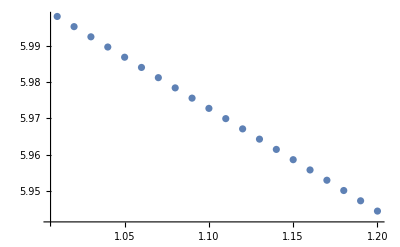

```mathematica
ListPlot[forplot]
```

```mathematica
refval=Table[0.5/((1-x^2)^(3/2))/.x->ii/100,{ii,101,120}]
```

{0.+175.459 ⅈ,0.+61.5741 ⅈ,0.+33.2693 ⅈ,0.+21.4504 ⅈ,0.+15.2365 ⅈ,0.+11.5065 ⅈ,0.+9.06499 ⅈ,0.+7.36614 ⅈ,0.+6.12896 ⅈ,0.+5.19566 ⅈ,0.+4.47154 ⅈ,0.+3.89668 ⅈ,0.+3.43151 ⅈ,0.+3.049 ⅈ,0.+2.73008 ⅈ,0.+2.46099 ⅈ,0.+2.23155 ⅈ,0.+2.03412 ⅈ,0.+1.86283 ⅈ,0.+1.71313 ⅈ}

```mathematica
forplotRef=Table[{(100+ii)/100.,Log[Im[refval[[ii]]]]//N},{ii,1,Length@numRes}]
```

{{1.01,5.16741},{1.02,4.12024},{1.03,3.50464},{1.04,3.06574},{1.05,2.72369},{1.06,2.44291},{1.07,2.20442},{1.08,1.99689},{1.09,1.81303},{1.1,1.64782},{1.11,1.49773},{1.12,1.36012},{1.13,1.233},{1.14,1.11481},{1.15,1.00433},{1.16,0.900563},{1.17,0.802697},{1.18,0.710063},{1.19,0.622097},{1.2,0.538324}}

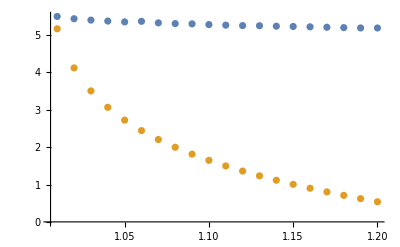

```mathematica
ListPlot[{forplot,forplotRef}]
```

```mathematica
(2^(n-1)√π Gamma[(1-n)/2])/Gamma[n/2]//FunctionExpand//Simplify
```

2^(-1+2 n) Gamma[1-n] Sin[(n π)/2]

```mathematica
Quit[]
```

#### that’s one approach

```mathematica
expandedEik=Series[eikonalFull,{s,0,30}];
expandedEik=expandedEik/.Subscript[y, b][0]->-1/.y1->12/10//Normal;
```

```mathematica
terms=CoefficientList[expandedEik,s];
```

```mathematica
sIntegration=Table[Integrate[terms[[ii]]//Simplify,{σ[1],0,1},{σ[2],0,1}],{ii,Length@terms}];
```

```mathematica
poly=Sum[sIntegration[[i]]*x^(i-1),{i,Length@sIntegration}]
```

(π^3 (465-586 √(2 π)))/(10 √11)+(π^3 (-15345+75401 √(2 π)) x^2)/(660 √11)+(π^3 (230175-6729628 √(2 π)) x^4)/(13200 √11)+(3 π^3 (-59675+10401892 √(2 π)) x^6)/(12320 √11)+(π^3 (8056125-8102291222 √(2 π)) x^8)/(633600 √11)+(7 π^3 (-690525+3901981097 √(2 π)) x^10)/(422400 √11)+(π^3 (48873825-1521787193588 √(2 π)) x^12)/(4659200 √11)+(13 π^3 (-2577960+435989978419 √(2 π)) x^14)/(3440640 √11)+(π^3 (3204726525-2911882325141249 √(2 π)) x^16)/(350945280 √11)+(π^3 (-22551779250+109157865785985253 √(2 π)) x^18)/(2614886400 √11)+(π^3 (24806957175-635326033296949187 √(2 π)) x^20)/(3027763200 √11)+(π^3 (-18861488100+2541875893420990787 √(2 π)) x^22)/(2411724800 √11)-(7 π^3 (-481641571125+339997791997378613611 √(2 π)) x^24)/(449839104000 √11)+(π^3 (-32677528133250+120367727404087546736849 √(2 π)) x^26)/(4534378168320 √11)+(π^3 (1015337481283125-19451930297955046773411419 √(2 π)) x^28)/(146107740979200 √11)+(3 π^3 (-7460850232836000+741330568619062427245322561 √(2 π)) x^30)/(3331928254054400 √11)

```mathematica
poly//N
```

-938.506+2459.81 x^2-11784. x^4+59220.4 x^6-299546. x^8+1.51521×10^6 x^10-7.65385×10^6 x^12+3.86032×10^7 x^14-1.94436×10^8 x^16+9.7824×10^8 x^18-4.9172×10^9 x^20+2.46985×10^10 x^22-1.23982×10^11 x^24+6.22065×10^11 x^26-3.11984×10^12 x^28+1.56416×10^13 x^30

```mathematica
polyVal=Table[{ii,poly/.x->ii//N},{ii,0,1,0.01}]
```

{{0.,-938.506},{0.01,-938.26},{0.02,-937.524},{0.03,-936.301},{0.04,-934.6},{0.05,-932.429},{0.06,-929.8},{0.07,-926.729},{0.08,-923.23},{0.09,-919.324},{0.1,-915.03},{0.11,-910.368},{0.12,-905.363},{0.13,-900.037},{0.14,-894.415},{0.15,-888.52},{0.16,-882.378},{0.17,-876.012},{0.18,-869.447},{0.19,-862.707},{0.2,-855.815},{0.21,-848.793},{0.22,-841.661},{0.23,-834.442},{0.24,-827.153},{0.25,-819.813},{0.26,-812.439},{0.27,-805.047},{0.28,-797.652},{0.29,-790.267},{0.3,-782.904},{0.31,-775.573},{0.32,-768.284},{0.33,-761.04},{0.34,-753.84},{0.35,-746.664},{0.36,-739.462},{0.37,-732.111},{0.38,-724.334},{0.39,-715.539},{0.4,-704.486},{0.41,-688.633},{0.42,-662.873},{0.43,-617.121},{0.44,-531.805},{0.45,-369.53},{0.46,-59.925},{0.47,527.528},{0.48,1631.59},{0.49,3683.29},{0.5,7450.98},{0.51,14287.8},{0.52,26549.},{0.53,48288.9},{0.54,86411.7},{0.55,152554.},{0.56,266134.},{0.57,459248.},{0.58,784459.},{0.59,1.32708×10^6},{0.6,2.22443×10^6},{0.61,3.69563×10^6},{0.62,6.08764×10^6},{0.63,9.94557×10^6},{0.64,1.61195×10^7},{0.65,2.59252×10^7},{0.66,4.1386×10^7},{0.67,6.55907×10^7},{0.68,1.03225×10^8},{0.69,1.61352×10^8},{0.7,2.50552×10^8},{0.71,3.86577×10^8},{0.72,5.92749×10^8},{0.73,9.03395×10^8},{0.74,1.36877×10^9},{0.75,2.06205×10^9},{0.76,3.08925×10^9},{0.77,4.60313×10^9},{0.78,6.82282×10^9},{0.79,1.00611×10^10},{0.8,1.47623×10^10},{0.81,2.15548×10^10},{0.82,3.13235×10^10},{0.83,4.5309×10^10},{0.84,6.52431×10^10},{0.85,9.35338×10^10},{0.86,1.33516×10^11},{0.87,1.89789×10^11},{0.88,2.68673×10^11},{0.89,3.78824×10^11},{0.9,5.32043×10^11},{0.91,7.44378×10^11},{0.92,1.03756×10^12},{0.93,1.44093×10^12},{0.94,1.99396×10^12},{0.95,2.74958×10^12},{0.96,3.77857×10^12},{0.97,5.17524×10^12},{0.98,7.0649×10^12},{0.99,9.61354×10^12},{1.,1.30404×10^13}}

```mathematica
fitfun=ref=Series[β/((1-x^2)^(3/2)),{x,0,30}]//Normal;
```

```mathematica
mdl=NonlinearModelFit[polyVal,fitfun,β,x]
```

FittedModel[1.84831×10^11+2.77246×10^11 x^2+3.46558×10^11 x^4+4.04317×10^11 x^6+4.54857×10^11 x^8+«7»+7.44776×10^11 x^24+7.73422×10^11 x^26+8.01044×10^11 x^28+8.27745×10^11 x^30]

```mathematica
ref=fitfun/.mdl["BestFitParameters"]//Normal
```

1.84831×10^11+2.77246×10^11 x^2+3.46558×10^11 x^4+4.04317×10^11 x^6+4.54857×10^11 x^8+5.00342×10^11 x^10+5.42038×10^11 x^12+5.80755×10^11 x^14+6.17052×10^11 x^16+6.51332×10^11 x^18+6.83899×10^11 x^20+7.14985×10^11 x^22+7.44776×10^11 x^24+7.73422×10^11 x^26+8.01044×10^11 x^28+8.27745×10^11 x^30

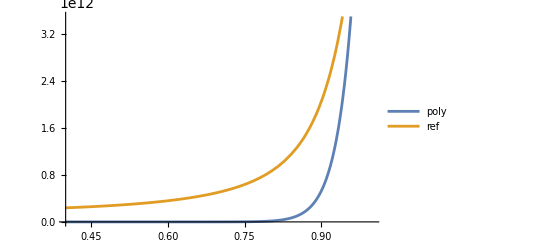

```mathematica
Plot[{poly,ref},{x,0.4,1},PlotLegends->"Expressions"]
```

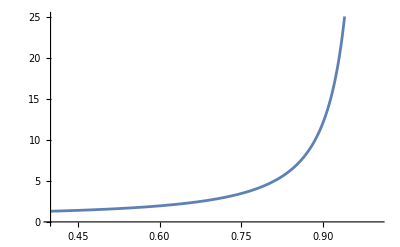

```mathematica
Plot[1/((1-x^2)^(3/2)),{x,0.4,1}]
```

```mathematica
ref=Series[β/((1-x^2)^(3/2)),{x,0,20}]//Normal
```

β+(3 x^2 β)/2+(15 x^4 β)/8+(35 x^6 β)/16+(315 x^8 β)/128+(693 x^10 β)/256+(3003 x^12 β)/1024+(6435 x^14 β)/2048+(109395 x^16 β)/32768+(230945 x^18 β)/65536+(969969 x^20 β)/262144

```mathematica
terms=(8 √2 π^(7/2) y1 Eps[a[0],b[0],v[1],v[2]] √(Subscript[y, 2][0]))/((1-y1^2)^(3/2) (Subscript[y, b][0])^(3/2))-(8 √2 π^(7/2) y1^3 Eps[a[0],b[0],v[1],v[2]] √(Subscript[y, 2][0]))/((1-y1^2)^(3/2) (Subscript[y, b][0])^(3/2))+(4 √2 π^(7/2) y1 Eps[a[0],b[0],v[1],v[2]] (Subscript[y, 2][0])^(3/2))/((1-y1^2)^(3/2) (Subscript[y, b][0])^(3/2))-(6 √2 π^(7/2) y1^3 Eps[a[0],b[0],v[1],v[2]] (Subscript[y, 2][0])^(3/2))/((1-y1^2)^(3/2) (Subscript[y, b][0])^(3/2))+(24 √2 π^(7/2) y1 Eps[a[0],b[0],v[1],v[2]] σ[2]^2 (Subscript[y, 2][0])^(3/2))/((1-y1^2)^(3/2) (Subscript[y, b][0])^(3/2))-(30 √2 π^(7/2) y1^3 Eps[a[0],b[0],v[1],v[2]] σ[2]^2 (Subscript[y, 2][0])^(3/2))/((1-y1^2)^(3/2) (Subscript[y, b][0])^(3/2))+(27 π^(7/2) y1 Eps[a[0],b[0],v[1],v[2]] (Subscript[y, 2][0])^(5/2))/(4 √2 (1-y1^2)^(3/2) (Subscript[y, b][0])^(3/2))-(45 π^(7/2) y1^3 Eps[a[0],b[0],v[1],v[2]] (Subscript[y, 2][0])^(5/2))/(4 √2 (1-y1^2)^(3/2) (Subscript[y, b][0])^(3/2))+(175 π^(7/2) y1 Eps[a[0],b[0],v[1],v[2]] σ[2]^2 (Subscript[y, 2][0])^(5/2))/(2 √2 (1-y1^2)^(3/2) (Subscript[y, b][0])^(3/2))-(285 π^(7/2) y1^3 Eps[a[0],b[0],v[1],v[2]] σ[2]^2 (Subscript[y, 2][0])^(5/2))/(2 √2 (1-y1^2)^(3/2) (Subscript[y, b][0])^(3/2))+(495 π^(7/2) y1 Eps[a[0],b[0],v[1],v[2]] σ[2]^4 (Subscript[y, 2][0])^(5/2))/(4 √2 (1-y1^2)^(3/2) (Subscript[y, b][0])^(3/2))-(705 π^(7/2) y1^3 Eps[a[0],b[0],v[1],v[2]] σ[2]^4 (Subscript[y, 2][0])^(5/2))/(4 √2 (1-y1^2)^(3/2) (Subscript[y, b][0])^(3/2))+(3 π^3)/(2 √(1-y1^2) √(Subscript[y, b][0]))-(√2 π^(7/2))/(√(1-y1^2) √(Subscript[y, b][0]))-(15 π^3 y1^2)/(2 √(1-y1^2) √(Subscript[y, b][0]))+(7 √2 π^(7/2) y1^2)/(√(1-y1^2) √(Subscript[y, b][0]))+(3 √2 π^(7/2))/(√(1-y1^2) (-1+σ[2]) σ[2] √(Subscript[y, b][0]))+(3 √2 π^(7/2) y1^2)/(√(1-y1^2) (σ[2]-σ[2]^2) √(Subscript[y, b][0]))+(3 √2 π^(7/2))/(√(1-y1^2) (σ[2]+σ[2]^2) √(Subscript[y, b][0]))-(3 √2 π^(7/2) y1^2)/(√(1-y1^2) (σ[2]+σ[2]^2) √(Subscript[y, b][0]))+(3 π^3 Subscript[y, 2][0])/(4 √(1-y1^2) √(Subscript[y, b][0]))+(π^(7/2) Subscript[y, 2][0])/(2 √2 √(1-y1^2) √(Subscript[y, b][0]))-(15 π^3 y1^2 Subscript[y, 2][0])/(4 √(1-y1^2) √(Subscript[y, b][0]))+(35 π^(7/2) y1^2 Subscript[y, 2][0])/(2 √2 √(1-y1^2) √(Subscript[y, b][0]))+(4 √2 π^(7/2) Subscript[y, 2][0])/((-1+y1) (1+y1) √(1-y1^2) √(Subscript[y, b][0]))-(12 √2 π^(7/2) y1^2 Subscript[y, 2][0])/((-1+y1) (1+y1) √(1-y1^2) √(Subscript[y, b][0]))+(10 √2 π^(7/2) y1^4 Subscript[y, 2][0])/((-1+y1) (1+y1) √(1-y1^2) √(Subscript[y, b][0]))-(√2 π^(7/2) (Log[1-σ[2]]-Log[-σ[2]]+1/(-1+σ[2])) σ[2] Subscript[y, 2][0])/(√(1-y1^2) √(Subscript[y, b][0]))-(7 √2 π^(7/2) y1^2 (Log[1-σ[2]]-Log[-σ[2]]+1/(-1+σ[2])) σ[2] Subscript[y, 2][0])/(√(1-y1^2) √(Subscript[y, b][0]))+(2 √2 π^(7/2) σ[2] Subscript[y, 2][0])/(√(1-y1^2) (-1+σ[2]) √(Subscript[y, b][0]))+(2 √2 π^(7/2) y1^2 σ[2] Subscript[y, 2][0])/(√(1-y1^2) (-1+σ[2]) √(Subscript[y, b][0]))+(2 √2 π^(7/2) σ[2] Subscript[y, 2][0])/(√(1-y1^2) (1+σ[2]) √(Subscript[y, b][0]))+(2 √2 π^(7/2) y1^2 σ[2] Subscript[y, 2][0])/(√(1-y1^2) (1+σ[2]) √(Subscript[y, b][0]))+(π^(7/2) (2+1/(-1+σ[2])+2 (Log[1-σ[2]]-Log[-σ[2]]) σ[2]) Subscript[y, 2][0])/(√(2-2 y1^2) √(Subscript[y, b][0]))+(7 π^(7/2) y1^2 (2+1/(-1+σ[2])+2 (Log[1-σ[2]]-Log[-σ[2]]) σ[2]) Subscript[y, 2][0])/(√(2-2 y1^2) √(Subscript[y, b][0]))+(√2 π^(7/2) σ[2] (-Log[σ[2]]+Log[1+σ[2]]-1/(1+σ[2])) Subscript[y, 2][0])/(√(1-y1^2) √(Subscript[y, b][0]))+(7 √2 π^(7/2) y1^2 σ[2] (-Log[σ[2]]+Log[1+σ[2]]-1/(1+σ[2])) Subscript[y, 2][0])/(√(1-y1^2) √(Subscript[y, b][0]))+(π^(7/2) (2+2 (Log[σ[2]]-Log[1+σ[2]]) σ[2]-1/(1+σ[2])) Subscript[y, 2][0])/(√(2-2 y1^2) √(Subscript[y, b][0]))+(7 π^(7/2) y1^2 (2+2 (Log[σ[2]]-Log[1+σ[2]]) σ[2]-1/(1+σ[2])) Subscript[y, 2][0])/(√(2-2 y1^2) √(Subscript[y, b][0]))+(9 π^3 (Subscript[y, 2][0])^2)/(16 √(1-y1^2) √(Subscript[y, b][0]))-(7 π^(7/2) (Subscript[y, 2][0])^2)/(2 √2 √(1-y1^2) √(Subscript[y, b][0]))-(45 π^3 y1^2 (Subscript[y, 2][0])^2)/(16 √(1-y1^2) √(Subscript[y, b][0]))+(53 π^(7/2) y1^2 (Subscript[y, 2][0])^2)/(√2 √(1-y1^2) √(Subscript[y, b][0]))+(63 π^(7/2) (Subscript[y, 2][0])^2)/(2 √2 (-1+y1) (1+y1) √(1-y1^2) √(Subscript[y, b][0]))-(111 π^(7/2) y1^2 (Subscript[y, 2][0])^2)/(√2 (-1+y1) (1+y1) √(1-y1^2) √(Subscript[y, b][0]))+(207 π^(7/2) y1^4 (Subscript[y, 2][0])^2)/(2 √2 (-1+y1) (1+y1) √(1-y1^2) √(Subscript[y, b][0]))-(33 π^(7/2) (Log[1-σ[2]]-Log[-σ[2]]+1/(-1+σ[2])) σ[2]^3 (Subscript[y, 2][0])^2)/(8 √(2-2 y1^2) √(Subscript[y, b][0]))-(735 π^(7/2) y1^2 (Log[1-σ[2]]-Log[-σ[2]]+1/(-1+σ[2])) σ[2]^3 (Subscript[y, 2][0])^2)/(8 √(2-2 y1^2) √(Subscript[y, b][0]))+(129 π^(7/2) σ[2]^3 (Subscript[y, 2][0])^2)/(32 √(2-2 y1^2) (-1+σ[2]) √(Subscript[y, b][0]))+(831 π^(7/2) y1^2 σ[2]^3 (Subscript[y, 2][0])^2)/(32 √(2-2 y1^2) (-1+σ[2]) √(Subscript[y, b][0]))+(129 π^(7/2) σ[2]^3 (Subscript[y, 2][0])^2)/(32 √(2-2 y1^2) (1+σ[2]) √(Subscript[y, b][0]))+(831 π^(7/2) y1^2 σ[2]^3 (Subscript[y, 2][0])^2)/(32 √(2-2 y1^2) (1+σ[2]) √(Subscript[y, b][0]))+(51 π^(7/2) σ[2]^2 (2+1/(-1+σ[2])+2 (Log[1-σ[2]]-Log[-σ[2]]) σ[2]) (Subscript[y, 2][0])^2)/(16 √(2-2 y1^2) √(Subscript[y, b][0]))+(1869 π^(7/2) y1^2 σ[2]^2 (2+1/(-1+σ[2])+2 (Log[1-σ[2]]-Log[-σ[2]]) σ[2]) (Subscript[y, 2][0])^2)/(16 √(2-2 y1^2) √(Subscript[y, b][0]))-(9 π^(7/2) σ[2] (3/2+1/(-1+σ[2])+3 σ[2]+3 (Log[1-σ[2]]-Log[-σ[2]]) σ[2]^2) (Subscript[y, 2][0])^2)/(8 √(2-2 y1^2) √(Subscript[y, b][0]))-(567 π^(7/2) y1^2 σ[2] (3/2+1/(-1+σ[2])+3 σ[2]+3 (Log[1-σ[2]]-Log[-σ[2]]) σ[2]^2) (Subscript[y, 2][0])^2)/(8 √(2-2 y1^2) √(Subscript[y, b][0]))+(9 π^(7/2) (4/3+1/(-1+σ[2])+2 σ[2]+4 σ[2]^2+4 (Log[1-σ[2]]-Log[-σ[2]]) σ[2]^3) (Subscript[y, 2][0])^2)/(32 √(2-2 y1^2) √(Subscript[y, b][0]))+(567 π^(7/2) y1^2 (4/3+1/(-1+σ[2])+2 σ[2]+4 σ[2]^2+4 (Log[1-σ[2]]-Log[-σ[2]]) σ[2]^3) (Subscript[y, 2][0])^2)/(32 √(2-2 y1^2) √(Subscript[y, b][0]))+(33 π^(7/2) σ[2]^3 (-Log[σ[2]]+Log[1+σ[2]]-1/(1+σ[2])) (Subscript[y, 2][0])^2)/(8 √(2-2 y1^2) √(Subscript[y, b][0]))+(735 π^(7/2) y1^2 σ[2]^3 (-Log[σ[2]]+Log[1+σ[2]]-1/(1+σ[2])) (Subscript[y, 2][0])^2)/(8 √(2-2 y1^2) √(Subscript[y, b][0]))+(51 π^(7/2) σ[2]^2 (2+2 (Log[σ[2]]-Log[1+σ[2]]) σ[2]-1/(1+σ[2])) (Subscript[y, 2][0])^2)/(16 √(2-2 y1^2) √(Subscript[y, b][0]))+(1869 π^(7/2) y1^2 σ[2]^2 (2+2 (Log[σ[2]]-Log[1+σ[2]]) σ[2]-1/(1+σ[2])) (Subscript[y, 2][0])^2)/(16 √(2-2 y1^2) √(Subscript[y, b][0]))-(9 π^(7/2) σ[2] (-1+3 σ[2]+6 σ[2]^2+6 (Log[σ[2]]-Log[1+σ[2]]) σ[2]^2 (1+σ[2])) (Subscript[y, 2][0])^2)/(16 √(2-2 y1^2) (1+σ[2]) √(Subscript[y, b][0]))-(567 π^(7/2) y1^2 σ[2] (-1+3 σ[2]+6 σ[2]^2+6 (Log[σ[2]]-Log[1+σ[2]]) σ[2]^2 (1+σ[2])) (Subscript[y, 2][0])^2)/(16 √(2-2 y1^2) (1+σ[2]) √(Subscript[y, b][0]))+(3 π^(7/2) (1+12 (Log[σ[2]]-Log[1+σ[2]]) σ[2]^3 (1+σ[2])+2 σ[2] (-1+3 σ[2]+6 σ[2]^2)) (Subscript[y, 2][0])^2)/(32 √(2-2 y1^2) (1+σ[2]) √(Subscript[y, b][0]))+(189 π^(7/2) y1^2 (1+12 (Log[σ[2]]-Log[1+σ[2]]) σ[2]^3 (1+σ[2])+2 σ[2] (-1+3 σ[2]+6 σ[2]^2)) (Subscript[y, 2][0])^2)/(32 √(2-2 y1^2) (1+σ[2]) √(Subscript[y, b][0]))+(15 π^3 (Subscript[y, 2][0])^3)/(32 √(1-y1^2) √(Subscript[y, b][0]))-(715 π^(7/2) (Subscript[y, 2][0])^3)/(32 √2 √(1-y1^2) √(Subscript[y, b][0]))-(75 π^3 y1^2 (Subscript[y, 2][0])^3)/(32 √(1-y1^2) √(Subscript[y, b][0]))+(6115 π^(7/2) y1^2 (Subscript[y, 2][0])^3)/(32 √2 √(1-y1^2) √(Subscript[y, b][0]))+(585 π^(7/2) (Subscript[y, 2][0])^3)/(4 √2 (-1+y1) (1+y1) √(1-y1^2) √(Subscript[y, b][0]))-(1095 π^(7/2) y1^2 (Subscript[y, 2][0])^3)/(2 √2 (-1+y1) (1+y1) √(1-y1^2) √(Subscript[y, b][0]))+(2115 π^(7/2) y1^4 (Subscript[y, 2][0])^3)/(4 √2 (-1+y1) (1+y1) √(1-y1^2) √(Subscript[y, b][0]))-(3585 π^(7/2) (Log[1-σ[2]]-Log[-σ[2]]+1/(-1+σ[2])) σ[2]^5 (Subscript[y, 2][0])^3)/(512 √(2-2 y1^2) √(Subscript[y, b][0]))-(190335 π^(7/2) y1^2 (Log[1-σ[2]]-Log[-σ[2]]+1/(-1+σ[2])) σ[2]^5 (Subscript[y, 2][0])^3)/(512 √(2-2 y1^2) √(Subscript[y, b][0]))+(4635 π^(7/2) σ[2]^5 (Subscript[y, 2][0])^3)/(1024 √(2-2 y1^2) (-1+σ[2]) √(Subscript[y, b][0]))+(85605 π^(7/2) y1^2 σ[2]^5 (Subscript[y, 2][0])^3)/(1024 √(2-2 y1^2) (-1+σ[2]) √(Subscript[y, b][0]))+(4635 π^(7/2) σ[2]^5 (Subscript[y, 2][0])^3)/(1024 √(2-2 y1^2) (1+σ[2]) √(Subscript[y, b][0]))+(85605 π^(7/2) y1^2 σ[2]^5 (Subscript[y, 2][0])^3)/(1024 √(2-2 y1^2) (1+σ[2]) √(Subscript[y, b][0]))+(7365 π^(7/2) σ[2]^4 (2+1/(-1+σ[2])+2 (Log[1-σ[2]]-Log[-σ[2]]) σ[2]) (Subscript[y, 2][0])^3)/(1024 √(2-2 y1^2) √(Subscript[y, b][0]))+(716475 π^(7/2) y1^2 σ[2]^4 (2+1/(-1+σ[2])+2 (Log[1-σ[2]]-Log[-σ[2]]) σ[2]) (Subscript[y, 2][0])^3)/(1024 √(2-2 y1^2) √(Subscript[y, b][0]))-(1095 π^(7/2) σ[2]^3 (-1-3 σ[2]+6 σ[2]^2+6 (Log[1-σ[2]]-Log[-σ[2]]) (-1+σ[2]) σ[2]^2) (Subscript[y, 2][0])^3)/(512 √(2-2 y1^2) (-1+σ[2]) √(Subscript[y, b][0]))-(188985 π^(7/2) y1^2 σ[2]^3 (-1-3 σ[2]+6 σ[2]^2+6 (Log[1-σ[2]]-Log[-σ[2]]) (-1+σ[2]) σ[2]^2) (Subscript[y, 2][0])^3)/(512 √(2-2 y1^2) (-1+σ[2]) √(Subscript[y, b][0]))+(476235 π^(7/2) y1^2 σ[2]^2 (4/3+1/(-1+σ[2])+2 σ[2]+4 σ[2]^2+4 (Log[1-σ[2]]-Log[-σ[2]]) σ[2]^3) (Subscript[y, 2][0])^3)/(1024 √(2-2 y1^2) √(Subscript[y, b][0]))+(75 π^(7/2) (6/5+1/(-1+σ[2])+(3 σ[2])/2+2 σ[2]^2+3 σ[2]^3+6 σ[2]^4+6 (Log[1-σ[2]]-Log[-σ[2]]) σ[2]^5) (Subscript[y, 2][0])^3)/(1024 √(2-2 y1^2) √(Subscript[y, b][0]))+(28725 π^(7/2) y1^2 (6/5+1/(-1+σ[2])+(3 σ[2])/2+2 σ[2]^2+3 σ[2]^3+6 σ[2]^4+6 (Log[1-σ[2]]-Log[-σ[2]]) σ[2]^5) (Subscript[y, 2][0])^3)/(1024 √(2-2 y1^2) √(Subscript[y, b][0]))+(3585 π^(7/2) σ[2]^5 (-Log[σ[2]]+Log[1+σ[2]]-1/(1+σ[2])) (Subscript[y, 2][0])^3)/(512 √(2-2 y1^2) √(Subscript[y, b][0]))+(190335 π^(7/2) y1^2 σ[2]^5 (-Log[σ[2]]+Log[1+σ[2]]-1/(1+σ[2])) (Subscript[y, 2][0])^3)/(512 √(2-2 y1^2) √(Subscript[y, b][0]))+(7365 π^(7/2) σ[2]^4 (2+2 (Log[σ[2]]-Log[1+σ[2]]) σ[2]-1/(1+σ[2])) (Subscript[y, 2][0])^3)/(1024 √(2-2 y1^2) √(Subscript[y, b][0]))+(716475 π^(7/2) y1^2 σ[2]^4 (2+2 (Log[σ[2]]-Log[1+σ[2]]) σ[2]-1/(1+σ[2])) (Subscript[y, 2][0])^3)/(1024 √(2-2 y1^2) √(Subscript[y, b][0]))-(1095 π^(7/2) σ[2]^3 (-1+3 σ[2]+6 σ[2]^2+6 (Log[σ[2]]-Log[1+σ[2]]) σ[2]^2 (1+σ[2])) (Subscript[y, 2][0])^3)/(512 √(2-2 y1^2) (1+σ[2]) √(Subscript[y, b][0]))-(188985 π^(7/2) y1^2 σ[2]^3 (-1+3 σ[2]+6 σ[2]^2+6 (Log[σ[2]]-Log[1+σ[2]]) σ[2]^2 (1+σ[2])) (Subscript[y, 2][0])^3)/(512 √(2-2 y1^2) (1+σ[2]) √(Subscript[y, b][0]))+(615 π^(7/2) σ[2]^2 (-1+12 (Log[1-σ[2]]-Log[-σ[2]]) (-1+σ[2]) σ[2]^3+2 σ[2] (-1-3 σ[2]+6 σ[2]^2)) (Subscript[y, 2][0])^3)/(1024 √(2-2 y1^2) (-1+σ[2]) √(Subscript[y, b][0]))+(86175 π^(7/2) y1^2 σ[2] (5/4+5 (-Log[σ[2]]+Log[1+σ[2]]) σ[2]^4-1/(1+σ[2])-5/6 σ[2] (2-3 σ[2]+6 σ[2]^2)) (Subscript[y, 2][0])^3)/(512 √(2-2 y1^2) √(Subscript[y, b][0]))+(615 π^(7/2) σ[2]^2 (1+12 (Log[σ[2]]-Log[1+σ[2]]) σ[2]^3 (1+σ[2])+2 σ[2] (-1+3 σ[2]+6 σ[2]^2)) (Subscript[y, 2][0])^3)/(1024 √(2-2 y1^2) (1+σ[2]) √(Subscript[y, b][0]))+(158745 π^(7/2) y1^2 σ[2]^2 (1+12 (Log[σ[2]]-Log[1+σ[2]]) σ[2]^3 (1+σ[2])+2 σ[2] (-1+3 σ[2]+6 σ[2]^2)) (Subscript[y, 2][0])^3)/(1024 √(2-2 y1^2) (1+σ[2]) √(Subscript[y, b][0]))-(75 π^(7/2) σ[2] (-3+60 (Log[1-σ[2]]-Log[-σ[2]]) (-1+σ[2]) σ[2]^4+5 σ[2] (-1+2 σ[2] (-1-3 σ[2]+6 σ[2]^2))) (Subscript[y, 2][0])^3)/(2048 √(2-2 y1^2) (-1+σ[2]) √(Subscript[y, b][0]))-(28725 π^(7/2) y1^2 σ[2] (-3+60 (Log[1-σ[2]]-Log[-σ[2]]) (-1+σ[2]) σ[2]^4+5 σ[2] (-1+2 σ[2] (-1-3 σ[2]+6 σ[2]^2))) (Subscript[y, 2][0])^3)/(2048 √(2-2 y1^2) (-1+σ[2]) √(Subscript[y, b][0]))-(75 π^(7/2) σ[2] (-3+60 (Log[σ[2]]-Log[1+σ[2]]) σ[2]^4 (1+σ[2])+5 σ[2] (1+2 σ[2] (-1+3 σ[2]+6 σ[2]^2))) (Subscript[y, 2][0])^3)/(2048 √(2-2 y1^2) (1+σ[2]) √(Subscript[y, b][0]))+(15 π^(7/2) (2+60 (Log[σ[2]]-Log[1+σ[2]]) σ[2]^5 (1+σ[2])+σ[2] (-3+5 σ[2] (1+2 σ[2] (-1+3 σ[2]+6 σ[2]^2)))) (Subscript[y, 2][0])^3)/(2048 √(2-2 y1^2) (1+σ[2]) √(Subscript[y, b][0]))+(5745 π^(7/2) y1^2 (2+60 (Log[σ[2]]-Log[1+σ[2]]) σ[2]^5 (1+σ[2])+σ[2] (-3+5 σ[2] (1+2 σ[2] (-1+3 σ[2]+6 σ[2]^2)))) (Subscript[y, 2][0])^3)/(2048 √(2-2 y1^2) (1+σ[2]) √(Subscript[y, b][0]));
```

```mathematica
Integrate[#,{σ[2],0,1}]&/@terms
```

Integrate::idiv: Integral of (3 √2 π^(7/2))/(√(1-y1^2) (-1+σ[2]) σ[2] √y_b[0]) does not converge on {0,1}.

Integrate::idiv: Integral of (3 √2 π^(7/2) y1^2)/(√(1-y1^2) (σ[2]-σ[2]^2) √y_b[0]) does not converge on {0,1}.

Integrate::idiv: Integral of (3 √2 π^(7/2))/(√(1-y1^2) (σ[2]+σ[2]^2) √y_b[0]) does not converge on {0,1}.

General::stop: Further output of Integrate::idiv will be suppressed during this calculation.

$Aborted

```mathematica
Integrate[Coefficient[expandedEik,s,0],{σ[1],0,1}]
```

ConditionalExpression[-1/(1024 (1-y1^2)^(3/2) (-1+σ[2]^2) y_b[0]^(3/2))π^3 (128 √(2 π) y1 Eps[a[0],b[0],v[1],v[2]] (-1+σ[2]^2) √y_2[0] (-64-32 (1+6 σ[2]^2) y_2[0]-(27+350 σ[2]^2+495 σ[2]^4) y_2[0]^2+y1^2 (64+48 (1+5 σ[2]^2) y_2[0]+15 (3+38 σ[2]^2+47 σ[2]^4) y_2[0]^2))+(1536-7168 √(2 π)+768 y_2[0]-2816 √(2 π) y_2[0]+576 y_2[0]^2-17824 √(2 π) y_2[0]^2+480 y_2[0]^3-86305 √(2 π) y_2[0]^3-4635 √(2 π) σ[2]^6 y_2[0]^3+3 √(2 π) σ[2]^4 y_2[0]^2 (-1376+775 y_2[0])+σ[2]^2 (512 (-3+2 √(2 π))-256 (3+√(2 π)) y_2[0]+64 (-9+307 √(2 π)) y_2[0]^2+5 (-96+17339 √(2 π)) y_2[0]^3)-2 y1^2 (-512 (-9+20 √(2 π))-256 (-9+53 √(2 π)) y_2[0]-32 (-54+1433 √(2 π)) y_2[0]^2+3 √(2 π) σ[2]^4 (3744-2105 y_2[0]) y_2[0]^2-5 (-288+39533 √(2 π)) y_2[0]^3+40485 √(2 π) σ[2]^6 y_2[0]^3+σ[2]^2 (512 (-9+8 √(2 π))+256 (-9+41 √(2 π)) y_2[0]+64 (-27+505 √(2 π)) y_2[0]^2+5 (-288+32315 √(2 π)) y_2[0]^3))+y1^4 (512 (15-26 √(2 π))-256 (-15+103 √(2 π)) y_2[0]-32 (-90+2693 √(2 π)) y_2[0]^2-5 (-480+74861 √(2 π)) y_2[0]^3+85605 √(2 π) σ[2]^6 y_2[0]^3-3 √(2 π) σ[2]^4 y_2[0]^2 (-8864+4985 y_2[0])+σ[2]^2 (512 (-15+14 √(2 π))+256 (-15+91 √(2 π)) y_2[0]+320 (-9+179 √(2 π)) y_2[0]^2+5 (-480+60347 √(2 π)) y_2[0]^3))) y_b[0]), 1+Re[σ[2]]<0||Re[σ[2]]>1||σ[2]∉ℝ]

```mathematica
Integrate[Integrate[%292,{σ[1],0,1}],{σ[2],0,1}]
```

Undefined

```mathematica
Integrate[Coefficient[%292,Subscript[y, 2][0],0],{σ[1],0,1}]
```

ConditionalExpression[(π^3 (-615+926 √(2 π)+(615-194 √(2 π)) σ[2]^2))/(10 √61 (-1+σ[2]^2)), Re[σ[2]]<-1||Re[σ[2]]>1||σ[2]∉ℝ]

```mathematica
Integrate[(π^3 (-615+926 √(2 π)+(615-194 √(2 π)) σ[2]^2))/(10 √61 (-1+σ[2]^2)),σ[2]]//TrigExpand
```

-6/5 √122 π^(7/2) ArcTanh[σ[2]]+(123 π^3 σ[2])/(2 √61)-97/5 √(2/61) π^(7/2) σ[2]

```mathematica
%265//Expand
```

(6 √2 π^(7/2) σ[1]^2)/(√(1-y1^2) (σ[1]^2-σ[2]^2)^2 √y_b[0])-(6 √2 π^(7/2) y1^2 σ[1]^2)/(√(1-y1^2) (σ[1]^2-σ[2]^2)^2 √y_b[0])+(3 π^3 σ[1]^4)/(2 √(1-y1^2) (σ[1]^2-σ[2]^2)^2 √y_b[0])-(√2 π^(7/2) σ[1]^4)/(√(1-y1^2) (σ[1]^2-σ[2]^2)^2 √y_b[0])-(15 π^3 y1^2 σ[1]^4)/(2 √(1-y1^2) (σ[1]^2-σ[2]^2)^2 √y_b[0])+(7 √2 π^(7/2) y1^2 σ[1]^4)/(√(1-y1^2) (σ[1]^2-σ[2]^2)^2 √y_b[0])+(6 √2 π^(7/2) σ[2]^2)/(√(1-y1^2) (σ[1]^2-σ[2]^2)^2 √y_b[0])-(6 √2 π^(7/2) y1^2 σ[2]^2)/(√(1-y1^2) (σ[1]^2-σ[2]^2)^2 √y_b[0])-(3 π^3 σ[1]^2 σ[2]^2)/(√(1-y1^2) (σ[1]^2-σ[2]^2)^2 √y_b[0])+(2 √2 π^(7/2) σ[1]^2 σ[2]^2)/(√(1-y1^2) (σ[1]^2-σ[2]^2)^2 √y_b[0])+(15 π^3 y1^2 σ[1]^2 σ[2]^2)/(√(1-y1^2) (σ[1]^2-σ[2]^2)^2 √y_b[0])-(14 √2 π^(7/2) y1^2 σ[1]^2 σ[2]^2)/(√(1-y1^2) (σ[1]^2-σ[2]^2)^2 √y_b[0])+(3 π^3 σ[2]^4)/(2 √(1-y1^2) (σ[1]^2-σ[2]^2)^2 √y_b[0])-(√2 π^(7/2) σ[2]^4)/(√(1-y1^2) (σ[1]^2-σ[2]^2)^2 √y_b[0])-(15 π^3 y1^2 σ[2]^4)/(2 √(1-y1^2) (σ[1]^2-σ[2]^2)^2 √y_b[0])+(7 √2 π^(7/2) y1^2 σ[2]^4)/(√(1-y1^2) (σ[1]^2-σ[2]^2)^2 √y_b[0])

```mathematica
Integrate[%265,{σ[1],0,1}]
```

ConditionalExpression[(π^3 (3+√(2 π) (-2+12/(-1+σ[2]^2))+y1^2 (-15+√(2 π) (14-12/(-1+σ[2]^2)))))/(2 √(1-y1^2) √y_b[0]), Re[σ[2]]>1||Re[σ[2]]<-1||σ[2]∉ℝ]

```mathematica
Integrate[(π^3 (3+√(2 π) (-2+12/(-1+σ[2]^2))+y1^2 (-15+√(2 π) (14-12/(-1+σ[2]^2)))))/(2 √(1-y1^2) √(Subscript[y, b][0])),{σ[2],0,1}]
```

(π^3 (3-2 √(2 π) (1+Log[64])+y1^2 (-15+2 √(2 π) (7+Log[64]))))/(2 √(1-y1^2) √y_b[0])

```mathematica
(π^3 (3-2 √(2 π) (1+Log[64])+y1^2 (-15+2 √(2 π) (7+Log[64]))))/(2 √(1-y1^2) √(Subscript[y, b][0]))
```

(π^3 (3-2 √(2 π) (1+Log[64])+y1^2 (-15+2 √(2 π) (7+Log[64]))))/(2 √(1-y1^2) √y_b[0])

```mathematica
FourierTransform[(x^2)^(-n/2),x,s,Assumptions->{n>0},FourierParameters->{-1, 1}]/.s->1
```

(Gamma[1-n] Sin[(n π)/2])/π

#### another test

```mathematica
xpnd=eikonalFull/.dot[a[0],a[0]]->-s^2/.dot[b[0],b[0]]-> -nb^2/.y1->12/10;
```

```mathematica
expand=Series[xpnd,{s,0,30}]//Normal;
```

```mathematica
Integrate[expand/.s->1,{σ[1],0,1},{σ[2],0,1}]
```

1/(96907583922534088704000 √11 √-nb nb^(61/2))ⅈ (74323758219929547500743275420746595+3968 nb^2 (3768004601239977579992459676165+758574806809918530441698723525 nb^2+696 nb^4 (219622844069093818201787841+5 nb^2 (8861106910669456415663691+368 nb^2 (4864442545020330396228+984467343590648152521 nb^2+152 nb^4 (1313794008041470670+17 nb^2 (15724339289297925+3212711139966768 nb^2+1664 nb^4 (396809089908+82288817401 nb^2+48 nb^4 (361087455+78738149 nb^2+19123160 nb^4+7271880 nb^6))))))))) π^3

```mathematica
%294//Expand//PowerExpand//N
```

(7.17007×10^12)/nb^31+(1.44238×10^12)/nb^29+(2.90379×10^11)/nb^27+(5.85132×10^10)/nb^25+(1.18041×10^10)/nb^23+(2.38466×10^9)/nb^21+(4.82609×10^8)/nb^19+(9.7896×10^7)/nb^17+(1.99186×10^7)/nb^15+(4.06966×10^6)/nb^13+836415./nb^11+173453./nb^9+36533.7/nb^7+7966.48/nb^5+1934.82/nb^3+735.746/nb

```mathematica
eikonVals=Table[{ii/100,%295/.{nb->ii/100}},{ii,101,120}]//N
```

{{1.01,6.62722×10^12},{1.02,4.90826×10^12},{1.03,3.64629×10^12},{1.04,2.71693×10^12},{1.05,2.03041×10^12},{1.06,1.52177×10^12},{1.07,1.14379×10^12},{1.08,8.62094×10^11},{1.09,6.51562×10^11},{1.1,4.93773×10^11},{1.11,3.75188×10^11},{1.12,2.85827×10^11},{1.13,2.18308×10^11},{1.14,1.67159×10^11},{1.15,1.28312×10^11},{1.16,9.87331×10^10},{1.17,7.61555×10^10},{1.18,5.88798×10^10},{1.19,4.5629×10^10},{1.2,3.54414×10^10}}

```mathematica
refVals=Table[{ii/100,Im[11.8^10/((1-x^2)^(3/2))]/.x->ii/100},{ii,101,120}]//N
```

{{1.01,1.83665×10^13},{1.02,6.44537×10^12},{1.03,3.48252×10^12},{1.04,2.24535×10^12},{1.05,1.5949×10^12},{1.06,1.20446×10^12},{1.07,9.48894×10^11},{1.08,7.71063×10^11},{1.09,6.41559×10^11},{1.1,5.43865×10^11},{1.11,4.68066×10^11},{1.12,4.07891×10^11},{1.13,3.59199×10^11},{1.14,3.19159×10^11},{1.15,2.85776×10^11},{1.16,2.57608×10^11},{1.17,2.33592×10^11},{1.18,2.12925×10^11},{1.19,1.94995×10^11},{1.2,1.79325×10^11}}

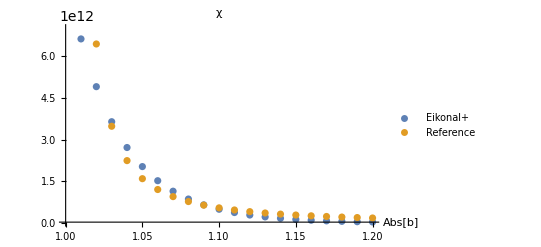

```mathematica
ListPlot[{eikonVals,refVals},PlotRange->{{1,1.2},{3*10^10,7*10^12}},AxesLabel->{Abs[b]},PlotLabel->"χ",PlotLegends->{"Eikonal+","Reference"}]
```

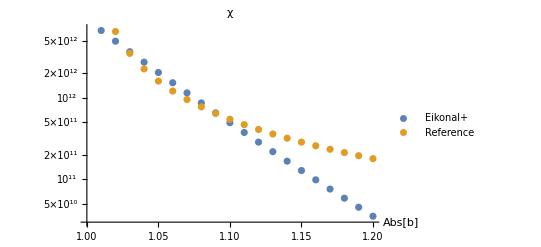

```mathematica
ListLogPlot[{eikonVals,refVals},PlotRange->{{1,1.2},{3*10^10,7*10^12}},AxesLabel->{Abs[b]},PlotLabel->"χ",PlotLegends->{"Eikonal+","Reference"}]
```

```mathematica
(30.54-29.52)/((30.54+29.52)/2)
```

0.033966

```mathematica
Series[1/((y^2-x^2)^(3/2)),{y,0,30}]//Normal//PowerExpand
```

ⅈ/x^3+(3 ⅈ y^2)/(2 x^5)+(15 ⅈ y^4)/(8 x^7)+(35 ⅈ y^6)/(16 x^9)+(315 ⅈ y^8)/(128 x^11)+(693 ⅈ y^10)/(256 x^13)+(3003 ⅈ y^12)/(1024 x^15)+(6435 ⅈ y^14)/(2048 x^17)+(109395 ⅈ y^16)/(32768 x^19)+(230945 ⅈ y^18)/(65536 x^21)+(969969 ⅈ y^20)/(262144 x^23)+(2028117 ⅈ y^22)/(524288 x^25)+(16900975 ⅈ y^24)/(4194304 x^27)+(35102025 ⅈ y^26)/(8388608 x^29)+(145422675 ⅈ y^28)/(33554432 x^31)+(300540195 ⅈ y^30)/(67108864 x^33)

```mathematica
%329/.y->1
```

1/((1-x^2)^(3/2))

```mathematica
Series[1/((1-x^2)^(3/2)),{x,1,0}]
```

(-1+x)^(3/2)/(2 √2 (1-x)^(3/2) (x-1)^(3/2))+√O[x-1]

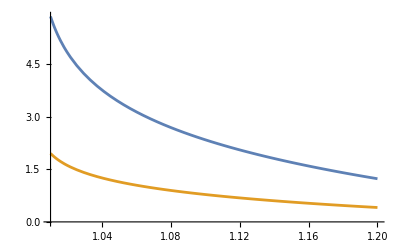

```mathematica
Plot[{Log[Im[1/((1-x^2)^(3/2))]],Log[-Im[1/((1-x^2)^(1/2))]]},{x,1.01,1.2}]
```

```mathematica
test=Series[xpnd,{s,1,0}]//Normal
```

(93 ⅈ π^3)/(2 √11 √(1-nb^2))+1/5 ⅈ √11 √(1-nb^2) π^3+(2 ⅈ (183+11 nb^2) π^2 EllipticK[-4/(1-nb^2)])/(5 √11 √(1-nb^2))+(250 ⅈ (1604/625+(121 nb^2)/625) π^2 ((-1+nb^2) EllipticE[-4/(1-nb^2)]-(-5+nb^2) EllipticK[-4/(1-nb^2)]))/(11 √11 √(1-nb^2) (-5+nb^2))-(60 ⅈ π^2 (1-σ[2]) (-47/25 EllipticK[-(-1+σ[2])^2/(-nb^2+σ[2]^2)] (1-nb^2+2 (-1+σ[2]) σ[2])-1/25 EllipticE[-(-1+σ[2])^2/(-nb^2+σ[2]^2)] (25+69 nb^2-50 σ[2]-44 σ[2]^2)))/(11 (1-nb^2+2 (-1+σ[2]) σ[2])^2 √(-nb^2+σ[2]^2))-(60 ⅈ π^2 (-1+σ[2]) (-47/25 EllipticK[-(-1+σ[2])^2/(-nb^2+σ[2]^2)] (1-nb^2+2 (-1+σ[2]) σ[2])-1/25 EllipticE[-(-1+σ[2])^2/(-nb^2+σ[2]^2)] (25+69 nb^2-50 σ[2]-44 σ[2]^2)))/(11 (1-nb^2+2 (-1+σ[2]) σ[2])^2 √(-nb^2+σ[2]^2))-(60 ⅈ π^2 (-1-σ[2]) (-1/25 EllipticE[-(1+σ[2])^2/(-nb^2+σ[2]^2)] (25+69 nb^2+50 σ[2]-44 σ[2]^2)+47/25 EllipticK[-(1+σ[2])^2/(-nb^2+σ[2]^2)] (-1+nb^2-2 σ[2] (1+σ[2]))))/(11 √(-nb^2+σ[2]^2) (1-nb^2+2 σ[2] (1+σ[2]))^2)-(60 ⅈ π^2 (1+σ[2]) (-1/25 EllipticE[-(1+σ[2])^2/(-nb^2+σ[2]^2)] (25+69 nb^2+50 σ[2]-44 σ[2]^2)+47/25 EllipticK[-(1+σ[2])^2/(-nb^2+σ[2]^2)] (-1+nb^2-2 σ[2] (1+σ[2]))))/(11 (-nb^2+σ[2]^2)^(5/2) (1+(1+σ[2])^2/(-nb^2+σ[2]^2))^2)+(20 ⅈ nb^2 π^2 (-1+σ[2]^2/nb^2) (1/25 EllipticE[-(σ[1]-σ[2])^2/(-nb^2+σ[2]^2)] (-nb^2+σ[2]^2) (-143 nb^4+286 nb^2 σ[1]^2-287 σ[1]^4-572 nb^2 σ[1] σ[2]+1148 σ[1]^3 σ[2]+572 nb^2 σ[2]^2-2008 σ[1]^2 σ[2]^2+1720 σ[1] σ[2]^3-716 σ[2]^4)-(-nb^2+σ[1]^2-2 σ[1] σ[2]+2 σ[2]^2) (-66/25 π (-nb^2+σ[2]^2) (-nb^2+σ[1]^2-2 σ[1] σ[2]+2 σ[2]^2)+1/25 EllipticK[-(σ[1]-σ[2])^2/(-nb^2+σ[2]^2)] (-11 nb^4+33 nb^2 σ[1]^2-94 σ[1]^4-66 nb^2 σ[1] σ[2]+376 σ[1]^3 σ[2]+55 nb^2 σ[2]^2-597 σ[1]^2 σ[2]^2+442 σ[1] σ[2]^3-138 σ[2]^4))))/(√11 (σ[1]-σ[2])^2 (-nb^2+σ[2]^2)^(7/2) (1+(σ[1]-σ[2])^2/(-nb^2+σ[2]^2))^2)+(10 ⅈ nb^2 π^2 (-1+σ[2]^2/nb^2) (-((-nb^2+σ[1]^2+2 σ[1] σ[2]+2 σ[2]^2) (-66/25 π (-nb^2+σ[2]^2) (-nb^2+σ[1]^2+2 σ[1] σ[2]+2 σ[2]^2)+1/25 EllipticK[-(σ[1]+σ[2])^2/(-nb^2+σ[2]^2)] (-11 nb^4+33 nb^2 σ[1]^2-94 σ[1]^4+66 nb^2 σ[1] σ[2]-376 σ[1]^3 σ[2]+55 nb^2 σ[2]^2-597 σ[1]^2 σ[2]^2-442 σ[1] σ[2]^3-138 σ[2]^4)))+EllipticE[-(σ[1]+σ[2])^2/(-nb^2+σ[2]^2)] (-nb^2+σ[2]^2) (13 (-nb^2+σ[1]^2+2 σ[1] σ[2]+2 σ[2]^2)^2-36/25 (17 (σ[1]+σ[2])^4-26 (σ[1]+σ[2])^2 (nb^2-σ[2]^2)+13 (-nb^2+σ[2]^2)^2))))/(√11 (σ[1]+σ[2])^2 (-nb^2+σ[2]^2)^(3/2) (-nb^2+σ[1]^2+2 σ[1] σ[2]+2 σ[2]^2)^2)+(10 ⅈ nb^2 π^2 (-1+σ[2]^2/nb^2) (-((-nb^2+σ[1]^2+2 σ[1] σ[2]+2 σ[2]^2) (-66/25 π (-nb^2+σ[2]^2) (-nb^2+σ[1]^2+2 σ[1] σ[2]+2 σ[2]^2)+1/25 EllipticK[-(σ[1]+σ[2])^2/(-nb^2+σ[2]^2)] (-11 nb^4+33 nb^2 σ[1]^2-94 σ[1]^4+66 nb^2 σ[1] σ[2]-376 σ[1]^3 σ[2]+55 nb^2 σ[2]^2-597 σ[1]^2 σ[2]^2-442 σ[1] σ[2]^3-138 σ[2]^4)))+EllipticE[-(σ[1]+σ[2])^2/(-nb^2+σ[2]^2)] (-nb^2+σ[2]^2) (13 (-nb^2+σ[1]^2+2 σ[1] σ[2]+2 σ[2]^2)^2-36/25 (17 (σ[1]+σ[2])^4-26 (σ[1]+σ[2])^2 (nb^2-σ[2]^2)+13 (-nb^2+σ[2]^2)^2))))/(√11 (σ[1]+σ[2])^2 (-nb^2+σ[2]^2)^(7/2) (1+(σ[1]+σ[2])^2/(-nb^2+σ[2]^2))^2)

```mathematica
Series[test,{nb,1,0}]//Normal//FunctionExpand//Expand
```

```mathematica
NIntegrate[%513[[10]]//Simplify,{σ[1],0,1},{σ[2],0,1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::inumri: The integrand (52 ⅈ √11 π^2 EllipticE[-(σ[1]+σ[2])^2/(-1+σ[2]^2)] σ[1]^2)/(5 (σ[1]-σ[2])^2 (σ[1]+σ[2])^2 √(-1+σ[2]^2) (-1+σ[1]^2-2 σ[1] σ[2]+2 σ[2]^2)^2 (-1+σ[1]^2+2 σ[1] σ[2]+2 σ[2]^2)^2) has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.,3.97545×10^-31},{0.875,0.9375}}.

NIntegrate[Simplify[%513⟦10⟧],{σ[1],0,1},{σ[2],0,1}]

```mathematica
Table[prep=%338/.{nb->jj/100};res=NIntegrate[prep,{σ[1],0,1},{σ[2],0,1},WorkingPrecision->10],{jj,101,120}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in σ[2] near {σ[1],σ[2]} = {0.8248853797,0.1706117406}. NIntegrate obtained 107287.7876-180.2769105 ⅈ and 37185.90961 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in σ[1] near {σ[1],σ[2]} = {0.838614822859194968576999133355587565657663590971633974974219,0.167539125421154874307996533422350262630654363886535899896877}. NIntegrate obtained 15285.787650709900274819970225528465627468827268522501016961-169.129970667596770521005222465296574094806819808176955164316 ⅈ and 961001.36272182986890489691267017153122076817352781048869752 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in σ[2] near {σ[1],σ[2]} = {0.00104612956395250033665929961902964698692054118479267805911055,0.727824570173648093576999133355587565657663590971633974974219}. NIntegrate obtained 231404.793094017484211581435769047484198468924361701955066375-163.25613755174087354073345548978970897679980139273332901887 ⅈ and 369472.004248987939760136165151791766222194824034247947617995 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{107287.7876-180.2769105 ⅈ,15285.78765-169.12997 ⅈ,231404.7931-163.256 ⅈ,124889.3222-159.9483194 ⅈ,123706.0996-157.2525511 ⅈ,66977.7312-163.1141 ⅈ,176171.7813-154.7894794 ⅈ,66874.79428-153.8220024 ⅈ,666193.6588-153.9889826 ⅈ,2.548421989×10^6-151.4812778 ⅈ,234951.9703-149.4757193 ⅈ,183943.5567-148.7006839 ⅈ,210854.4808-149.958 ⅈ,186794.3155-148.3085 ⅈ,-1.464340581×10^6-148.1292487 ⅈ,290644.8946-147.52 ⅈ,106526.9201-146.4337482 ⅈ,139336.5624-145.7136404 ⅈ,-6.931394948×10^7-145.281749 ⅈ,136757.5035-146.766 ⅈ}

(93 ⅈ π^3)/(2 √11 √(1-nb^2))

#### yet another test

```mathematica
xpnd2=eikonalFull/.dot[a[0],a[0]]->-s^2/.dot[b[0],b[0]]-> -nb^2;
```

```mathematica
Series[xpnd2,{s,0,0}]//Normal//Simplify//Factor
```

-(3 π^3 (-1+5 y1^2))/(√(-nb^2) √(1-y1^2))

## Other stuff

```mathematica
FourPoint=m[1]^2/s[1,2]*((FV[v[1],Subscript[μ, 1]]F[1,Subscript[μ, 1],Subscript[μ, 2]]F[2,Subscript[μ, 2],Subscript[μ, 3]]FV[v[1],Subscript[μ, 3]])/Contract[FV[v[1],μ]FV[l[1],μ]])^2//Expand;
FourPoint//TraditionalForm
```

((m(1))^2 (OverBar[eps(1)]^μ_2)^2 (OverBar[eps(2)]^μ_3)^2 (OverBar[l(1)]^μ_1)^2 (OverBar[l(2)]^μ_2)^2 (OverBar[v(1)]^μ_1)^2 (OverBar[v(1)]^μ_3)^2)/((OverBar[l(1)]+OverBar[l(2)])^2 (OverBar[l(1)]·OverBar[v(1)])^2)+((m(1))^2 (OverBar[eps(1)]^μ_1)^2 (OverBar[eps(2)]^μ_3)^2 (OverBar[l(1)]^μ_2)^2 (OverBar[l(2)]^μ_2)^2 (OverBar[v(1)]^μ_1)^2 (OverBar[v(1)]^μ_3)^2)/((OverBar[l(1)]+OverBar[l(2)])^2 (OverBar[l(1)]·OverBar[v(1)])^2)-(2 (m(1))^2 OverBar[eps(1)]^μ_1 OverBar[eps(1)]^μ_2 (OverBar[eps(2)]^μ_3)^2 OverBar[l(1)]^μ_1 OverBar[l(1)]^μ_2 (OverBar[l(2)]^μ_2)^2 (OverBar[v(1)]^μ_1)^2 (OverBar[v(1)]^μ_3)^2)/((OverBar[l(1)]+OverBar[l(2)])^2 (OverBar[l(1)]·OverBar[v(1)])^2)+((m(1))^2 (OverBar[eps(1)]^μ_2)^2 (OverBar[eps(2)]^μ_2)^2 (OverBar[l(1)]^μ_1)^2 (OverBar[l(2)]^μ_3)^2 (OverBar[v(1)]^μ_1)^2 (OverBar[v(1)]^μ_3)^2)/((OverBar[l(1)]+OverBar[l(2)])^2 (OverBar[l(1)]·OverBar[v(1)])^2)+((m(1))^2 (OverBar[eps(1)]^μ_1)^2 (OverBar[eps(2)]^μ_2)^2 (OverBar[l(1)]^μ_2)^2 (OverBar[l(2)]^μ_3)^2 (OverBar[v(1)]^μ_1)^2 (OverBar[v(1)]^μ_3)^2)/((OverBar[l(1)]+OverBar[l(2)])^2 (OverBar[l(1)]·OverBar[v(1)])^2)-(2 (m(1))^2 OverBar[eps(1)]^μ_1 OverBar[eps(1)]^μ_2 (OverBar[eps(2)]^μ_2)^2 OverBar[l(1)]^μ_1 OverBar[l(1)]^μ_2 (OverBar[l(2)]^μ_3)^2 (OverBar[v(1)]^μ_1)^2 (OverBar[v(1)]^μ_3)^2)/((OverBar[l(1)]+OverBar[l(2)])^2 (OverBar[l(1)]·OverBar[v(1)])^2)-(2 (m(1))^2 (OverBar[eps(1)]^μ_2)^2 OverBar[eps(2)]^μ_2 OverBar[eps(2)]^μ_3 (OverBar[l(1)]^μ_1)^2 OverBar[l(2)]^μ_2 OverBar[l(2)]^μ_3 (OverBar[v(1)]^μ_1)^2 (OverBar[v(1)]^μ_3)^2)/((OverBar[l(1)]+OverBar[l(2)])^2 (OverBar[l(1)]·OverBar[v(1)])^2)-(2 (m(1))^2 (OverBar[eps(1)]^μ_1)^2 OverBar[eps(2)]^μ_2 OverBar[eps(2)]^μ_3 (OverBar[l(1)]^μ_2)^2 OverBar[l(2)]^μ_2 OverBar[l(2)]^μ_3 (OverBar[v(1)]^μ_1)^2 (OverBar[v(1)]^μ_3)^2)/((OverBar[l(1)]+OverBar[l(2)])^2 (OverBar[l(1)]·OverBar[v(1)])^2)+(4 (m(1))^2 OverBar[eps(1)]^μ_1 OverBar[eps(1)]^μ_2 OverBar[eps(2)]^μ_2 OverBar[eps(2)]^μ_3 OverBar[l(1)]^μ_1 OverBar[l(1)]^μ_2 OverBar[l(2)]^μ_2 OverBar[l(2)]^μ_3 (OverBar[v(1)]^μ_1)^2 (OverBar[v(1)]^μ_3)^2)/((OverBar[l(1)]+OverBar[l(2)])^2 (OverBar[l(1)]·OverBar[v(1)])^2)

```mathematica
Clear[FPKin]
FPKin[σ_,ξ_]:=FV[v[1],μ]FV[v[1],ρ](FV[l[1],μ]KD[ν,σ]-FV[l[1],ν]KD[μ,σ])(FV[l[2],ν]KD[ρ,ξ]-FV[l[2],ρ]KD[ν,ξ])/.KD->MT//Contract;
```

```mathematica
Pair[Momentum[l[1]],Momentum[l[1]]]=0;
Pair[Momentum[l[2]],Momentum[l[2]]]=0;
Pair[Momentum[Polarization[l[1],I]],Momentum[l[1]]]=0;
Pair[Momentum[Polarization[l[2],I]],Momentum[l[2]]]=0;
Pair[Momentum[v[1]],Momentum[v[1]]]=1;
Pair[Momentum[v[2]],Momentum[v[2]]]=1;
Contract[FPKin[Subscript[μ, 1],Subscript[ν, 1]]PolarizationVector[l[2],Subscript[ν, 1]]]Contract[FPKin[Subscript[μ, 2],Subscript[ν, 2]]PolarizationVector[l[2],Subscript[ν, 2]]]//TraditionalForm
```

(OverBar[v(1)]^μ_1 (OverBar[l(1)]·ε̄(l(2))) (OverBar[l(2)]·OverBar[v(1)])-(ε̄)^μ_1(l(2)) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(1)])-(OverBar[l(1)]·OverBar[l(2)]) OverBar[v(1)]^μ_1 (ε̄(l(2))·OverBar[v(1)])+OverBar[l(2)]^μ_1 (OverBar[l(1)]·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(1)])) (OverBar[v(1)]^μ_2 (OverBar[l(1)]·ε̄(l(2))) (OverBar[l(2)]·OverBar[v(1)])-(ε̄)^μ_2(l(2)) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(1)])-(OverBar[l(1)]·OverBar[l(2)]) OverBar[v(1)]^μ_2 (ε̄(l(2))·OverBar[v(1)])+OverBar[l(2)]^μ_2 (OverBar[l(1)]·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(1)]))

```mathematica
%338*FourVector[v[2],Subscript[α, 1]]FourVector[v[2],Subscript[α, 2]]*(1/2*(MT[Subscript[α, 1],Subscript[μ, 1]]MT[Subscript[α, 2],Subscript[μ, 2]]+MT[Subscript[α, 1],Subscript[μ, 2]]MT[Subscript[α, 2],Subscript[μ, 1]]-2/(d-2)MT[Subscript[α, 1],Subscript[α, 2]]MT[Subscript[μ, 1],Subscript[μ, 2]]))//Contract//TraditionalForm
```

1/2 (-(2 (ε̄(l(2)))^2 (OverBar[l(2)]·OverBar[v(1)])^2 (OverBar[l(1)]·OverBar[v(1)])^2)/(d-2)+((OverBar[l(1)]·ε̄(l(2))) (OverBar[l(2)]·OverBar[v(1)])-(OverBar[l(1)]·OverBar[l(2)]) (ε̄(l(2))·OverBar[v(1)])) (2 (OverBar[l(1)]·ε̄(l(2))) (OverBar[l(2)]·OverBar[v(1)]) (OverBar[v(1)]·OverBar[v(2)])^2-2 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[v(1)]·OverBar[v(2)])^2 (ε̄(l(2))·OverBar[v(1)])-(2 (OverBar[l(1)]·ε̄(l(2))) (OverBar[l(2)]·OverBar[v(1)]))/(d-2)+(2 (OverBar[l(1)]·OverBar[l(2)]) (ε̄(l(2))·OverBar[v(1)]))/(d-2)+2 (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(2)]) (ε̄(l(2))·OverBar[v(1)])-2 (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(2)]))+2 (OverBar[l(2)]·OverBar[v(2)])^2 (OverBar[l(1)]·OverBar[v(1)])^2 (ε̄(l(2))·OverBar[v(1)])^2+2 (OverBar[l(2)]·OverBar[v(1)])^2 (OverBar[l(1)]·OverBar[v(1)])^2 (ε̄(l(2))·OverBar[v(2)])^2-4 (OverBar[l(2)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(2)]) (ε̄(l(2))·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)])^2-2 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(2)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(1)])^2-2 (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·ε̄(l(2))) (OverBar[l(1)]·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(2)]) (OverBar[l(2)]·OverBar[v(1)])^2+2 (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·ε̄(l(2))) (OverBar[l(2)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(1)])+2 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(2)]·OverBar[v(1)]) (OverBar[l(1)]·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(2)]))

```mathematica
%339/.Momentum[Polarization[l[2],ⅈ]]->Momentum[l[2]]
```

0

```mathematica
Collect[%339,Pair[Momentum[Polarization[l[2],I]],_]]//TraditionalForm
```

1/2 (OverBar[l(1)]·ε̄(l(2)))^2 (2 (OverBar[v(1)]·OverBar[v(2)])^2 (OverBar[l(2)]·OverBar[v(1)])^2-(2 (OverBar[l(2)]·OverBar[v(1)])^2)/(d-2))+(OverBar[l(1)]·ε̄(l(2))) (1/2 (ε̄(l(2))·OverBar[v(1)]) (-4 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(2)]·OverBar[v(1)]) (OverBar[v(1)]·OverBar[v(2)])^2+(4 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(2)]·OverBar[v(1)]))/(d-2)+4 (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(2)]))-2 (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(2)]) (OverBar[l(2)]·OverBar[v(1)])^2)-((ε̄(l(2)))^2 (OverBar[l(1)]·OverBar[v(1)])^2 (OverBar[l(2)]·OverBar[v(1)])^2)/(d-2)+1/2 (-(2 (OverBar[l(1)]·OverBar[l(2)])^2)/(d-2)+2 (OverBar[l(1)]·OverBar[l(2)])^2 (OverBar[v(1)]·OverBar[v(2)])^2+2 (OverBar[l(1)]·OverBar[v(1)])^2 (OverBar[l(2)]·OverBar[v(2)])^2-4 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(2)])) (ε̄(l(2))·OverBar[v(1)])^2+(OverBar[l(1)]·OverBar[v(1)])^2 (OverBar[l(2)]·OverBar[v(1)])^2 (ε̄(l(2))·OverBar[v(2)])^2+1/2 (ε̄(l(2))·OverBar[v(1)]) (ε̄(l(2))·OverBar[v(2)]) (4 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(1)])-4 (OverBar[l(2)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)])^2)

```mathematica
Uncontract[%346,Polarization[l[2],I],Pair->All,CartesianPair->All]//TraditionalForm
```

-((ḡ)^($AL($493)$AL($494)) (ε̄)^($AL($493))(l(2)) (ε̄)^($AL($494))(l(2)) (OverBar[l(1)]·OverBar[v(1)])^2 (OverBar[l(2)]·OverBar[v(1)])^2)/(d-2)+1/2 OverBar[l(1)]^($AL($499)) OverBar[v(1)]^($AL($500)) (ε̄)^($AL($499))(l(2)) (ε̄)^($AL($500))(l(2)) (-4 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(2)]·OverBar[v(1)]) (OverBar[v(1)]·OverBar[v(2)])^2+(4 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(2)]·OverBar[v(1)]))/(d-2)+4 (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(2)]))+1/2 OverBar[l(1)]^($AL($501)) OverBar[l(1)]^($AL($502)) (ε̄)^($AL($501))(l(2)) (ε̄)^($AL($502))(l(2)) (2 (OverBar[v(1)]·OverBar[v(2)])^2 (OverBar[l(2)]·OverBar[v(1)])^2-(2 (OverBar[l(2)]·OverBar[v(1)])^2)/(d-2))+1/2 OverBar[v(1)]^($AL($503)) OverBar[v(1)]^($AL($504)) (ε̄)^($AL($503))(l(2)) (ε̄)^($AL($504))(l(2)) (-(2 (OverBar[l(1)]·OverBar[l(2)])^2)/(d-2)+2 (OverBar[l(1)]·OverBar[l(2)])^2 (OverBar[v(1)]·OverBar[v(2)])^2+2 (OverBar[l(1)]·OverBar[v(1)])^2 (OverBar[l(2)]·OverBar[v(2)])^2-4 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(2)]))-2 (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) OverBar[l(1)]^($AL($495)) OverBar[v(2)]^($AL($496)) (ε̄)^($AL($495))(l(2)) (ε̄)^($AL($496))(l(2)) (OverBar[l(2)]·OverBar[v(1)])^2+1/2 OverBar[v(1)]^($AL($497)) OverBar[v(2)]^($AL($498)) (ε̄)^($AL($497))(l(2)) (ε̄)^($AL($498))(l(2)) (4 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(1)])-4 (OverBar[l(2)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)])^2)+OverBar[v(2)]^($AL($505)) OverBar[v(2)]^($AL($506)) (ε̄)^($AL($505))(l(2)) (ε̄)^($AL($506))(l(2)) (OverBar[l(1)]·OverBar[v(1)])^2 (OverBar[l(2)]·OverBar[v(1)])^2

```mathematica
FCCanonicalizeDummyIndices[%424,LorentzIndexNames->{μ,ν}]//TraditionalForm
```

-((ḡ)^μν (ε̄)^μ(l(2)) (ε̄)^ν(l(2)) (OverBar[l(1)]·OverBar[v(1)])^2 (OverBar[l(2)]·OverBar[v(1)])^2)/(d-2)+1/2 OverBar[v(1)]^μ OverBar[v(1)]^ν (ε̄)^μ(l(2)) (ε̄)^ν(l(2)) (-(2 (OverBar[l(1)]·OverBar[l(2)])^2)/(d-2)+2 (OverBar[l(1)]·OverBar[l(2)])^2 (OverBar[v(1)]·OverBar[v(2)])^2+2 (OverBar[l(1)]·OverBar[v(1)])^2 (OverBar[l(2)]·OverBar[v(2)])^2-4 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(2)]))+1/2 OverBar[l(1)]^μ OverBar[v(1)]^ν (ε̄)^μ(l(2)) (ε̄)^ν(l(2)) (-4 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(2)]·OverBar[v(1)]) (OverBar[v(1)]·OverBar[v(2)])^2+(4 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(2)]·OverBar[v(1)]))/(d-2)+4 (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(2)]))+1/2 OverBar[l(1)]^μ OverBar[l(1)]^ν (ε̄)^μ(l(2)) (ε̄)^ν(l(2)) (2 (OverBar[v(1)]·OverBar[v(2)])^2 (OverBar[l(2)]·OverBar[v(1)])^2-(2 (OverBar[l(2)]·OverBar[v(1)])^2)/(d-2))+OverBar[v(2)]^μ OverBar[v(2)]^ν (ε̄)^μ(l(2)) (ε̄)^ν(l(2)) (OverBar[l(1)]·OverBar[v(1)])^2 (OverBar[l(2)]·OverBar[v(1)])^2-2 OverBar[l(1)]^μ OverBar[v(2)]^ν (OverBar[v(1)]·OverBar[v(2)]) (ε̄)^μ(l(2)) (ε̄)^ν(l(2)) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(1)])^2+1/2 OverBar[v(1)]^μ OverBar[v(2)]^ν (ε̄)^μ(l(2)) (ε̄)^ν(l(2)) (4 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(1)])-4 (OverBar[l(2)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)])^2)

```mathematica
%428/.Pair[LorentzIndex[xx_],Momentum[Polarization[l[2],ⅈ]]]->MT[xx,f[xx]]//Contract//TraditionalForm
```

-((ḡ)^(f(μ)f(ν)) (OverBar[l(1)]·OverBar[v(1)])^2 (OverBar[l(2)]·OverBar[v(1)])^2)/(d-2)+1/2 OverBar[v(1)]^(f(μ)) OverBar[v(1)]^(f(ν)) (-(2 (OverBar[l(1)]·OverBar[l(2)])^2)/(d-2)+2 (OverBar[l(1)]·OverBar[l(2)])^2 (OverBar[v(1)]·OverBar[v(2)])^2+2 (OverBar[l(1)]·OverBar[v(1)])^2 (OverBar[l(2)]·OverBar[v(2)])^2-4 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(2)]))+1/2 OverBar[l(1)]^(f(μ)) OverBar[v(1)]^(f(ν)) (-4 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(2)]·OverBar[v(1)]) (OverBar[v(1)]·OverBar[v(2)])^2+(4 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(2)]·OverBar[v(1)]))/(d-2)+4 (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(2)]))+1/2 OverBar[l(1)]^(f(μ)) OverBar[l(1)]^(f(ν)) (2 (OverBar[v(1)]·OverBar[v(2)])^2 (OverBar[l(2)]·OverBar[v(1)])^2-(2 (OverBar[l(2)]·OverBar[v(1)])^2)/(d-2))+OverBar[v(2)]^(f(μ)) OverBar[v(2)]^(f(ν)) (OverBar[l(1)]·OverBar[v(1)])^2 (OverBar[l(2)]·OverBar[v(1)])^2-2 (OverBar[v(1)]·OverBar[v(2)]) OverBar[l(1)]^(f(μ)) OverBar[v(2)]^(f(ν)) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(1)])^2+1/2 OverBar[v(1)]^(f(μ)) OverBar[v(2)]^(f(ν)) (4 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(1)])-4 (OverBar[l(2)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)])^2)

```mathematica
%439/.f[xx_]->xx//TraditionalForm
```

-((ḡ)^μν (OverBar[l(1)]·OverBar[v(1)])^2 (OverBar[l(2)]·OverBar[v(1)])^2)/(d-2)+1/2 OverBar[v(1)]^μ OverBar[v(1)]^ν (-(2 (OverBar[l(1)]·OverBar[l(2)])^2)/(d-2)+2 (OverBar[l(1)]·OverBar[l(2)])^2 (OverBar[v(1)]·OverBar[v(2)])^2+2 (OverBar[l(1)]·OverBar[v(1)])^2 (OverBar[l(2)]·OverBar[v(2)])^2-4 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(2)]))+1/2 OverBar[l(1)]^μ OverBar[v(1)]^ν (-4 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(2)]·OverBar[v(1)]) (OverBar[v(1)]·OverBar[v(2)])^2+(4 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(2)]·OverBar[v(1)]))/(d-2)+4 (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(2)]))+1/2 OverBar[l(1)]^μ OverBar[l(1)]^ν (2 (OverBar[v(1)]·OverBar[v(2)])^2 (OverBar[l(2)]·OverBar[v(1)])^2-(2 (OverBar[l(2)]·OverBar[v(1)])^2)/(d-2))+OverBar[v(2)]^μ OverBar[v(2)]^ν (OverBar[l(1)]·OverBar[v(1)])^2 (OverBar[l(2)]·OverBar[v(1)])^2-2 OverBar[l(1)]^μ OverBar[v(2)]^ν (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(1)])^2+1/2 OverBar[v(1)]^μ OverBar[v(2)]^ν (4 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(1)])-4 (OverBar[l(2)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)])^2)

```mathematica
%433*FourVector[l[2],μ]*FourVector[l[2],ν]//Contract//Expand//TraditionalForm
```

0

```mathematica
%443*FourVector[v[2],Subscript[α, 1]]FourVector[v[2],Subscript[α, 2]]*(1/2*(MT[Subscript[α, 1],μ]MT[Subscript[α, 2],ν]+MT[Subscript[α, 1],ν]MT[Subscript[α, 2],μ]-2/(d-2)MT[Subscript[α, 1],Subscript[α, 2]]MT[μ,ν]))//Contract//TraditionalForm
```

1/2 (2 (1/2 (OverBar[l(1)]·OverBar[v(2)])^2 (2 (OverBar[v(1)]·OverBar[v(2)])^2 (OverBar[l(2)]·OverBar[v(1)])^2-(2 (OverBar[l(2)]·OverBar[v(1)])^2)/(d-2))+1/2 (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(2)]) (-4 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(2)]·OverBar[v(1)]) (OverBar[v(1)]·OverBar[v(2)])^2+(4 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(2)]·OverBar[v(1)]))/(d-2)+4 (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(2)]))-((OverBar[l(1)]·OverBar[v(1)])^2 (OverBar[l(2)]·OverBar[v(1)])^2)/(d-2)+1/2 (OverBar[v(1)]·OverBar[v(2)])^2 (-(2 (OverBar[l(1)]·OverBar[l(2)])^2)/(d-2)+2 (OverBar[l(1)]·OverBar[l(2)])^2 (OverBar[v(1)]·OverBar[v(2)])^2+2 (OverBar[l(1)]·OverBar[v(1)])^2 (OverBar[l(2)]·OverBar[v(2)])^2-4 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(2)]))-2 (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(1)]·OverBar[v(2)]) (OverBar[l(2)]·OverBar[v(1)])^2+(OverBar[l(1)]·OverBar[v(1)])^2 (OverBar[l(2)]·OverBar[v(1)])^2+1/2 (OverBar[v(1)]·OverBar[v(2)]) (4 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(1)])-4 (OverBar[l(2)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)])^2))-1/(d-2)2 (-(4 (OverBar[l(1)]·OverBar[v(1)])^2 (OverBar[l(2)]·OverBar[v(1)])^2)/(d-2)+1/2 (-(2 (OverBar[l(1)]·OverBar[l(2)])^2)/(d-2)+2 (OverBar[l(1)]·OverBar[l(2)])^2 (OverBar[v(1)]·OverBar[v(2)])^2+2 (OverBar[l(1)]·OverBar[v(1)])^2 (OverBar[l(2)]·OverBar[v(2)])^2-4 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(2)]))+1/2 (OverBar[l(1)]·OverBar[v(1)]) (-4 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(2)]·OverBar[v(1)]) (OverBar[v(1)]·OverBar[v(2)])^2+(4 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(2)]·OverBar[v(1)]))/(d-2)+4 (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(2)]))+(OverBar[l(1)]·OverBar[v(1)])^2 (OverBar[l(2)]·OverBar[v(1)])^2-2 (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(1)]·OverBar[v(2)]) (OverBar[l(2)]·OverBar[v(1)])^2+1/2 (OverBar[v(1)]·OverBar[v(2)]) (4 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(1)])-4 (OverBar[l(2)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)])^2)))

```mathematica
(%449)/Contract[FV[v[1],μ]FV[l[1],μ]]^2*(m[2]^4 m[1]^2)/s[1,2]//TraditionalForm
```

1/(2 (OverBar[l(1)]+OverBar[l(2)])^2 (OverBar[l(1)]·OverBar[v(1)])^2)(m(1))^2 (m(2))^4 (2 (1/2 (OverBar[l(1)]·OverBar[v(2)])^2 (2 (OverBar[v(1)]·OverBar[v(2)])^2 (OverBar[l(2)]·OverBar[v(1)])^2-(2 (OverBar[l(2)]·OverBar[v(1)])^2)/(d-2))+1/2 (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(2)]) (-4 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(2)]·OverBar[v(1)]) (OverBar[v(1)]·OverBar[v(2)])^2+(4 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(2)]·OverBar[v(1)]))/(d-2)+4 (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(2)]))-((OverBar[l(1)]·OverBar[v(1)])^2 (OverBar[l(2)]·OverBar[v(1)])^2)/(d-2)+1/2 (OverBar[v(1)]·OverBar[v(2)])^2 (-(2 (OverBar[l(1)]·OverBar[l(2)])^2)/(d-2)+2 (OverBar[l(1)]·OverBar[l(2)])^2 (OverBar[v(1)]·OverBar[v(2)])^2+2 (OverBar[l(1)]·OverBar[v(1)])^2 (OverBar[l(2)]·OverBar[v(2)])^2-4 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(2)]))-2 (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(1)]·OverBar[v(2)]) (OverBar[l(2)]·OverBar[v(1)])^2+(OverBar[l(1)]·OverBar[v(1)])^2 (OverBar[l(2)]·OverBar[v(1)])^2+1/2 (OverBar[v(1)]·OverBar[v(2)]) (4 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(1)])-4 (OverBar[l(2)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)])^2))-1/(d-2)2 (-(4 (OverBar[l(1)]·OverBar[v(1)])^2 (OverBar[l(2)]·OverBar[v(1)])^2)/(d-2)+1/2 (-(2 (OverBar[l(1)]·OverBar[l(2)])^2)/(d-2)+2 (OverBar[l(1)]·OverBar[l(2)])^2 (OverBar[v(1)]·OverBar[v(2)])^2+2 (OverBar[l(1)]·OverBar[v(1)])^2 (OverBar[l(2)]·OverBar[v(2)])^2-4 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(2)]))+1/2 (OverBar[l(1)]·OverBar[v(1)]) (-4 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(2)]·OverBar[v(1)]) (OverBar[v(1)]·OverBar[v(2)])^2+(4 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(2)]·OverBar[v(1)]))/(d-2)+4 (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(2)]))+(OverBar[l(1)]·OverBar[v(1)])^2 (OverBar[l(2)]·OverBar[v(1)])^2-2 (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(1)]·OverBar[v(2)]) (OverBar[l(2)]·OverBar[v(1)])^2+1/2 (OverBar[v(1)]·OverBar[v(2)]) (4 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[v(1)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(1)])-4 (OverBar[l(2)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)])^2)))

```mathematica
%453/.Pair[aa_,Momentum[l[2]]]->Pair[aa,Momentum[q-l[1]]]/.Pair[Momentum[v[1]],Momentum[v[2]]]->y1//ExpandScalarProduct//Expand//TraditionalForm
```

-((m(1))^2 (OverBar[l(1)]·OverBar[v(1)])^2 (m(2))^4)/((d-2) (OverBar[l(1)]·OverBar[l(2)]))+(2 (m(1))^2 (OverBar[l(1)]·OverBar[v(1)])^2 (m(2))^4)/((d-2)^2 (OverBar[l(1)]·OverBar[l(2)]))+((m(1))^2 (OverBar[l(1)]·OverBar[v(1)])^2 (m(2))^4)/(2 (OverBar[l(1)]·OverBar[l(2)]))+(2 y1^2 (m(1))^2 (OverBar[l(1)]·OverBar[v(2)])^2 (m(2))^4)/(OverBar[l(1)]·OverBar[l(2)])-((m(1))^2 (OverBar[l(1)]·OverBar[v(2)])^2 (m(2))^4)/((d-2) (OverBar[l(1)]·OverBar[l(2)]))-(2 y1^2 (m(1))^2 (q̄·OverBar[v(1)]) (OverBar[l(1)]·OverBar[v(2)])^2 (m(2))^4)/((OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(1)]·OverBar[v(1)]))+((m(1))^2 (q̄·OverBar[v(1)]) (OverBar[l(1)]·OverBar[v(2)])^2 (m(2))^4)/((d-2) (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(1)]·OverBar[v(1)]))+(y1^2 (m(1))^2 (q̄·OverBar[v(1)])^2 (OverBar[l(1)]·OverBar[v(2)])^2 (m(2))^4)/(2 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(1)]·OverBar[v(1)])^2)-((m(1))^2 (q̄·OverBar[v(1)])^2 (OverBar[l(1)]·OverBar[v(2)])^2 (m(2))^4)/(2 (d-2) (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(1)]·OverBar[v(1)])^2)+(2 (m(1))^2 (q̄·OverBar[v(1)]) (OverBar[l(1)]·OverBar[v(1)]) (m(2))^4)/((d-2) (OverBar[l(1)]·OverBar[l(2)]))-(4 (m(1))^2 (q̄·OverBar[v(1)]) (OverBar[l(1)]·OverBar[v(1)]) (m(2))^4)/((d-2)^2 (OverBar[l(1)]·OverBar[l(2)]))-((m(1))^2 (q̄·OverBar[v(1)]) (OverBar[l(1)]·OverBar[v(1)]) (m(2))^4)/(OverBar[l(1)]·OverBar[l(2)])+(y1 (m(1))^2 (q̄·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(1)]) (m(2))^4)/(OverBar[l(1)]·OverBar[l(2)])+(y1 (m(1))^2 (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(1)]·OverBar[v(2)]) (m(2))^4)/((d-2) (OverBar[l(1)]·OverBar[l(2)]))-(2 y1 (m(1))^2 (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(1)]·OverBar[v(2)]) (m(2))^4)/(OverBar[l(1)]·OverBar[l(2)])-(2 y1 (m(1))^2 (q̄·OverBar[v(1)]) (OverBar[l(1)]·OverBar[v(2)]) (m(2))^4)/((d-2) (OverBar[l(1)]·OverBar[l(2)]))+(3 y1 (m(1))^2 (q̄·OverBar[v(1)]) (OverBar[l(1)]·OverBar[v(2)]) (m(2))^4)/(OverBar[l(1)]·OverBar[l(2)])-(2 y1^2 (m(1))^2 (q̄·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(2)]) (m(2))^4)/(OverBar[l(1)]·OverBar[l(2)])+((m(1))^2 (q̄·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(2)]) (m(2))^4)/((d-2) (OverBar[l(1)]·OverBar[l(2)]))+(y1 (m(1))^2 (q̄·OverBar[v(1)])^2 (OverBar[l(1)]·OverBar[v(2)]) (m(2))^4)/((d-2) (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(1)]·OverBar[v(1)]))-(y1 (m(1))^2 (q̄·OverBar[v(1)])^2 (OverBar[l(1)]·OverBar[v(2)]) (m(2))^4)/((OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(1)]·OverBar[v(1)]))+(2 y1^3 (m(1))^2 (q̄·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(2)]) (m(2))^4)/((OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(1)]·OverBar[v(1)]))-(2 y1 (m(1))^2 (q̄·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(2)]) (m(2))^4)/((d-2) (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(1)]·OverBar[v(1)]))+(y1^2 (m(1))^2 (q̄·OverBar[v(1)]) (q̄·OverBar[v(2)]) (OverBar[l(1)]·OverBar[v(2)]) (m(2))^4)/((OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(1)]·OverBar[v(1)]))-(y1^3 (m(1))^2 (q̄·OverBar[l(1)]) (q̄·OverBar[v(1)]) (OverBar[l(1)]·OverBar[v(2)]) (m(2))^4)/((OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(1)]·OverBar[v(1)])^2)+(y1 (m(1))^2 (q̄·OverBar[l(1)]) (q̄·OverBar[v(1)]) (OverBar[l(1)]·OverBar[v(2)]) (m(2))^4)/((d-2) (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(1)]·OverBar[v(1)])^2)-((m(1))^2 (q̄·OverBar[v(1)])^2 (m(2))^4)/((d-2) (OverBar[l(1)]·OverBar[l(2)]))+(2 (m(1))^2 (q̄·OverBar[v(1)])^2 (m(2))^4)/((d-2)^2 (OverBar[l(1)]·OverBar[l(2)]))+((m(1))^2 (q̄·OverBar[v(1)])^2 (m(2))^4)/(2 (OverBar[l(1)]·OverBar[l(2)]))+(y1^2 (m(1))^2 (q̄·OverBar[v(2)])^2 (m(2))^4)/(2 (OverBar[l(1)]·OverBar[l(2)]))-((m(1))^2 (q̄·OverBar[v(2)])^2 (m(2))^4)/(2 (d-2) (OverBar[l(1)]·OverBar[l(2)]))-(y1^2 (m(1))^2 (q̄·OverBar[l(1)]) (m(2))^4)/(OverBar[l(1)]·OverBar[l(2)])+((m(1))^2 (q̄·OverBar[l(1)]) (m(2))^4)/((d-2)^2 (OverBar[l(1)]·OverBar[l(2)]))-(y1 (m(1))^2 (q̄·OverBar[v(1)]) (q̄·OverBar[v(2)]) (m(2))^4)/(OverBar[l(1)]·OverBar[l(2)])+(y1^2 (m(1))^2 (q̄·OverBar[l(1)]) (q̄·OverBar[v(1)]) (m(2))^4)/((OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(1)]·OverBar[v(1)]))-((m(1))^2 (q̄·OverBar[l(1)]) (q̄·OverBar[v(1)]) (m(2))^4)/((d-2)^2 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(1)]·OverBar[v(1)]))-(y1^3 (m(1))^2 (q̄·OverBar[l(1)]) (q̄·OverBar[v(2)]) (m(2))^4)/((OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(1)]·OverBar[v(1)]))+(y1 (m(1))^2 (q̄·OverBar[l(1)]) (q̄·OverBar[v(2)]) (m(2))^4)/((d-2) (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(1)]·OverBar[v(1)]))+(y1^4 (m(1))^2 (q̄·OverBar[l(1)])^2 (m(2))^4)/(2 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(1)]·OverBar[v(1)])^2)-(y1^2 (m(1))^2 (q̄·OverBar[l(1)])^2 (m(2))^4)/((d-2) (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(1)]·OverBar[v(1)])^2)+((m(1))^2 (q̄·OverBar[l(1)])^2 (m(2))^4)/(2 (d-2)^2 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(1)]·OverBar[v(1)])^2)

```mathematica
%468/.Pair[Momentum[q],Momentum[v[1]]]->0/.Pair[Momentum[q],Momentum[v[2]]]->0//TraditionalForm
```

-((m(1))^2 (m(2))^4 y1^2 (q̄·OverBar[l(1)])^2)/((d-2) (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(1)]·OverBar[v(1)])^2)+((m(1))^2 (m(2))^4 (q̄·OverBar[l(1)])^2)/(2 (d-2)^2 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(1)]·OverBar[v(1)])^2)-((m(1))^2 (m(2))^4 (OverBar[l(1)]·OverBar[v(1)])^2)/((d-2) (OverBar[l(1)]·OverBar[l(2)]))+(2 (m(1))^2 (m(2))^4 (OverBar[l(1)]·OverBar[v(1)])^2)/((d-2)^2 (OverBar[l(1)]·OverBar[l(2)]))-((m(1))^2 (m(2))^4 (OverBar[l(1)]·OverBar[v(2)])^2)/((d-2) (OverBar[l(1)]·OverBar[l(2)]))+((m(1))^2 (m(2))^4 y1^4 (q̄·OverBar[l(1)])^2)/(2 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(1)]·OverBar[v(1)])^2)+(2 (m(1))^2 (m(2))^4 y1^2 (OverBar[l(1)]·OverBar[v(2)])^2)/(OverBar[l(1)]·OverBar[l(2)])+((m(1))^2 (m(2))^4 (OverBar[l(1)]·OverBar[v(1)])^2)/(2 (OverBar[l(1)]·OverBar[l(2)]))-(2 (m(1))^2 (m(2))^4 y1 (q̄·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(2)]))/((d-2) (OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(1)]·OverBar[v(1)]))+((m(1))^2 (m(2))^4 (q̄·OverBar[l(1)]))/((d-2)^2 (OverBar[l(1)]·OverBar[l(2)]))+((m(1))^2 (m(2))^4 y1 (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(1)]·OverBar[v(2)]))/((d-2) (OverBar[l(1)]·OverBar[l(2)]))+(2 (m(1))^2 (m(2))^4 y1^3 (q̄·OverBar[l(1)]) (OverBar[l(1)]·OverBar[v(2)]))/((OverBar[l(1)]·OverBar[l(2)]) (OverBar[l(1)]·OverBar[v(1)]))-((m(1))^2 (m(2))^4 y1^2 (q̄·OverBar[l(1)]))/(OverBar[l(1)]·OverBar[l(2)])-(2 (m(1))^2 (m(2))^4 y1 (OverBar[l(1)]·OverBar[v(1)]) (OverBar[l(1)]·OverBar[v(2)]))/(OverBar[l(1)]·OverBar[l(2)])

```mathematica
%469/.Pair[Momentum[aa_],Momentum[bb_]]->sp[aa,bb]/.sp[l[1],l[2]]->sp[l[1]+l[2],l[1]+l[2]]/.l[2]->q-l[1]/.sp[q,l[1]]->1/2 sp[q,q]/.sp[q,q]->Power[q,2]
```

(m[1]^2 m[2]^4)/(2 (-2+d)^2)-1/2 y1^2 m[1]^2 m[2]^4+(q^2 m[1]^2 m[2]^4)/(8 (-2+d)^2 sp[l[1],v[1]]^2)-(q^2 y1^2 m[1]^2 m[2]^4)/(4 (-2+d) sp[l[1],v[1]]^2)+(q^2 y1^4 m[1]^2 m[2]^4)/(8 sp[l[1],v[1]]^2)+(m[1]^2 m[2]^4 sp[l[1],v[1]]^2)/(2 q^2)+(2 m[1]^2 m[2]^4 sp[l[1],v[1]]^2)/((-2+d)^2 q^2)-(m[1]^2 m[2]^4 sp[l[1],v[1]]^2)/((-2+d) q^2)-(y1 m[1]^2 m[2]^4 sp[l[1],v[2]])/((-2+d) sp[l[1],v[1]])+(y1^3 m[1]^2 m[2]^4 sp[l[1],v[2]])/sp[l[1],v[1]]-(2 y1 m[1]^2 m[2]^4 sp[l[1],v[1]] sp[l[1],v[2]])/q^2+(y1 m[1]^2 m[2]^4 sp[l[1],v[1]] sp[l[1],v[2]])/((-2+d) q^2)-(m[1]^2 m[2]^4 sp[l[1],v[2]]^2)/((-2+d) q^2)+(2 y1^2 m[1]^2 m[2]^4 sp[l[1],v[2]]^2)/q^2

```mathematica
Collect[%509,q]
```

(m[1]^2 m[2]^4)/(2 (-2+d)^2)-1/2 y1^2 m[1]^2 m[2]^4+q^2 ((m[1]^2 m[2]^4)/(8 (-2+d)^2 sp[l[1],v[1]]^2)-(y1^2 m[1]^2 m[2]^4)/(4 (-2+d) sp[l[1],v[1]]^2)+(y1^4 m[1]^2 m[2]^4)/(8 sp[l[1],v[1]]^2))-(y1 m[1]^2 m[2]^4 sp[l[1],v[2]])/((-2+d) sp[l[1],v[1]])+(y1^3 m[1]^2 m[2]^4 sp[l[1],v[2]])/sp[l[1],v[1]]+1/q^2(1/2 m[1]^2 m[2]^4 sp[l[1],v[1]]^2+(2 m[1]^2 m[2]^4 sp[l[1],v[1]]^2)/(-2+d)^2-(m[1]^2 m[2]^4 sp[l[1],v[1]]^2)/(-2+d)-2 y1 m[1]^2 m[2]^4 sp[l[1],v[1]] sp[l[1],v[2]]+(y1 m[1]^2 m[2]^4 sp[l[1],v[1]] sp[l[1],v[2]])/(-2+d)-(m[1]^2 m[2]^4 sp[l[1],v[2]]^2)/(-2+d)+2 y1^2 m[1]^2 m[2]^4 sp[l[1],v[2]]^2)

```mathematica
%509/.sp[l[1],v[2]]->0
```

(m[1]^2 m[2]^4)/(2 (-2+d)^2)-1/2 y1^2 m[1]^2 m[2]^4+(q^2 m[1]^2 m[2]^4)/(8 (-2+d)^2 sp[l[1],v[1]]^2)-(q^2 y1^2 m[1]^2 m[2]^4)/(4 (-2+d) sp[l[1],v[1]]^2)+(q^2 y1^4 m[1]^2 m[2]^4)/(8 sp[l[1],v[1]]^2)+(m[1]^2 m[2]^4 sp[l[1],v[1]]^2)/(2 q^2)+(2 m[1]^2 m[2]^4 sp[l[1],v[1]]^2)/((-2+d)^2 q^2)-(m[1]^2 m[2]^4 sp[l[1],v[1]]^2)/((-2+d) q^2)

```mathematica
Collect[%649,q]
```

(m[1]^2 m[2]^4)/(2 (-2+d)^2)-1/2 y1^2 m[1]^2 m[2]^4+q^2 ((m[1]^2 m[2]^4)/(8 (-2+d)^2 sp[l[1],v[1]]^2)-(y1^2 m[1]^2 m[2]^4)/(4 (-2+d) sp[l[1],v[1]]^2)+(y1^4 m[1]^2 m[2]^4)/(8 sp[l[1],v[1]]^2))+(1/2 m[1]^2 m[2]^4 sp[l[1],v[1]]^2+(2 m[1]^2 m[2]^4 sp[l[1],v[1]]^2)/(-2+d)^2-(m[1]^2 m[2]^4 sp[l[1],v[1]]^2)/(-2+d))/q^2

```mathematica
Coefficient[%650,q,2]//Factor;
%/.-1-2 y1^2+d y1^2->Collect[-1-2 y1^2+d y1^2,y1]
```

((-1+(-2+d) y1^2)^2 m[1]^2 m[2]^4)/(8 (-2+d)^2 sp[l[1],v[1]]^2)

```mathematica
Coefficient[%650,q,0]
```

(m[1]^2 m[2]^4)/(2 (-2+d)^2)-1/2 y1^2 m[1]^2 m[2]^4

```mathematica
Coefficient[%650,q,-2];
Collect[%,sp[l[1],v[1]]]
```

(1/2 m[1]^2 m[2]^4+(2 m[1]^2 m[2]^4)/(-2+d)^2-(m[1]^2 m[2]^4)/(-2+d)) sp[l[1],v[1]]^2

```mathematica
1/2 m[1]^2 m[2]^4+(2 m[1]^2 m[2]^4)/(-2+d)^2-(m[1]^2 m[2]^4)/(-2+d)//Factor//Cancel
```

((12-6 d+d^2) m[1]^2 m[2]^4)/(2 (-2+d)^2)

```mathematica
(d-3)/(d-2)//Expand
```

-3/(-2+d)+d/(-2+d)

```mathematica
Solve[xx*(-3+d)(-2+d)==(12-6 d+d^2),xx]
```

{{xx→(12-6 d+d^2)/((-3+d) (-2+d))}}

```mathematica
Q=PolynomialQuotient[12-6 d+d^2,(-3+d)(-2+d),d]
```

1

```mathematica
R=PolynomialRemainder[12-6 d+d^2,(-3+d)(-2+d),d]
```

6-d

```mathematica
div=Q+R/((-3+d)(-2+d))
```

1+(6-d)/((-3+d) (-2+d))

```mathematica
%663/.(12-6 d+d^2)->div//Expand
```

(3 m[1]^2 m[2]^4)/((-3+d) (-2+d)^3)+(m[1]^2 m[2]^4)/(2 (-2+d)^2)-(d m[1]^2 m[2]^4)/(2 (-3+d) (-2+d)^3)

```mathematica
(-3+3/(-3+d)+d)//Factor
```

(12-6 d+d^2)/(-3+d)

```mathematica
Coefficient[%510,q,2]//Factor;
%/.-1-2 y1^2+d y1^2->Collect[-1-2 y1^2+d y1^2,y1]
```

((-1+(-2+d) y1^2)^2 m[1]^2 m[2]^4)/(8 (-2+d)^2 sp[l[1],v[1]]^2)

```mathematica
Coefficient[%510,q,-2]//Factor;
Collect[%/.sp[l[1],v[1]]->0, sp[l[1],v[2]]^2]/.(4-2 d+16 y1^2-16 d y1^2+4 d^2 y1^2->Factor[4-2 d+16 y1^2-16 d y1^2+4 d^2 y1^2])
```

((-1-4 y1^2+2 d y1^2) m[1]^2 m[2]^4 sp[l[1],v[2]]^2)/(-2+d)

```mathematica
Coefficient[%510,q,0]//Factor;
%/.sp[l[1],v[2]]->0//Cancel//Factor;
Collect[%//Expand,y1]/.-(2 m[1]^2 m[2]^4)/(-2+d)^2+(2 d m[1]^2 m[2]^4)/(-2+d)^2-(d^2 m[1]^2 m[2]^4)/(2 (-2+d)^2)->Simplify[-(2 m[1]^2 m[2]^4)/(-2+d)^2+(2 d m[1]^2 m[2]^4)/(-2+d)^2-(d^2 m[1]^2 m[2]^4)/(2 (-2+d)^2)];
Collect[%,{m[1],m[2]}]
```

(1/(2 (-2+d)^2)-y1^2/2) m[1]^2 m[2]^4

```mathematica
-(2 m[1]^2 m[2]^4)/(-2+d)^2+(2 d m[1]^2 m[2]^4)/(-2+d)^2-(d^2 m[1]^2 m[2]^4)/(2 (-2+d)^2)//Simplify
```

-1/2 m[1]^2 m[2]^4

```mathematica
-1-2 y1^2+d y1^2//Factor
```

-1-2 y1^2+d y1^2

```mathematica
Expand[(q-l1)^2]
```

l1^2-2 l1 q+q^2

```mathematica
Solve[l2^2==l1^2-2 x+q^2,x]
```

{{x→1/2 (l1^2-l2^2+q^2)}}

```mathematica
x^2/(x-b)//Apart
```

b+x+b^2/(-b+x)

```mathematica
sp[q,l[1]]/(sp[q,l[1]]-sp[l[1],l[1]])/.sp[q,l[1]]->x/.sp[l[1],l[1]]->a;
%//Apart;
%/.x->sp[q,l[1]]/.a->sp[l[1],l[1]]
```

1+sp[l[1],l[1]]/(sp[q,l[1]]-sp[l[1],l[1]])

```mathematica
x^2/((x-y)
```

```mathematica
FCCanonicalizeDummyIndices[ Pair[LorentzIndex[$AL[$404]],Momentum[l[1]]] Pair[LorentzIndex[$AL[$404]],Momentum[l[2]]],LorentzIndexNames->{μ,ν}]
```

Pair[LorentzIndex[μ],Momentum[l[1]]] Pair[LorentzIndex[μ],Momentum[l[2]]]

```mathematica
?ReplaceIndices
```

Missing[UnknownSymbol,ReplaceIndices ]

```mathematica
$AL[$228]
```

$AL[$228]

```mathematica
Pair[Momentum[l[2]],Momentum[Polarization[l[2],ⅈ]]]//TraditionalForm
```

OverBar[l(2)]·ε̄(l(2))

```mathematica
*FourVector[v[2],Subscript[α, 1]]FourVector[v[2],Subscript[α, 2]]*(1/2*(MT[Subscript[α, 1],Subscript[μ, 1]]MT[Subscript[α, 2],Subscript[μ, 2]]+MT[Subscript[α, 1],Subscript[μ, 2]]MT[Subscript[α, 2],Subscript[μ, 1]]-2/(d-2)MT[Subscript[α, 1],Subscript[α, 2]]MT[Subscript[μ, 1],Subscript[μ, 2]]))
```

```mathematica
FPKin*FV[l[1],σ]FV[l[2],ξ]/.KD->MT//Contract//TraditionalForm//FullSimplify
```

0

```mathematica
FV[v[1],Subscript[μ, 1]]F[1,Subscript[μ, 1],Subscript[μ, 2]]F[2,Subscript[μ, 2],Subscript[μ, 3]]FV[v[1],Subscript[μ, 3]]//TraditionalForm
```

OverBar[v(1)]^μ_1 OverBar[v(1)]^μ_3 (OverBar[eps(1)]^μ_2 OverBar[l(1)]^μ_1-OverBar[eps(1)]^μ_1 OverBar[l(1)]^μ_2) (OverBar[eps(2)]^μ_3 OverBar[l(2)]^μ_2-OverBar[eps(2)]^μ_2 OverBar[l(2)]^μ_3)

```mathematica
%187/.FV[eps[1],xx_]->KD[xx,ρ]Pair[LorentzIndex[ρ],Momentum[eps[1]]]//TraditionalForm
```

OverBar[v(1)]^μ_1 OverBar[v(1)]^μ_3 (OverBar[eps(2)]^μ_3 OverBar[l(2)]^μ_2-OverBar[eps(2)]^μ_2 OverBar[l(2)]^μ_3) (OverBar[eps(1)]^ρ OverBar[l(1)]^μ_1 (δ̄)^(ρ μ_2)-OverBar[eps(1)]^ρ OverBar[l(1)]^μ_2 (δ̄)^(ρ μ_1))

```mathematica
Collect[%193,FV[eps[1],xx_]]//TraditionalForm
```

OverBar[v(1)]^μ_1 OverBar[v(1)]^μ_3 (OverBar[eps(2)]^μ_3 OverBar[l(2)]^μ_2-OverBar[eps(2)]^μ_2 OverBar[l(2)]^μ_3) (OverBar[eps(1)]^ρ OverBar[l(1)]^μ_1 (δ̄)^(ρ μ_2)-OverBar[eps(1)]^ρ OverBar[l(1)]^μ_2 (δ̄)^(ρ μ_1))

```mathematica
Contract[FourVector[w,μ]FourVector[w,μ]]//TraditionalForm
```

(w̄)^2

```mathematica
Contract[Pair[LorentzIndex[μ],Momentum[l[1]]] ,FourVector[l[1],μ]]
```

Contract[Pair[LorentzIndex[μ],Momentum[l[1]]],Pair[LorentzIndex[μ],Momentum[l[1]]]]

```mathematica
%140Pair[LorentzIndex[μ],Momentum[l[1]]]Pair[LorentzIndex[ν],Momentum[l[1]]]//TraditionalForm//Contract
```

(2 (m(1))^2 (OverBar[eps(2)]·OverBar[l(1)])^2 (OverBar[l(2)]·OverBar[v(1)])^2)/(OverBar[l(1)]^2+OverBar[l(2)]^2+2 (OverBar[l(1)]·OverBar[l(2)]))-(2 (m(1))^2 (OverBar[eps(1)]·OverBar[eps(2)]) (OverBar[eps(2)]·OverBar[l(1)]) (OverBar[eps(1)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(1)])^2)/((OverBar[l(1)]^2+OverBar[l(2)]^2+2 (OverBar[l(1)]·OverBar[l(2)])) (OverBar[l(1)]·OverBar[v(1)]))+(2 (m(1))^2 (OverBar[l(1)]·OverBar[l(2)])^2 (OverBar[eps(2)]·OverBar[v(1)])^2)/(OverBar[l(1)]^2+OverBar[l(2)]^2+2 (OverBar[l(1)]·OverBar[l(2)]))-(2 (m(1))^2 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[eps(1)]·OverBar[l(2)]) (OverBar[eps(1)]·OverBar[v(1)]) (OverBar[eps(2)]·OverBar[v(1)])^2)/((OverBar[l(1)]^2+OverBar[l(2)]^2+2 (OverBar[l(1)]·OverBar[l(2)])) (OverBar[l(1)]·OverBar[v(1)]))-(2 (m(1))^2 (OverBar[eps(1)]·OverBar[eps(2)]) (OverBar[eps(1)]·OverBar[l(2)]) (OverBar[eps(2)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(1)]))/(OverBar[l(1)]^2+OverBar[l(2)]^2+2 (OverBar[l(1)]·OverBar[l(2)]))-(2 (m(1))^2 (OverBar[l(1)]·OverBar[l(2)]) (OverBar[eps(2)]·OverBar[l(1)]) (OverBar[eps(2)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(1)]))/(OverBar[l(1)]^2+OverBar[l(2)]^2+2 (OverBar[l(1)]·OverBar[l(2)]))+(2 (m(1))^2 (OverBar[eps(1)]·OverBar[l(2)]) (OverBar[eps(2)]·OverBar[l(1)]) (OverBar[eps(1)]·OverBar[v(1)]) (OverBar[eps(2)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(1)]))/((OverBar[l(1)]^2+OverBar[l(2)]^2+2 (OverBar[l(1)]·OverBar[l(2)])) (OverBar[l(1)]·OverBar[v(1)]))+(2 (m(1))^2 (OverBar[eps(1)]·OverBar[eps(2)]) (OverBar[l(1)]·OverBar[l(2)]) (OverBar[eps(1)]·OverBar[v(1)]) (OverBar[eps(2)]·OverBar[v(1)]) (OverBar[l(2)]·OverBar[v(1)]))/((OverBar[l(1)]^2+OverBar[l(2)]^2+2 (OverBar[l(1)]·OverBar[l(2)])) (OverBar[l(1)]·OverBar[v(1)]))

```mathematica
Pair[LorentzIndex[μ],l[1]]
```

Pair[l[1],LorentzIndex[μ]]

```mathematica
ThreePoint[l_]:=m[2]^2(Contract[FV[eps[l],μ]FV[v[2],μ]])^2
```

```mathematica
ThreePoint[1]
```

m[2]^2 Pair[Momentum[eps[1]],Momentum[v[2]]]^2

```mathematica
factorPolVector2[expr_,vec_]:=Module[
{a,res=0,term, epspos,factored},
factored=Collect[expr,FV[vec,id_]](*factor out of the expression the target pol vec*);
For[ a=1,a<=Length[factored],a++,
term=factored[[a]](*itterate over every term of the expression*);
epspos= Position[term,vec][[1]][[1]];(*find the position of the pol vec in each term*)
term = (term/term[[epspos]])//Contract; (*remove the pol vec from each term*)
res+=term (*add everything together*);
];
res 
(*the result should be the expression without the pol vector, i.e if Num = (F_mu)(eps_mu) 
this function returns F_mu*)
]
```

```mathematica
factorPolVector2[FourPoint,eps[1]]//TraditionalForm
```

(2 (m(1))^2 OverBar[eps(2)]^2 OverBar[l(2)]^2 OverBar[v(1)]^4)/((OverBar[l(1)]^2+OverBar[l(2)]^2+2 (OverBar[l(1)]·OverBar[l(2)])) (OverBar[l(1)]·OverBar[v(1)])^2)-(2 (m(1))^2 OverBar[v(1)]^4 (OverBar[eps(2)]·OverBar[l(2)])^2)/((OverBar[l(1)]^2+OverBar[l(2)]^2+2 (OverBar[l(1)]·OverBar[l(2)])) (OverBar[l(1)]·OverBar[v(1)])^2)

```mathematica
Quit[]
```

Uncontract[m[2]^2 SP[eps[1],v[2]]]

```mathematica
Quit[]
```

Quitp[]

ConditionalExpression[0, ]

## Try expanding the integrand and integrating term by term

### IBP

```mathematica
ClearAll[repIBPVar]
repIBPVar={a_[i_]:> ToExpression[StringJoin[ToString[a],ToString[i]]]/;a=!=List&&a=!=c&&a=!=e&&a=!=g};
```

```mathematica
SetDim[d];
Declare[{q,l1,v1,v2,a,b},Vector,{y1,y2,y3,y4,y5,y6,y7,y8,yb,t},Number]
SetConstraints[{v1,v2,a,b,q},
sp[v1,v1]=1;
sp[v2,v2]=1;
sp[v1,v2]=y1;
sp[a,a]=y2;
sp[b,b]=yb;
sp[q,q]=y4;
sp[a,q]=y5;
sp[b,q]=y6;
sp[q,v1]=0;
sp[q,v2]=0;
sp[b,a]=0;
sp[b,v1]=0;
sp[b,v2]=0;
sp[a,v1]=0;
sp[a,v2]=0;
];
```

Executing
q·v1=0;q·v2=0;

```mathematica
dotIBPlistCut={{dot[l[1],l[1]],dot[q-l[1],q-l[1]],dot[l[1],v[2]],dot[l[1],v[1]],dot[a,l[1]],dot[b,l[1]]}};
```

```mathematica
ds1=dotIBPlistCut[[1]]/.dot->sp/.repIBPVar
```

{l1·l1,(-l1+q)·(-l1+q),l1·v2,l1·v1,a·l1,b·l1}

```mathematica
ds1//Length
```

6

dotIBPlistCut2 = {{dot[l[1], l[1]], dot[q - l[1], q - l[1]], dot[l[1], v[2]], dot[q, v[1]], dot[q, v[2]], -t + dot[b, q], dot[q, q], dot[a, l[1]], dot[a, q], dot[b, l[1]], dot[l[1], v[1]]}};

ds2 = dotIBPlistCut2[[1]] /. dot -> sp /. repIBPVar

{l1·l1,(-l1+q)·(-l1+q),l1·v2,q·v1,q·v2,-t+b·q,q·q,a·l1,a·q,b·l1,l1·v1}

#### don’t run for using

```mathematica
NewDsBasis[ga1,ds1,{l1},SectorsPattern->{_,_,_,_,0,0},CutDs->{1,1,1,0,0,0},Directory->"IBP",SolvejSector->True]
```

NewDsBasis::ovrw: Warning: definitions for ga1 has been found. They may interfere with the upcoming definitions. Clearing definitions…

ga1 is valid basis. The definitions of the basis will be saved in "IBP" directory.
    Ds[ga1] — denominators,
    SPs[ga1] — scalar products involving loop momenta,
    LMs[ga1] — loop momenta,
    EMs[ga1] — external momenta,
    Parameters[ga1] — parameters (invariants, masses, dimension),
    Toj[ga1] — rules to transform scalar products to denominators,
    CutDs[ga1] — flag vector of cut denominators.

Generating IBP…

Identities are generated.
    IBP[ga1] — integration-by-part identities,
    LI[ga1] — Lorentz invariance identities.

Analyzing sectors…

Found 14(2) zero(nonzero) sectors out of 16.
    ZeroSectors[ga1] — zero sectors,
    NonZeroSectors[ga1] — nonzero sectors,
    SimpleSectors[ga1] — simple sectors (no nonzero subsectors),
    BasisSectors[ga1] — basis sectors (at least one immediate subsector is zero),
    ZerojRule[ga1] — a rule to nullify all zero j[ga1…],
    CutDs[ga1] — a flag list of cut denominators (1=cut).

Finding symmetries…

Found 0 mapped sectors and 2 unique sectors.
    UniqueSectors[ga1] — unique sectors.
    MappedSectors[ga1] — mapped sectors.
    SR[ga1][…] — symmetry relations for j[ga1,…] from UniqueSectors[ga1].
    jSymmetries[ga1,…] — symmetry rules for the sector js[ga1,…] in UniqueSectors[ga1].
    jRules[ga1,…] — reduction rules for j[ga1,…] from MappedSectors[ga1].
    SectorsMappings[ga1] gives the list of mappings of all sectors from MappedSectors[ga1] to UniqueSectors[ga1].

Solving sectors…

About to solve 2 unique sectors of ga1 basis.

Sector js[ga1,1,1,1,0,0,0]

Finished in 1 seconds.
    jRules[ga1, 1, 1, 1, 0, 0, 0] — reduction rules for the sector.
    MIs[ga1] — list of master integrals appended with 1 integrals (j[ga1, 1, 1, 1, 0, 0, 0]).

Sector js[ga1,1,1,1,1,0,0]

Finished in 1 seconds.
    jRules[ga1, 1, 1, 1, 1, 0, 0] — reduction rules for the sector.
    MIs[ga1] — list of master integrals appended with 1 integrals (j[ga1, 1, 1, 1, 1, 0, 0]).

ga1

```mathematica
MIs[ga1]
```

{j[ga1,1,1,1,0,0,0],j[ga1,1,1,1,1,0,0]}

#### solve the master integral

```mathematica
Dinv[j[ga1,1,1,1,0,0,0],yb]
Dinv[j[ga1,1,1,1,0,0,0],y1]
Dinv[j[ga1,1,1,1,0,0,0],y2]
Dinv[j[ga1,1,1,1,0,0,0],y4]
```

0

0

0

(y2 yb j[ga1,0,2,1,0,0,0])/(2 (-y2 y6^2+y2 y4 yb-y5^2 yb))-(y2 yb j[ga1,1,1,1,0,0,0])/(2 (-y2 y6^2+y2 y4 yb-y5^2 yb))+(y5 yb j[ga1,1,2,1,0,-1,0])/(y2 y6^2-y2 y4 yb+y5^2 yb)+(y2 y6 j[ga1,1,2,1,0,0,-1])/(y2 y6^2-y2 y4 yb+y5^2 yb)-j[ga1,1,2,1,0,0,0]+(y2 y4 yb j[ga1,1,2,1,0,0,0])/(2 (-y2 y6^2+y2 y4 yb-y5^2 yb))

```mathematica
rhs=Dinv[j[ga1,1,1,1,0,0,0],y4]//IBPReduce
```

((-5+d) j[ga1,1,1,1,0,0,0])/(2 y4)

```mathematica
DSolve[D[jj[y4],y4]==rhs/. j[ga1,1,1,1,0,0,0]->jj[y4],jj[y4],y4]
```

{{jj[y4]→y4^(1/2 (-5+d)) C[1]}}

### do the expansion

```mathematica
forLiteRed={Pair[Momentum[xx_],Momentum[yy_]]:>dot[xx,yy],Eps[Momentum[aa_],Momentum[bb_],Momentum[cc_],Momentum[dd_]]->Eps[aa,bb,cc,dd]};
spRules={sp[aa_+bb_+cc_,aa_+bb_+cc_]->Distribute[sp[aa+bb+cc,aa+bb+cc]],sp[aa_+bb_,aa_+bb_]->Distribute[sp[aa+bb,aa+bb]],sp[-aa_,bb_]->-sp[aa,bb],sp[aa_,-bb_]->-sp[aa,bb]};
```

```mathematica
integrand=LoopIntegrand/.forLiteRed;
```

```mathematica
epsPos=Position[integrand,Eps[__]];
tensorPart=Table[integrand[[epsPos[[ii]][[1]]]],{ii,Length@epsPos}]//Total
```

(ⅈ y1 Cosh[dot[a,l[1]]] Eps[a,q,v[1],v[2]] Sinh[dot[a,q]-dot[a,l[1]]])/(2 (dot[a,q]-dot[a,l[1]]))+(ⅈ y1 y4 Cosh[dot[a,l[1]]] Eps[a,q,v[1],v[2]] Sinh[dot[a,q]-dot[a,l[1]]])/(4 (-2+d) (dot[a,q]-dot[a,l[1]]) dot[l[1],v[1]]^2)-(ⅈ y1^3 y4 Cosh[dot[a,l[1]]] Eps[a,q,v[1],v[2]] Sinh[dot[a,q]-dot[a,l[1]]])/(4 (dot[a,q]-dot[a,l[1]]) dot[l[1],v[1]]^2)-(ⅈ y1 Cosh[dot[a,l[1]]] Eps[a,l[1],q,v[2]] Sinh[dot[a,q]-dot[a,l[1]]])/(2 (-2+d) (dot[a,q]-dot[a,l[1]]) dot[l[1],v[1]])+(ⅈ y1^3 Cosh[dot[a,l[1]]] Eps[a,l[1],q,v[2]] Sinh[dot[a,q]-dot[a,l[1]]])/(2 (dot[a,q]-dot[a,l[1]]) dot[l[1],v[1]])-(ⅈ y1 Cosh[dot[a,l[1]]] dot[l[1],v[1]] Eps[a,l[1],q,v[2]] Sinh[dot[a,q]-dot[a,l[1]]])/(y4 (dot[a,q]-dot[a,l[1]]))-(ⅈ y1 Cosh[dot[a,l[1]]] Eps[a,l[1],v[1],v[2]] Sinh[dot[a,q]-dot[a,l[1]]])/(2 (dot[a,q]-dot[a,l[1]]))-(ⅈ y1 y4 Cosh[dot[a,l[1]]] Eps[a,l[1],v[1],v[2]] Sinh[dot[a,q]-dot[a,l[1]]])/(4 (-2+d) (dot[a,q]-dot[a,l[1]]) dot[l[1],v[1]]^2)+(ⅈ y1^3 y4 Cosh[dot[a,l[1]]] Eps[a,l[1],v[1],v[2]] Sinh[dot[a,q]-dot[a,l[1]]])/(4 (dot[a,q]-dot[a,l[1]]) dot[l[1],v[1]]^2)-(ⅈ y1 Cosh[dot[a,q]-dot[a,l[1]]] Eps[a,l[1],q,v[2]] Sinh[dot[a,l[1]]])/(2 (-2+d) dot[a,l[1]] dot[l[1],v[1]])+(ⅈ y1^3 Cosh[dot[a,q]-dot[a,l[1]]] Eps[a,l[1],q,v[2]] Sinh[dot[a,l[1]]])/(2 dot[a,l[1]] dot[l[1],v[1]])-(ⅈ y1 Cosh[dot[a,q]-dot[a,l[1]]] dot[l[1],v[1]] Eps[a,l[1],q,v[2]] Sinh[dot[a,l[1]]])/(y4 dot[a,l[1]])+(ⅈ y1 Cosh[dot[a,q]-dot[a,l[1]]] Eps[a,l[1],v[1],v[2]] Sinh[dot[a,l[1]]])/(2 dot[a,l[1]])+(ⅈ y1 y4 Cosh[dot[a,q]-dot[a,l[1]]] Eps[a,l[1],v[1],v[2]] Sinh[dot[a,l[1]]])/(4 (-2+d) dot[a,l[1]] dot[l[1],v[1]]^2)-(ⅈ y1^3 y4 Cosh[dot[a,q]-dot[a,l[1]]] Eps[a,l[1],v[1],v[2]] Sinh[dot[a,l[1]]])/(4 dot[a,l[1]] dot[l[1],v[1]]^2)

```mathematica
scalarPart=Complement[integrand,tensorPart]
```

(Cosh[dot[a,q]-dot[a,l[1]]] Cosh[dot[a,l[1]]])/(-2+d)^2-y1^2 Cosh[dot[a,q]-dot[a,l[1]]] Cosh[dot[a,l[1]]]+(y4 Cosh[dot[a,q]-dot[a,l[1]]] Cosh[dot[a,l[1]]])/(4 (-2+d)^2 dot[l[1],v[1]]^2)-(y1^2 y4 Cosh[dot[a,q]-dot[a,l[1]]] Cosh[dot[a,l[1]]])/(2 (-2+d) dot[l[1],v[1]]^2)+(y1^4 y4 Cosh[dot[a,q]-dot[a,l[1]]] Cosh[dot[a,l[1]]])/(4 dot[l[1],v[1]]^2)+(Cosh[dot[a,q]-dot[a,l[1]]] Cosh[dot[a,l[1]]] dot[l[1],v[1]]^2)/y4-(Cosh[dot[a,q]-dot[a,l[1]]] Cosh[dot[a,l[1]]] dot[l[1],v[1]]^2)/((-2+d) y4)+1/4 Sinh[dot[a,q]-dot[a,l[1]]] Sinh[dot[a,l[1]]]-(y1^2 dot[a,q] Sinh[dot[a,q]-dot[a,l[1]]] Sinh[dot[a,l[1]]])/(2 dot[a,l[1]])-(y2 y4 Sinh[dot[a,q]-dot[a,l[1]]] Sinh[dot[a,l[1]]])/(8 (dot[a,q]-dot[a,l[1]]) dot[a,l[1]])+(5 y1^2 y2 y4 Sinh[dot[a,q]-dot[a,l[1]]] Sinh[dot[a,l[1]]])/(8 (dot[a,q]-dot[a,l[1]]) dot[a,l[1]])-(y1^2 dot[a,l[1]] Sinh[dot[a,q]-dot[a,l[1]]] Sinh[dot[a,l[1]]])/(2 (dot[a,q]-dot[a,l[1]]))-(y1^2 y4 Sinh[dot[a,q]-dot[a,l[1]]] Sinh[dot[a,l[1]]])/(4 dot[l[1],v[1]]^2)+(y1^4 y4 Sinh[dot[a,q]-dot[a,l[1]]] Sinh[dot[a,l[1]]])/(4 dot[l[1],v[1]]^2)+(y1^2 y2 y4^2 Sinh[dot[a,q]-dot[a,l[1]]] Sinh[dot[a,l[1]]])/(8 (dot[a,q]-dot[a,l[1]]) dot[a,l[1]] dot[l[1],v[1]]^2)-(y1^4 y2 y4^2 Sinh[dot[a,q]-dot[a,l[1]]] Sinh[dot[a,l[1]]])/(8 (dot[a,q]-dot[a,l[1]]) dot[a,l[1]] dot[l[1],v[1]]^2)+(dot[a,q] dot[l[1],v[1]]^2 Sinh[dot[a,q]-dot[a,l[1]]] Sinh[dot[a,l[1]]])/(2 y4 dot[a,l[1]])-(y2 dot[l[1],v[1]]^2 Sinh[dot[a,q]-dot[a,l[1]]] Sinh[dot[a,l[1]]])/(2 (dot[a,q]-dot[a,l[1]]) dot[a,l[1]])+(dot[a,l[1]] dot[l[1],v[1]]^2 Sinh[dot[a,q]-dot[a,l[1]]] Sinh[dot[a,l[1]]])/(2 y4 (dot[a,q]-dot[a,l[1]]))

```mathematica
scalarPartExpandPrep = scalarPart/.dot[a,xx_]->s*dot[a[0],xx]/.y2->s^2*y2[0]
```

(Cosh[s dot[a[0],l[1]]] Cosh[s dot[a[0],q]-s dot[a[0],l[1]]])/(-2+d)^2-y1^2 Cosh[s dot[a[0],l[1]]] Cosh[s dot[a[0],q]-s dot[a[0],l[1]]]+(y4 Cosh[s dot[a[0],l[1]]] Cosh[s dot[a[0],q]-s dot[a[0],l[1]]])/(4 (-2+d)^2 dot[l[1],v[1]]^2)-(y1^2 y4 Cosh[s dot[a[0],l[1]]] Cosh[s dot[a[0],q]-s dot[a[0],l[1]]])/(2 (-2+d) dot[l[1],v[1]]^2)+(y1^4 y4 Cosh[s dot[a[0],l[1]]] Cosh[s dot[a[0],q]-s dot[a[0],l[1]]])/(4 dot[l[1],v[1]]^2)+(Cosh[s dot[a[0],l[1]]] Cosh[s dot[a[0],q]-s dot[a[0],l[1]]] dot[l[1],v[1]]^2)/y4-(Cosh[s dot[a[0],l[1]]] Cosh[s dot[a[0],q]-s dot[a[0],l[1]]] dot[l[1],v[1]]^2)/((-2+d) y4)+1/4 Sinh[s dot[a[0],l[1]]] Sinh[s dot[a[0],q]-s dot[a[0],l[1]]]-(y1^2 dot[a[0],q] Sinh[s dot[a[0],l[1]]] Sinh[s dot[a[0],q]-s dot[a[0],l[1]]])/(2 dot[a[0],l[1]])-(s y1^2 dot[a[0],l[1]] Sinh[s dot[a[0],l[1]]] Sinh[s dot[a[0],q]-s dot[a[0],l[1]]])/(2 (s dot[a[0],q]-s dot[a[0],l[1]]))-(y1^2 y4 Sinh[s dot[a[0],l[1]]] Sinh[s dot[a[0],q]-s dot[a[0],l[1]]])/(4 dot[l[1],v[1]]^2)+(y1^4 y4 Sinh[s dot[a[0],l[1]]] Sinh[s dot[a[0],q]-s dot[a[0],l[1]]])/(4 dot[l[1],v[1]]^2)+(dot[a[0],q] dot[l[1],v[1]]^2 Sinh[s dot[a[0],l[1]]] Sinh[s dot[a[0],q]-s dot[a[0],l[1]]])/(2 y4 dot[a[0],l[1]])+(s dot[a[0],l[1]] dot[l[1],v[1]]^2 Sinh[s dot[a[0],l[1]]] Sinh[s dot[a[0],q]-s dot[a[0],l[1]]])/(2 y4 (s dot[a[0],q]-s dot[a[0],l[1]]))-(s y4 Sinh[s dot[a[0],l[1]]] Sinh[s dot[a[0],q]-s dot[a[0],l[1]]] y2[0])/(8 dot[a[0],l[1]] (s dot[a[0],q]-s dot[a[0],l[1]]))+(5 s y1^2 y4 Sinh[s dot[a[0],l[1]]] Sinh[s dot[a[0],q]-s dot[a[0],l[1]]] y2[0])/(8 dot[a[0],l[1]] (s dot[a[0],q]-s dot[a[0],l[1]]))+(s y1^2 y4^2 Sinh[s dot[a[0],l[1]]] Sinh[s dot[a[0],q]-s dot[a[0],l[1]]] y2[0])/(8 dot[a[0],l[1]] (s dot[a[0],q]-s dot[a[0],l[1]]) dot[l[1],v[1]]^2)-(s y1^4 y4^2 Sinh[s dot[a[0],l[1]]] Sinh[s dot[a[0],q]-s dot[a[0],l[1]]] y2[0])/(8 dot[a[0],l[1]] (s dot[a[0],q]-s dot[a[0],l[1]]) dot[l[1],v[1]]^2)-(s dot[l[1],v[1]]^2 Sinh[s dot[a[0],l[1]]] Sinh[s dot[a[0],q]-s dot[a[0],l[1]]] y2[0])/(2 dot[a[0],l[1]] (s dot[a[0],q]-s dot[a[0],l[1]]))

```mathematica
expanded=Series[scalarPartExpandPrep,{s,0,8}];
ord=Coefficient[expanded,s,0]/.a[0]->a/.y2[0]->y2/.SupIndex->Power
```

1/(-2+d)^2-y1^2+y4/(4 (-2+d)^2 dot[l[1],v[1]]^2)-(y1^2 y4)/(2 (-2+d) dot[l[1],v[1]]^2)+(y1^4 y4)/(4 dot[l[1],v[1]]^2)+dot[l[1],v[1]]^2/y4-dot[l[1],v[1]]^2/((-2+d) y4)

```mathematica
q^2//FullForm
```

SupIndex[q,2]

```mathematica
FourDivergence[Pair[Momentum[bb],Momentum[bb]],FourVector[bb,μ]]
```

2 Pair[LorentzIndex[μ],Momentum[bb]]

```mathematica
jRule={j[ga1,1,1,1,0,0,0]:>(c*2^(5-d)Pi^2(-y4)^((d-5)/2)Sec[Pi*d/2])/Gamma[d/2-1]};
```

```mathematica
ClearAll[diffopp,qIntegral]
qIntegral[pw_]:=1/(√Pi)*2^(d-2+2pw)/(√(y1^2-1)*(-Pair[Momentum[bb],Momentum[bb]])^((d-2)/2+pw))*Gamma[(d-2)/2+pw]/Gamma[-pw];
diffopp[f_]:=Contract[FV[a,μ] FourDivergence[f,FV[bb,μ]]]
diffopp[f_,0]:=f
diffopp[f_,1]:=I*diffopp[f]
diffopp[f_,n_]:=diffopp[f,n]=I*diffopp[diffopp[f,n-1]]
```

```mathematica
props=1/(dot[l[1],l[1]]dot[q-l[1],q-l[1]]dot[l[1],v[2]]);
```

```mathematica
Expand[ord*props]/.dot->sp/.repIBPVar//.spRules//.Toj[ga1]//IBPReduce//Simplify;
ord0q=%/.jRule//Simplify;
ord0Sol=ord0q/.Power[-y4,pw_]->qIntegral[pw]/.bb->b/.d->4//Simplify
```

-(3 c π^(3/2) (-1+5 y1^2))/(4 √(-1+y1^2) √-yb)

```mathematica
Pair[Momentum[a],Momentum[b]]=0;
```

```mathematica
ord2=Coefficient[expanded,s,2]/.a[0]->a/.y2[0]->y2;
Expand[ord2*props]/.dot->sp/.repIBPVar//.spRules//.Toj[ga1]//IBPReduce//Simplify;
ord2q=%/.jRule//Expand
(*Table[coef=Coefficient[ord2q,y5,ii-1];coef/. Power[-y4,pw_]:>diffopp[qIntegral[pw],ii-1]/.Momentum[bb]->Momentum[b],{ii,Length@CoefficientList[ord2q,y5]}]/.d->4//Total//Simplify*)
```

(25 2^(1-d) c π^2 y2 (-y4)^(1/2+d/2) Sec[(d π)/2])/((-2+d)^3 (-1+y1) (1+y1) y4^2 Gamma[-1+d/2])+(2^(4-d) c π^2 y2 (-y4)^(1/2+d/2) Sec[(d π)/2])/((-2+d)^3 d (-1+y1) (1+y1) y4^2 Gamma[-1+d/2])-(77 2^-d c d π^2 y2 (-y4)^(1/2+d/2) Sec[(d π)/2])/((-2+d)^3 (-1+y1) (1+y1) y4^2 Gamma[-1+d/2])+(15 2^(1-d) c d^2 π^2 y2 (-y4)^(1/2+d/2) Sec[(d π)/2])/((-2+d)^3 (-1+y1) (1+y1) y4^2 Gamma[-1+d/2])-(2^(2-d) c d^3 π^2 y2 (-y4)^(1/2+d/2) Sec[(d π)/2])/((-2+d)^3 (-1+y1) (1+y1) y4^2 Gamma[-1+d/2])+(123 2^(2-d) c π^2 y1^2 y2 (-y4)^(1/2+d/2) Sec[(d π)/2])/((-2+d)^3 (-1+y1) (1+y1) y4^2 Gamma[-1+d/2])-(2^(5-d) c π^2 y1^2 y2 (-y4)^(1/2+d/2) Sec[(d π)/2])/((-2+d)^3 d (-1+y1) (1+y1) y4^2 Gamma[-1+d/2])-(391 2^(1-d) c d π^2 y1^2 y2 (-y4)^(1/2+d/2) Sec[(d π)/2])/((-2+d)^3 (-1+y1) (1+y1) y4^2 Gamma[-1+d/2])+(249 2^(1-d) c d^2 π^2 y1^2 y2 (-y4)^(1/2+d/2) Sec[(d π)/2])/((-2+d)^3 (-1+y1) (1+y1) y4^2 Gamma[-1+d/2])-(9 2^(4-d) c d^3 π^2 y1^2 y2 (-y4)^(1/2+d/2) Sec[(d π)/2])/((-2+d)^3 (-1+y1) (1+y1) y4^2 Gamma[-1+d/2])+(2^(4-d) c d^4 π^2 y1^2 y2 (-y4)^(1/2+d/2) Sec[(d π)/2])/((-2+d)^3 (-1+y1) (1+y1) y4^2 Gamma[-1+d/2])-(199 2^(1-d) c π^2 y1^4 y2 (-y4)^(1/2+d/2) Sec[(d π)/2])/((-2+d)^3 (-1+y1) (1+y1) y4^2 Gamma[-1+d/2])+(2^(4-d) c π^2 y1^4 y2 (-y4)^(1/2+d/2) Sec[(d π)/2])/((-2+d)^3 d (-1+y1) (1+y1) y4^2 Gamma[-1+d/2])+(691 2^-d c d π^2 y1^4 y2 (-y4)^(1/2+d/2) Sec[(d π)/2])/((-2+d)^3 (-1+y1) (1+y1) y4^2 Gamma[-1+d/2])-(29 2^(4-d) c d^2 π^2 y1^4 y2 (-y4)^(1/2+d/2) Sec[(d π)/2])/((-2+d)^3 (-1+y1) (1+y1) y4^2 Gamma[-1+d/2])+(35 2^(2-d) c d^3 π^2 y1^4 y2 (-y4)^(1/2+d/2) Sec[(d π)/2])/((-2+d)^3 (-1+y1) (1+y1) y4^2 Gamma[-1+d/2])-(2^(4-d) c d^4 π^2 y1^4 y2 (-y4)^(1/2+d/2) Sec[(d π)/2])/((-2+d)^3 (-1+y1) (1+y1) y4^2 Gamma[-1+d/2])+(3 2^(1-d) c π^2 (-y4)^(1/2+d/2) y5^2 Sec[(d π)/2])/((-2+d)^3 (-1+y1) (1+y1) y4^3 Gamma[-1+d/2])-(2^(4-d) c π^2 (-y4)^(1/2+d/2) y5^2 Sec[(d π)/2])/((-2+d)^3 d (-1+y1) (1+y1) y4^3 Gamma[-1+d/2])+(19 2^-d c d π^2 (-y4)^(1/2+d/2) y5^2 Sec[(d π)/2])/((-2+d)^3 (-1+y1) (1+y1) y4^3 Gamma[-1+d/2])-(11 2^-d c d^2 π^2 (-y4)^(1/2+d/2) y5^2 Sec[(d π)/2])/((-2+d)^3 (-1+y1) (1+y1) y4^3 Gamma[-1+d/2])+(2^(1-d) c d^3 π^2 (-y4)^(1/2+d/2) y5^2 Sec[(d π)/2])/((-2+d)^3 (-1+y1) (1+y1) y4^3 Gamma[-1+d/2])+(9 2^(2-d) c π^2 y1^2 (-y4)^(1/2+d/2) y5^2 Sec[(d π)/2])/((-2+d)^3 (-1+y1) (1+y1) y4^3 Gamma[-1+d/2])+(2^(5-d) c π^2 y1^2 (-y4)^(1/2+d/2) y5^2 Sec[(d π)/2])/((-2+d)^3 d (-1+y1) (1+y1) y4^3 Gamma[-1+d/2])+(9 2^(1-d) c d π^2 y1^2 (-y4)^(1/2+d/2) y5^2 Sec[(d π)/2])/((-2+d)^3 (-1+y1) (1+y1) y4^3 Gamma[-1+d/2])-(23 2^(2-d) c d^2 π^2 y1^2 (-y4)^(1/2+d/2) y5^2 Sec[(d π)/2])/((-2+d)^3 (-1+y1) (1+y1) y4^3 Gamma[-1+d/2])+(25 2^(1-d) c d^3 π^2 y1^2 (-y4)^(1/2+d/2) y5^2 Sec[(d π)/2])/((-2+d)^3 (-1+y1) (1+y1) y4^3 Gamma[-1+d/2])-(2^(3-d) c d^4 π^2 y1^2 (-y4)^(1/2+d/2) y5^2 Sec[(d π)/2])/((-2+d)^3 (-1+y1) (1+y1) y4^3 Gamma[-1+d/2])+(195 2^(1-d) c π^2 y1^4 (-y4)^(1/2+d/2) y5^2 Sec[(d π)/2])/((-2+d)^3 (-1+y1) (1+y1) y4^3 Gamma[-1+d/2])-(2^(4-d) c π^2 y1^4 (-y4)^(1/2+d/2) y5^2 Sec[(d π)/2])/((-2+d)^3 d (-1+y1) (1+y1) y4^3 Gamma[-1+d/2])-(685 2^-d c d π^2 y1^4 (-y4)^(1/2+d/2) y5^2 Sec[(d π)/2])/((-2+d)^3 (-1+y1) (1+y1) y4^3 Gamma[-1+d/2])+(463 2^-d c d^2 π^2 y1^4 (-y4)^(1/2+d/2) y5^2 Sec[(d π)/2])/((-2+d)^3 (-1+y1) (1+y1) y4^3 Gamma[-1+d/2])-(35 2^(2-d) c d^3 π^2 y1^4 (-y4)^(1/2+d/2) y5^2 Sec[(d π)/2])/((-2+d)^3 (-1+y1) (1+y1) y4^3 Gamma[-1+d/2])+(2^(4-d) c d^4 π^2 y1^4 (-y4)^(1/2+d/2) y5^2 Sec[(d π)/2])/((-2+d)^3 (-1+y1) (1+y1) y4^3 Gamma[-1+d/2])

```mathematica
ord4=Coefficient[expanded,s,4]/.a[0]->a/.y2[0]->y2;
Expand[ord4*props]/.dot->sp/.repIBPVar//.spRules//.Toj[ga1]//IBPReduce//Simplify;
ord4Sol=%/.jRule/.d->4//Simplify
```

-(c π^2 (35-250 y1^2+239 y1^4) (-y2 y4+y5^2)^2)/(1536 (-1+y1^2) √-y4)

```mathematica
ord6=Coefficient[expanded,s,6]/.a[0]->a/.y2[0]->y2;
Expand[ord6*props]/.dot->sp/.repIBPVar//.spRules//.Toj[ga1]//IBPReduce//Simplify;
ord6Sol=%/.jRule/.d->4//Simplify
```

(c π^2 (21-154 y1^2+149 y1^4) (y2 y4-y5^2)^3)/(24576 (-1+y1^2) √-y4)

```mathematica
ord8=Coefficient[expanded,s,8]/.a[0]->a/.y2[0]->y2;
Expand[ord8*props]/.dot->sp/.repIBPVar//.spRules//.Toj[ga1]//IBPReduce//Simplify;
ord8Sol=%/.jRule/.d->4//Simplify
```

-(c π^2 (99-738 y1^2+719 y1^4) (-y2 y4+y5^2)^4)/(5898240 (-1+y1^2) √-y4)

```mathematica
tensorPartExpandPrep = tensorPart/.dot[a,xx_]->s*dot[a[0],xx]/.Eps[a,xx_,yy_,zz_]->s*Eps[a[0],xx,yy,zz]/.y2->s^2*y2[0]
```

-(ⅈ y1 Cosh[s dot[a[0],q]-s dot[a[0],l[1]]] Eps[a[0],l[1],q,v[2]] Sinh[s dot[a[0],l[1]]])/(2 (-2+d) dot[a[0],l[1]] dot[l[1],v[1]])+(ⅈ y1^3 Cosh[s dot[a[0],q]-s dot[a[0],l[1]]] Eps[a[0],l[1],q,v[2]] Sinh[s dot[a[0],l[1]]])/(2 dot[a[0],l[1]] dot[l[1],v[1]])-(ⅈ y1 Cosh[s dot[a[0],q]-s dot[a[0],l[1]]] dot[l[1],v[1]] Eps[a[0],l[1],q,v[2]] Sinh[s dot[a[0],l[1]]])/(y4 dot[a[0],l[1]])+(ⅈ y1 Cosh[s dot[a[0],q]-s dot[a[0],l[1]]] Eps[a[0],l[1],v[1],v[2]] Sinh[s dot[a[0],l[1]]])/(2 dot[a[0],l[1]])+(ⅈ y1 y4 Cosh[s dot[a[0],q]-s dot[a[0],l[1]]] Eps[a[0],l[1],v[1],v[2]] Sinh[s dot[a[0],l[1]]])/(4 (-2+d) dot[a[0],l[1]] dot[l[1],v[1]]^2)-(ⅈ y1^3 y4 Cosh[s dot[a[0],q]-s dot[a[0],l[1]]] Eps[a[0],l[1],v[1],v[2]] Sinh[s dot[a[0],l[1]]])/(4 dot[a[0],l[1]] dot[l[1],v[1]]^2)+(ⅈ s y1 Cosh[s dot[a[0],l[1]]] Eps[a[0],q,v[1],v[2]] Sinh[s dot[a[0],q]-s dot[a[0],l[1]]])/(2 (s dot[a[0],q]-s dot[a[0],l[1]]))+(ⅈ s y1 y4 Cosh[s dot[a[0],l[1]]] Eps[a[0],q,v[1],v[2]] Sinh[s dot[a[0],q]-s dot[a[0],l[1]]])/(4 (-2+d) (s dot[a[0],q]-s dot[a[0],l[1]]) dot[l[1],v[1]]^2)-(ⅈ s y1^3 y4 Cosh[s dot[a[0],l[1]]] Eps[a[0],q,v[1],v[2]] Sinh[s dot[a[0],q]-s dot[a[0],l[1]]])/(4 (s dot[a[0],q]-s dot[a[0],l[1]]) dot[l[1],v[1]]^2)-(ⅈ s y1 Cosh[s dot[a[0],l[1]]] Eps[a[0],l[1],q,v[2]] Sinh[s dot[a[0],q]-s dot[a[0],l[1]]])/(2 (-2+d) (s dot[a[0],q]-s dot[a[0],l[1]]) dot[l[1],v[1]])+(ⅈ s y1^3 Cosh[s dot[a[0],l[1]]] Eps[a[0],l[1],q,v[2]] Sinh[s dot[a[0],q]-s dot[a[0],l[1]]])/(2 (s dot[a[0],q]-s dot[a[0],l[1]]) dot[l[1],v[1]])-(ⅈ s y1 Cosh[s dot[a[0],l[1]]] dot[l[1],v[1]] Eps[a[0],l[1],q,v[2]] Sinh[s dot[a[0],q]-s dot[a[0],l[1]]])/(y4 (s dot[a[0],q]-s dot[a[0],l[1]]))-(ⅈ s y1 Cosh[s dot[a[0],l[1]]] Eps[a[0],l[1],v[1],v[2]] Sinh[s dot[a[0],q]-s dot[a[0],l[1]]])/(2 (s dot[a[0],q]-s dot[a[0],l[1]]))-(ⅈ s y1 y4 Cosh[s dot[a[0],l[1]]] Eps[a[0],l[1],v[1],v[2]] Sinh[s dot[a[0],q]-s dot[a[0],l[1]]])/(4 (-2+d) (s dot[a[0],q]-s dot[a[0],l[1]]) dot[l[1],v[1]]^2)+(ⅈ s y1^3 y4 Cosh[s dot[a[0],l[1]]] Eps[a[0],l[1],v[1],v[2]] Sinh[s dot[a[0],q]-s dot[a[0],l[1]]])/(4 (s dot[a[0],q]-s dot[a[0],l[1]]) dot[l[1],v[1]]^2)

```mathematica
Texpanded=Series[tensorPartExpandPrep,{s,0,5}];
```

```mathematica
tord1=Coefficient[Texpanded,s,1]
```

1/2 ⅈ y1 Eps[a[0],q,v[1],v[2]]+(ⅈ y1 y4 Eps[a[0],q,v[1],v[2]])/(4 (-2+d) dot[l[1],v[1]]^2)-(ⅈ y1^3 y4 Eps[a[0],q,v[1],v[2]])/(4 dot[l[1],v[1]]^2)-(ⅈ y1 Eps[a[0],l[1],q,v[2]])/((-2+d) dot[l[1],v[1]])+(ⅈ y1^3 Eps[a[0],l[1],q,v[2]])/dot[l[1],v[1]]-(2 ⅈ y1 dot[l[1],v[1]] Eps[a[0],l[1],q,v[2]])/y4

```mathematica
tord3=Coefficient[Texpanded,s,3]/.a[0]->a/.y2[0]->y2;
Collect[tord3,{Eps[a,q,v[1],v[2]], Eps[a,l[1],q,v[2]], Eps[a,l[1],v[1],v[2]]}]
```

(1/12 ⅈ y1 (dot[a,q]^2-2 dot[a,q] dot[a,l[1]]+4 dot[a,l[1]]^2)+(ⅈ y1 y4 (dot[a,q]^2-2 dot[a,q] dot[a,l[1]]+4 dot[a,l[1]]^2))/(24 (-2+d) dot[l[1],v[1]]^2)-(ⅈ y1^3 y4 (dot[a,q]^2-2 dot[a,q] dot[a,l[1]]+4 dot[a,l[1]]^2))/(24 dot[l[1],v[1]]^2)) Eps[a,q,v[1],v[2]]+(-(ⅈ y1 (3 dot[a,q]^2-6 dot[a,q] dot[a,l[1]]+4 dot[a,l[1]]^2))/(12 (-2+d) dot[l[1],v[1]])+(ⅈ y1^3 (3 dot[a,q]^2-6 dot[a,q] dot[a,l[1]]+4 dot[a,l[1]]^2))/(12 dot[l[1],v[1]])-(ⅈ y1 (dot[a,q]^2-2 dot[a,q] dot[a,l[1]]+4 dot[a,l[1]]^2))/(12 (-2+d) dot[l[1],v[1]])+(ⅈ y1^3 (dot[a,q]^2-2 dot[a,q] dot[a,l[1]]+4 dot[a,l[1]]^2))/(12 dot[l[1],v[1]])-(ⅈ y1 (3 dot[a,q]^2-6 dot[a,q] dot[a,l[1]]+4 dot[a,l[1]]^2) dot[l[1],v[1]])/(6 y4)-(ⅈ y1 (dot[a,q]^2-2 dot[a,q] dot[a,l[1]]+4 dot[a,l[1]]^2) dot[l[1],v[1]])/(6 y4)) Eps[a,l[1],q,v[2]]+(1/12 ⅈ y1 (3 dot[a,q]^2-6 dot[a,q] dot[a,l[1]]+4 dot[a,l[1]]^2)-1/12 ⅈ y1 (dot[a,q]^2-2 dot[a,q] dot[a,l[1]]+4 dot[a,l[1]]^2)+(ⅈ y1 y4 (3 dot[a,q]^2-6 dot[a,q] dot[a,l[1]]+4 dot[a,l[1]]^2))/(24 (-2+d) dot[l[1],v[1]]^2)-(ⅈ y1^3 y4 (3 dot[a,q]^2-6 dot[a,q] dot[a,l[1]]+4 dot[a,l[1]]^2))/(24 dot[l[1],v[1]]^2)-(ⅈ y1 y4 (dot[a,q]^2-2 dot[a,q] dot[a,l[1]]+4 dot[a,l[1]]^2))/(24 (-2+d) dot[l[1],v[1]]^2)+(ⅈ y1^3 y4 (dot[a,q]^2-2 dot[a,q] dot[a,l[1]]+4 dot[a,l[1]]^2))/(24 dot[l[1],v[1]]^2)) Eps[a,l[1],v[1],v[2]]

```mathematica
tord5=Coefficient[Texpanded,s,5]/.a[0]->a/.y2[0]->y2;
Collect[tord5,{Eps[a,q,v[1],v[2]], Eps[a,l[1],q,v[2]], Eps[a,l[1],v[1],v[2]]}]
```

(1/2 ⅈ y1 (1/120 (dot[a,q]-dot[a,l[1]])^4+1/12 (dot[a,q]-dot[a,l[1]])^2 dot[a,l[1]]^2+1/24 dot[a,l[1]]^4)+(ⅈ y1 y4 (1/120 (dot[a,q]-dot[a,l[1]])^4+1/12 (dot[a,q]-dot[a,l[1]])^2 dot[a,l[1]]^2+1/24 dot[a,l[1]]^4))/(4 (-2+d) dot[l[1],v[1]]^2)-(ⅈ y1^3 y4 (1/120 (dot[a,q]-dot[a,l[1]])^4+1/12 (dot[a,q]-dot[a,l[1]])^2 dot[a,l[1]]^2+1/24 dot[a,l[1]]^4))/(4 dot[l[1],v[1]]^2)) Eps[a,q,v[1],v[2]]+(-(ⅈ y1 (1/120 (dot[a,q]-dot[a,l[1]])^4+1/12 (dot[a,q]-dot[a,l[1]])^2 dot[a,l[1]]^2+1/24 dot[a,l[1]]^4))/(2 (-2+d) dot[l[1],v[1]])+(ⅈ y1^3 (1/120 (dot[a,q]-dot[a,l[1]])^4+1/12 (dot[a,q]-dot[a,l[1]])^2 dot[a,l[1]]^2+1/24 dot[a,l[1]]^4))/(2 dot[l[1],v[1]])-(ⅈ y1 (5 dot[a,q]^4-20 dot[a,q]^3 dot[a,l[1]]+40 dot[a,q]^2 dot[a,l[1]]^2-40 dot[a,q] dot[a,l[1]]^3+16 dot[a,l[1]]^4))/(240 (-2+d) dot[l[1],v[1]])+(ⅈ y1^3 (5 dot[a,q]^4-20 dot[a,q]^3 dot[a,l[1]]+40 dot[a,q]^2 dot[a,l[1]]^2-40 dot[a,q] dot[a,l[1]]^3+16 dot[a,l[1]]^4))/(240 dot[l[1],v[1]])-(ⅈ y1 (1/120 (dot[a,q]-dot[a,l[1]])^4+1/12 (dot[a,q]-dot[a,l[1]])^2 dot[a,l[1]]^2+1/24 dot[a,l[1]]^4) dot[l[1],v[1]])/y4-(ⅈ y1 (5 dot[a,q]^4-20 dot[a,q]^3 dot[a,l[1]]+40 dot[a,q]^2 dot[a,l[1]]^2-40 dot[a,q] dot[a,l[1]]^3+16 dot[a,l[1]]^4) dot[l[1],v[1]])/(120 y4)) Eps[a,l[1],q,v[2]]+(-1/2 ⅈ y1 (1/120 (dot[a,q]-dot[a,l[1]])^4+1/12 (dot[a,q]-dot[a,l[1]])^2 dot[a,l[1]]^2+1/24 dot[a,l[1]]^4)+1/240 ⅈ y1 (5 dot[a,q]^4-20 dot[a,q]^3 dot[a,l[1]]+40 dot[a,q]^2 dot[a,l[1]]^2-40 dot[a,q] dot[a,l[1]]^3+16 dot[a,l[1]]^4)-(ⅈ y1 y4 (1/120 (dot[a,q]-dot[a,l[1]])^4+1/12 (dot[a,q]-dot[a,l[1]])^2 dot[a,l[1]]^2+1/24 dot[a,l[1]]^4))/(4 (-2+d) dot[l[1],v[1]]^2)+(ⅈ y1^3 y4 (1/120 (dot[a,q]-dot[a,l[1]])^4+1/12 (dot[a,q]-dot[a,l[1]])^2 dot[a,l[1]]^2+1/24 dot[a,l[1]]^4))/(4 dot[l[1],v[1]]^2)+(ⅈ y1 y4 (5 dot[a,q]^4-20 dot[a,q]^3 dot[a,l[1]]+40 dot[a,q]^2 dot[a,l[1]]^2-40 dot[a,q] dot[a,l[1]]^3+16 dot[a,l[1]]^4))/(480 (-2+d) dot[l[1],v[1]]^2)-(ⅈ y1^3 y4 (5 dot[a,q]^4-20 dot[a,q]^3 dot[a,l[1]]+40 dot[a,q]^2 dot[a,l[1]]^2-40 dot[a,q] dot[a,l[1]]^3+16 dot[a,l[1]]^4))/(480 dot[l[1],v[1]]^2)) Eps[a,l[1],v[1],v[2]]

```mathematica
(Cosh[dot[a,q]-dot[a,l[1]]] Cosh[dot[a,l[1]]])/(-2+d)^2/.dot[a,xx_]->s*dot[a[0],xx]
```

(Cosh[s dot[a[0],l[1]]] Cosh[s dot[a[0],q]-s dot[a[0],l[1]]])/(-2+d)^2

```mathematica
Series[(Cosh[s dot[a[0],l[1]]] Cosh[s dot[a[0],q]-s dot[a[0],l[1]]])/(-2+d)^2,{s,0,2}]//Normal//ExpandNumerator
```

1/(-2+d)^2+(1/2 s^2 dot[a[0],q]^2-s^2 dot[a[0],q] dot[a[0],l[1]]+s^2 dot[a[0],l[1]]^2)/(-2+d)^2

```mathematica
%100/.s->1/.a[0]->a
```

1/(-2+d)^2+(1/2 dot[a,q]^2-dot[a,q] dot[a,l[1]]+dot[a,l[1]]^2)/(-2+d)^2

```mathematica
Series[(Cosh[ a*l1] Cosh[a*q-a*l1])/(-2+d)^2,{a,0,2}]
```

1/(-2+d)^2+((2 l1^2-2 l1 q+q^2) a^2)/(2 (-2+d)^2)+O[a]^3

```mathematica
epsPos2=Position[LoopIntegrand,Eps[__]];
tensorPart2=Table[LoopIntegrand[[epsPos[[ii]][[1]]]],{ii,Length@epsPos}]//Total
```

(ⅈ y1 Cosh[Pair[Momentum[a],Momentum[l[1]]]] Eps[Momentum[a],Momentum[q],Momentum[v[1]],Momentum[v[2]]] Sinh[Pair[Momentum[a],Momentum[q]]-Pair[Momentum[a],Momentum[l[1]]]])/(2 (Pair[Momentum[a],Momentum[q]]-Pair[Momentum[a],Momentum[l[1]]]))-(ⅈ y1 Cosh[Pair[Momentum[a],Momentum[l[1]]]] Eps[Momentum[a],Momentum[l[1]],Momentum[v[1]],Momentum[v[2]]] Sinh[Pair[Momentum[a],Momentum[q]]-Pair[Momentum[a],Momentum[l[1]]]])/(2 (Pair[Momentum[a],Momentum[q]]-Pair[Momentum[a],Momentum[l[1]]]))+(ⅈ q^2 y1 Cosh[Pair[Momentum[a],Momentum[l[1]]]] Eps[Momentum[a],Momentum[q],Momentum[v[1]],Momentum[v[2]]] Sinh[Pair[Momentum[a],Momentum[q]]-Pair[Momentum[a],Momentum[l[1]]]])/(4 (-2+d) (Pair[Momentum[a],Momentum[q]]-Pair[Momentum[a],Momentum[l[1]]]) Pair[Momentum[l[1]],Momentum[v[1]]]^2)-(ⅈ q^2 y1^3 Cosh[Pair[Momentum[a],Momentum[l[1]]]] Eps[Momentum[a],Momentum[q],Momentum[v[1]],Momentum[v[2]]] Sinh[Pair[Momentum[a],Momentum[q]]-Pair[Momentum[a],Momentum[l[1]]]])/(4 (Pair[Momentum[a],Momentum[q]]-Pair[Momentum[a],Momentum[l[1]]]) Pair[Momentum[l[1]],Momentum[v[1]]]^2)-(ⅈ q^2 y1 Cosh[Pair[Momentum[a],Momentum[l[1]]]] Eps[Momentum[a],Momentum[l[1]],Momentum[v[1]],Momentum[v[2]]] Sinh[Pair[Momentum[a],Momentum[q]]-Pair[Momentum[a],Momentum[l[1]]]])/(4 (-2+d) (Pair[Momentum[a],Momentum[q]]-Pair[Momentum[a],Momentum[l[1]]]) Pair[Momentum[l[1]],Momentum[v[1]]]^2)+(ⅈ q^2 y1^3 Cosh[Pair[Momentum[a],Momentum[l[1]]]] Eps[Momentum[a],Momentum[l[1]],Momentum[v[1]],Momentum[v[2]]] Sinh[Pair[Momentum[a],Momentum[q]]-Pair[Momentum[a],Momentum[l[1]]]])/(4 (Pair[Momentum[a],Momentum[q]]-Pair[Momentum[a],Momentum[l[1]]]) Pair[Momentum[l[1]],Momentum[v[1]]]^2)-(ⅈ y1 Cosh[Pair[Momentum[a],Momentum[l[1]]]] Eps[Momentum[a],Momentum[l[1]],Momentum[q],Momentum[v[2]]] Sinh[Pair[Momentum[a],Momentum[q]]-Pair[Momentum[a],Momentum[l[1]]]])/(2 (-2+d) (Pair[Momentum[a],Momentum[q]]-Pair[Momentum[a],Momentum[l[1]]]) Pair[Momentum[l[1]],Momentum[v[1]]])+(ⅈ y1^3 Cosh[Pair[Momentum[a],Momentum[l[1]]]] Eps[Momentum[a],Momentum[l[1]],Momentum[q],Momentum[v[2]]] Sinh[Pair[Momentum[a],Momentum[q]]-Pair[Momentum[a],Momentum[l[1]]]])/(2 (Pair[Momentum[a],Momentum[q]]-Pair[Momentum[a],Momentum[l[1]]]) Pair[Momentum[l[1]],Momentum[v[1]]])-(ⅈ y1 Cosh[Pair[Momentum[a],Momentum[l[1]]]] Eps[Momentum[a],Momentum[l[1]],Momentum[q],Momentum[v[2]]] Pair[Momentum[l[1]],Momentum[v[1]]] Sinh[Pair[Momentum[a],Momentum[q]]-Pair[Momentum[a],Momentum[l[1]]]])/(q^2 (Pair[Momentum[a],Momentum[q]]-Pair[Momentum[a],Momentum[l[1]]]))+1/(2 Pair[Momentum[a],Momentum[l[1]]])ⅈ y1 Cosh[Pair[Momentum[a],Momentum[q]]-Pair[Momentum[a],Momentum[l[1]]]] Eps[Momentum[a],Momentum[l[1]],Momentum[v[1]],Momentum[v[2]]] Sinh[Pair[Momentum[a],Momentum[l[1]]]]+(ⅈ q^2 y1 Cosh[Pair[Momentum[a],Momentum[q]]-Pair[Momentum[a],Momentum[l[1]]]] Eps[Momentum[a],Momentum[l[1]],Momentum[v[1]],Momentum[v[2]]] Sinh[Pair[Momentum[a],Momentum[l[1]]]])/(4 (-2+d) Pair[Momentum[a],Momentum[l[1]]] Pair[Momentum[l[1]],Momentum[v[1]]]^2)-(ⅈ q^2 y1^3 Cosh[Pair[Momentum[a],Momentum[q]]-Pair[Momentum[a],Momentum[l[1]]]] Eps[Momentum[a],Momentum[l[1]],Momentum[v[1]],Momentum[v[2]]] Sinh[Pair[Momentum[a],Momentum[l[1]]]])/(4 Pair[Momentum[a],Momentum[l[1]]] Pair[Momentum[l[1]],Momentum[v[1]]]^2)-(ⅈ y1 Cosh[Pair[Momentum[a],Momentum[q]]-Pair[Momentum[a],Momentum[l[1]]]] Eps[Momentum[a],Momentum[l[1]],Momentum[q],Momentum[v[2]]] Sinh[Pair[Momentum[a],Momentum[l[1]]]])/(2 (-2+d) Pair[Momentum[a],Momentum[l[1]]] Pair[Momentum[l[1]],Momentum[v[1]]])+(ⅈ y1^3 Cosh[Pair[Momentum[a],Momentum[q]]-Pair[Momentum[a],Momentum[l[1]]]] Eps[Momentum[a],Momentum[l[1]],Momentum[q],Momentum[v[2]]] Sinh[Pair[Momentum[a],Momentum[l[1]]]])/(2 Pair[Momentum[a],Momentum[l[1]]] Pair[Momentum[l[1]],Momentum[v[1]]])-1/(q^2 Pair[Momentum[a],Momentum[l[1]]])ⅈ y1 Cosh[Pair[Momentum[a],Momentum[q]]-Pair[Momentum[a],Momentum[l[1]]]] Eps[Momentum[a],Momentum[l[1]],Momentum[q],Momentum[v[2]]] Pair[Momentum[l[1]],Momentum[v[1]]] Sinh[Pair[Momentum[a],Momentum[l[1]]]]

```mathematica
scalarPart2=Complement[LoopIntegrand,tensorPart2]
```

(Cosh[Pair[Momentum[a],Momentum[q]]-Pair[Momentum[a],Momentum[l[1]]]] Cosh[Pair[Momentum[a],Momentum[l[1]]]])/(-2+d)^2-y1^2 Cosh[Pair[Momentum[a],Momentum[q]]-Pair[Momentum[a],Momentum[l[1]]]] Cosh[Pair[Momentum[a],Momentum[l[1]]]]+(q^2 Cosh[Pair[Momentum[a],Momentum[q]]-Pair[Momentum[a],Momentum[l[1]]]] Cosh[Pair[Momentum[a],Momentum[l[1]]]])/(4 (-2+d)^2 Pair[Momentum[l[1]],Momentum[v[1]]]^2)-(q^2 y1^2 Cosh[Pair[Momentum[a],Momentum[q]]-Pair[Momentum[a],Momentum[l[1]]]] Cosh[Pair[Momentum[a],Momentum[l[1]]]])/(2 (-2+d) Pair[Momentum[l[1]],Momentum[v[1]]]^2)+(q^2 y1^4 Cosh[Pair[Momentum[a],Momentum[q]]-Pair[Momentum[a],Momentum[l[1]]]] Cosh[Pair[Momentum[a],Momentum[l[1]]]])/(4 Pair[Momentum[l[1]],Momentum[v[1]]]^2)+(Cosh[Pair[Momentum[a],Momentum[q]]-Pair[Momentum[a],Momentum[l[1]]]] Cosh[Pair[Momentum[a],Momentum[l[1]]]] Pair[Momentum[l[1]],Momentum[v[1]]]^2)/q^2-(Cosh[Pair[Momentum[a],Momentum[q]]-Pair[Momentum[a],Momentum[l[1]]]] Cosh[Pair[Momentum[a],Momentum[l[1]]]] Pair[Momentum[l[1]],Momentum[v[1]]]^2)/((-2+d) q^2)+1/4 Sinh[Pair[Momentum[a],Momentum[q]]-Pair[Momentum[a],Momentum[l[1]]]] Sinh[Pair[Momentum[a],Momentum[l[1]]]]-(y1^2 Pair[Momentum[a],Momentum[q]] Sinh[Pair[Momentum[a],Momentum[q]]-Pair[Momentum[a],Momentum[l[1]]]] Sinh[Pair[Momentum[a],Momentum[l[1]]]])/(2 Pair[Momentum[a],Momentum[l[1]]])+(q^2 y2 yb Sinh[Pair[Momentum[a],Momentum[q]]-Pair[Momentum[a],Momentum[l[1]]]] Sinh[Pair[Momentum[a],Momentum[l[1]]]])/(8 (Pair[Momentum[a],Momentum[q]]-Pair[Momentum[a],Momentum[l[1]]]) Pair[Momentum[a],Momentum[l[1]]])-(5 q^2 y1^2 y2 yb Sinh[Pair[Momentum[a],Momentum[q]]-Pair[Momentum[a],Momentum[l[1]]]] Sinh[Pair[Momentum[a],Momentum[l[1]]]])/(8 (Pair[Momentum[a],Momentum[q]]-Pair[Momentum[a],Momentum[l[1]]]) Pair[Momentum[a],Momentum[l[1]]])-(y1^2 Pair[Momentum[a],Momentum[l[1]]] Sinh[Pair[Momentum[a],Momentum[q]]-Pair[Momentum[a],Momentum[l[1]]]] Sinh[Pair[Momentum[a],Momentum[l[1]]]])/(2 (Pair[Momentum[a],Momentum[q]]-Pair[Momentum[a],Momentum[l[1]]]))-(q^2 y1^2 Sinh[Pair[Momentum[a],Momentum[q]]-Pair[Momentum[a],Momentum[l[1]]]] Sinh[Pair[Momentum[a],Momentum[l[1]]]])/(4 Pair[Momentum[l[1]],Momentum[v[1]]]^2)+(q^2 y1^4 Sinh[Pair[Momentum[a],Momentum[q]]-Pair[Momentum[a],Momentum[l[1]]]] Sinh[Pair[Momentum[a],Momentum[l[1]]]])/(4 Pair[Momentum[l[1]],Momentum[v[1]]]^2)-(q^4 y1^2 y2 yb Sinh[Pair[Momentum[a],Momentum[q]]-Pair[Momentum[a],Momentum[l[1]]]] Sinh[Pair[Momentum[a],Momentum[l[1]]]])/(8 (Pair[Momentum[a],Momentum[q]]-Pair[Momentum[a],Momentum[l[1]]]) Pair[Momentum[a],Momentum[l[1]]] Pair[Momentum[l[1]],Momentum[v[1]]]^2)+(q^4 y1^4 y2 yb Sinh[Pair[Momentum[a],Momentum[q]]-Pair[Momentum[a],Momentum[l[1]]]] Sinh[Pair[Momentum[a],Momentum[l[1]]]])/(8 (Pair[Momentum[a],Momentum[q]]-Pair[Momentum[a],Momentum[l[1]]]) Pair[Momentum[a],Momentum[l[1]]] Pair[Momentum[l[1]],Momentum[v[1]]]^2)+1/(2 q^2 Pair[Momentum[a],Momentum[l[1]]])Pair[Momentum[a],Momentum[q]] Pair[Momentum[l[1]],Momentum[v[1]]]^2 Sinh[Pair[Momentum[a],Momentum[q]]-Pair[Momentum[a],Momentum[l[1]]]] Sinh[Pair[Momentum[a],Momentum[l[1]]]]+(y2 yb Pair[Momentum[l[1]],Momentum[v[1]]]^2 Sinh[Pair[Momentum[a],Momentum[q]]-Pair[Momentum[a],Momentum[l[1]]]] Sinh[Pair[Momentum[a],Momentum[l[1]]]])/(2 (Pair[Momentum[a],Momentum[q]]-Pair[Momentum[a],Momentum[l[1]]]) Pair[Momentum[a],Momentum[l[1]]])+(Pair[Momentum[a],Momentum[l[1]]] Pair[Momentum[l[1]],Momentum[v[1]]]^2 Sinh[Pair[Momentum[a],Momentum[q]]-Pair[Momentum[a],Momentum[l[1]]]] Sinh[Pair[Momentum[a],Momentum[l[1]]]])/(2 q^2 (Pair[Momentum[a],Momentum[q]]-Pair[Momentum[a],Momentum[l[1]]]))

```mathematica
Series3[(Cosh[Pair[Momentum[a],Momentum[q]]-Pair[Momentum[a],Momentum[l[1]]]] Cosh[Pair[Momentum[a],Momentum[l[1]]]])/(-2+d)^2,Momentum[a],2]
```

1/(-2+d)^2+(Momentum[a]^2 (1/2 (Pair^(1,0)[0,Momentum[q]]-Pair^(1,0)[0,Momentum[l[1]]])^2+1/2 (Pair^(1,0)[0,Momentum[l[1]]])^2))/(-2+d)^2